```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
readMat[n_]:=Module[
{matData,stream,filename},
filename=StringJoin["matrix",ToString[n],".txt"];
stream=OpenRead[filename];
matData=Table[
Skip[stream,Word];
Read[stream,Number]
,{65959}];
Close[stream];
matData
]
```

```mathematica
lm= LinearModelFit[Transpose[allData][[1]], { x,x^2}, x];
```

```mathematica
larry =  Plot[fitline, {x, 0, 10}];
allData=Table[readMat[i],{i,0,10}];
```

```mathematica
?NotebookDelete
```

NotebookDelete[notebook] deletes the current selection in the notebook corresponding to the specified notebook object. 
NotebookDelete[obj] deletes the given cell or box object.
NotebookDelete[{obj_1,obj_2,…}] deletes all specified objects.
NotebookDelete[] deletes the current selection in the current evaluation notebook.

```mathematica
maxResiduals=Table[
NotebookDelete[temp];
temp=PrintTemporary[i];
lm= LinearModelFit[Transpose[allData][[i]], { x,x^2}, x];
Max[lm["FitResiduals"]^2]
,{i,Length[Transpose[allData]]}];
```

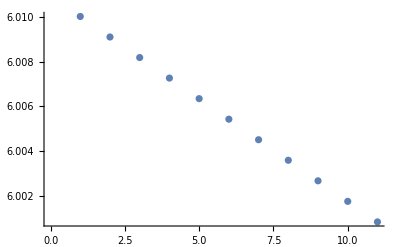

```mathematica
Show[
ListPlot[Transpose[allData][[1]]],
Plot[lm[x],{x,0,11}]]
```

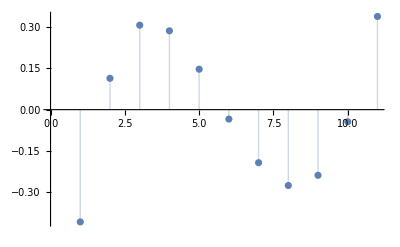

```mathematica
ListPlot[lm["FitResiduals"],Filling->Axis]
```

```mathematica
Max[lm["FitResiduals"]^2]
```

0.165684

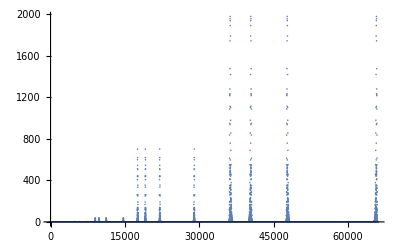

```mathematica
ListPlot[maxResiduals, PlotRange->All]
```

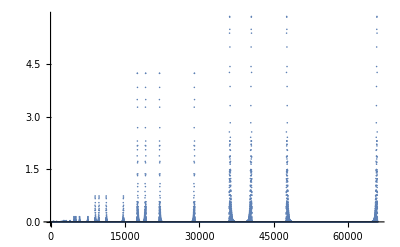

-Graphics-

{{36239},{40415},{47750},{65750}}

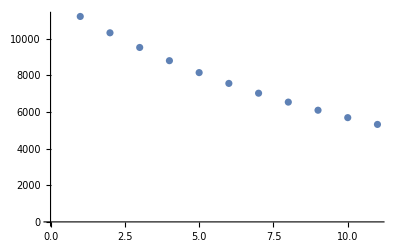

{1.79191×10^-11,1.77223×10^-11,1.40494×10^-13,1.46141×10^-13,8.33234×10^-30,1.55556×10^-13,1.90413×10^-11,9.46746×10^-14,1.77223×10^-11,1.10934×10^-31,1.81567×10^-11,2.13018×10^-11,1.77223×10^-11,9.46746×10^-14,1.40494×10^-13,2.97521×10^-11,1.97807×10^-13,2.30579×10^-11,1.50089×10^-11,1.62246×10^-11,1.40494×10^-13,1.90413×10^-11,1.90413×10^-11,1.40494×10^-13,9.46746×10^-14,1.55556×10^-11,1.74876×10^-13,2.10871×10^-13,2.39621×10^-15,2.30579×10^-11,9.46746×10^-14,2.03655×10^-11,1.46141×10^-13,1.40494×10^-13,1.55556×10^-11,1.40494×10^-13,9.46746×10^-12,1.45785×10^-13,1.77223×10^-13,1.40494×10^-13,1.81567×10^-11,2.97521×10^-11,1.40494×10^-13,1.67928×10^-13,2.30579×10^-11,9.46746×10^-14,9.46746×10^-12,2.03655×10^-11,1.77223×10^-11,2.10871×10^-13,1.62246×10^-11,1.67928×10^-11,1.97807×10^-13,9.46746×10^-12,1.67928×10^-13,1.74876×10^-13,1.40494×10^-11,1.55556×10^-13,1.90413×10^-13,1.79191×10^-13,1.77223×10^-11,2.30579×10^-11,1.74876×10^-13,2.03655×10^-13,1.77223×10^-11,2.30132×10^-13,9.46746×10^-14,2.15608×10^-11,1.90413×10^-11,2.13018×10^-13,2.19085×10^-11,2.13018×10^-11,9.46746×10^-14,1.40494×10^-11,2.03655×10^-13,2.13018×10^-13,1.81567×10^-11,3.08149×10^-31,2.32823×10^-13,9.98402×10^-31,1.74876×10^-11,1.77223×10^-11,2.13018×10^-13,2.13018×10^-13,1.77223×10^-11,2.13018×10^-13,2.30132×10^-13,2.03655×10^-11,1.50089×10^-11,2.30132×10^-13,2.03655×10^-11,7.11947×10^-29,2.30132×10^-13,1.81567×10^-11,2.13018×10^-13,2.13018×10^-13,1.79191×10^-13,2.30132×10^-13,1.81567×10^-11,2.13018×10^-13,2.30132×10^-11,1.74876×10^-13,1.45785×10^-13,9.98402×10^-31,0.,0.,1.70228×10^-15,1.79191×10^-13,0.,2.30579×10^-11,2.10871×10^-13,1.77223×10^-13,1.55556×10^-13,9.98402×10^-31,1.74876×10^-13,0.,0.,0.,2.13018×10^-11,1.40494×10^-13,1.90413×10^-13,3.08149×10^-31,1.74876×10^-13,0.,0.,1.40494×10^-13,0.,1.71384×10^-13,0.,0.,0.,0.,0.,1.78403×10^-13,0.,0.,0.,0.,0.,1.96152×10^-13,0.,0.,0.,0.,0.,1.40494×10^-11,1.79191×10^-13,2.32823×10^-13,2.13018×10^-13,1.40494×10^-13,0.,2.46516×10^-13,0.,0.,3.15544×10^-30,9.98402×10^-31,1.79191×10^-13,2.46516×10^-13,0.,0.,9.98402×10^-31,2.46516×10^-13,0.,6.03972×10^-31,0.,0.,0.,0.,0.,2.10871×10^-13,0.,0.,0.,0.,0.,1.32652×10^-6,1.74876×10^-13,1.79764×10^-7,1.90413×10^-13,4.69656×10^-7,1.79823×10^-7,3.15249×10^-8,1.50089×10^-13,2.14311×10^-13,3.05638×10^-8,1.6394×10^-7,2.11729×10^-11,1.74876×10^-13,1.79191×10^-13,2.54919×10^-15,1.71384×10^-13,1.49728×10^-15,1.55556×10^-13,1.99053×10^-13,1.99053×10^-13,1.55556×10^-13,2.14311×10^-13,4.49855×10^-6,1.79764×10^-7,1.79191×10^-13,1.76048×10^-13,3.66152×10^-7,1.76048×10^-13,1.7237×10^-7,4.46598×10^-6,3.64715×10^-7,1.40494×10^-11,1.90413×10^-13,2.54919×10^-15,1.76048×10^-13,1.2326×10^-30,9.98402×10^-31,2.22151×10^-13,1.73334×10^-31,1.97807×10^-15,1.97807×10^-11,1.71384×10^-13,1.2326×10^-30,4.93038×10^-32,1.74876×10^-13,1.34274×10^-15,1.96152×10^-13,6.28121×10^-13,1.94093×10^-13,2.48836×10^-13,1.79191×10^-13,2.07885×10^-11,1.49728×10^-15,9.98402×10^-31,4.93038×10^-32,1.90413×10^-13,1.79191×10^-13,1.67928×10^-13,1.67928×10^-13,1.79191×10^-15,1.62246×10^-11,8.33234×10^-30,2.39621×10^-15,1.74876×10^-13,1.90413×10^-13,1.40494×10^-13,2.30132×10^-13,1.97807×10^-11,1.45785×10^-11,2.22151×10^-11,1.76048×10^-11,1.96152×10^-11,1.55556×10^-13,2.30579×10^-11,1.70228×10^-15,1.34274×10^-15,1.79191×10^-13,1.40494×10^-13,1.90413×10^-13,1.43657×10^-15,6.62612×10^-6,3.66152×10^-7,2.22151×10^-13,1.81965×10^-17,0.,0.,3.6269×10^-7,6.5579×10^-6,0.,1.74876×10^-11,1.76048×10^-13,1.73334×10^-31,1.67928×10^-13,1.81965×10^-17,2.61552×10^-13,0.,0.,0.,1.76048×10^-11,1.97807×10^-15,1.67928×10^-13,1.90413×10^-13,2.61552×10^-13,0.,0.,9.46746×10^-14,0.,1.83063×10^-6,0.,0.,0.,0.,0.,1.79191×10^-13,0.,0.,0.,0.,0.,3.12974×10^-11,0.,0.,0.,0.,0.,2.13018×10^-11,9.46746×10^-14,1.79191×10^-13,0.,1.79191×10^-15,1.43657×10^-15,9.46746×10^-14,0.,0.,1.90413×10^-11,0.,0.,0.,0.,0.,0.00242732,4.98851×10^-7,0.0000995571,1.764×10^-7,0.000521276,0.0000850265,0.000452086,3.19985×10^-8,1.97807×10^-7,0.000638025,0.000781652,5.63647×10^-6,4.98851×10^-7,1.80061×10^-7,7.19531×10^-7,5.0281×10^-7,1.77459×10^-7,3.19234×10^-8,2.0093×10^-7,1.45785×10^-7,3.29055×10^-8,1.96565×10^-7,0.00211086,0.0000995571,1.80061×10^-7,4.57302×10^-6,0.000249683,3.6269×10^-7,0.000204578,0.00177488,0.000116836,0.000018334,1.764×10^-7,7.19531×10^-7,4.57302×10^-6,1.80774×10^-7,4.46303×10^-6,3.73466×10^-7,1.47139×10^-6,3.65306×10^-7,5.47167×10^-6,5.0281×10^-7,1.80774×10^-7,7.05365×10^-7,4.99839×10^-7,1.7208×10^-7,3.11288×10^-8,2.16908×10^-7,9.55372×10^-8,3.27534×10^-8,2.00303×10^-7,0.0000181667,1.77459×10^-7,4.46303×10^-6,7.05365×10^-7,1.83459×10^-7,4.57302×10^-6,3.71674×10^-7,1.46884×10^-6,3.58659×10^-7,5.43249×10^-6,4.69656×10^-7,1.7237×10^-7,4.99839×10^-7,1.83459×10^-7,6.56893×10^-7,3.01496×10^-8,2.07248×10^-7,1.45785×10^-7,3.26017×10^-8,2.16908×10^-7,0.0000180952,1.79823×10^-7,4.46598×10^-6,3.6269×10^-7,1.7208×10^-7,4.57302×10^-6,6.56893×10^-7,3.68271×10^-7,1.47189×10^-6,0.00273566,0.000249683,3.73466×10^-7,6.57582×10^-6,0.,0.,0.000391517,0.00185755,0.0000838954,0.0000269165,3.6269×10^-7,1.47139×10^-6,3.71674×10^-7,6.57582×10^-6,6.61893×10^-6,0.,0.,0.,0.0000270255,3.65306×10^-7,1.46884×10^-6,3.68271×10^-7,6.61893×10^-6,0.,0.,6.73457×10^-6,0.,0.00115372,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.48003×10^-6,0.,0.,0.,0.,0.,7.22971×10^-6,0.,0.,0.,0.,0.,0.0000270036,3.64715×10^-7,6.5579×10^-6,0.,3.58659×10^-7,1.47189×10^-6,6.73457×10^-6,0.,0.,7.44183×10^-6,0.,0.,0.,0.,0.,0.000485817,6.7555×10^-6,0.00010214,1.73652×10^-6,6.7555×10^-6,1.73652×10^-6,0.00013636,5.48313×10^-6,1.44728×10^-6,5.48313×10^-6,1.44728×10^-6,0.00313122,6.7555×10^-6,7.09836×10^-7,0.000207247,0.00018219,0.0000667409,0.00023117,0.000099965,0.00182643,0.000533689,0.00033749,0.000582159,0.00010214,7.09836×10^-7,1.05194×10^-7,0.000170768,1.82156×10^-8,7.09836×10^-7,1.05194×10^-7,1.82156×10^-8,0.00126393,1.73652×10^-6,0.000207247,1.05194×10^-7,0.0000153774,0.000220897,6.30326×10^-6,0.00028216,0.0000573155,0.00846953,0.00018219,0.0000153774,0.000471291,0.00041121,0.000157297,0.000824373,0.000578036,0.00344362,0.000796419,0.000739764,0.00373355,0.0000667409,0.000220897,0.000471291,0.0000577398,0.000923437,1.92821×10^-6,0.000669897,0.000212933,0.0109494,0.000521276,0.000204578,0.00041121,0.0000577398,0.000654192,0.000848993,0.000811254,0.00307539,0.000657886,0.000820202,0.007136,0.0000850265,0.00177488,0.000391517,0.000157297,0.000923437,0.000654192,0.0000427954,0.00118737,0.000942404,0.000170768,6.30326×10^-6,9.85038×10^-6,0.000277188,1.19956×10^-6,6.30326×10^-6,9.85038×10^-6,1.19956×10^-6,0.00158922,1.82156×10^-8,0.00028216,1.92821×10^-6,9.85038×10^-6,0.000107443,0.0000153335,0.000379623,0.0000373328,0.004157,0.0000573155,0.000669897,0.0000427954,0.000107443,1.37005×10^-6,0.000782161,0.000743825,0.000192858,0.00138962,0.000277188,0.0000153335,0.0000348868,0.0000153335,0.0000348868,0.000277188,0.0000153335,0.0000153335,0.00179332,1.19956×10^-6,0.000379623,1.37005×10^-6,0.0000348868,0.0000249818,1.19956×10^-6,0.000379623,1.37005×10^-6,0.00363044,0.0000373328,0.000782161,0.0000249818,0.0000163148,0.000382856,0.0000373328,0.000782161,0.0000163148,0.00855146,0.000116836,0.00185755,0.,0.000212933,0.00118737,0.000743825,0.0000163148,0.00143096,0.00700393,0.0000838954,0.,0.000192858,0.000382856,0.00143096,0.000192858,0.00143096,0.0000838954,0.00242732,0.000521276,0.0000995571,0.0000850265,4.98851×10^-7,1.764×10^-7,0.000452086,0.000638025,0.000781652,3.19985×10^-8,1.97807×10^-7,0.0109494,0.000521276,0.000204578,0.000654192,0.00041121,0.0000577398,0.000657886,0.000820202,0.00307539,0.000848993,0.000811254,0.00211086,0.0000995571,0.000204578,0.00177488,0.000249683,0.000116836,1.80061×10^-7,4.57302×10^-6,3.6269×10^-7,0.007136,0.0000850265,0.000654192,0.00177488,0.000157297,0.000923437,0.000391517,0.00118737,0.0000427954,0.00846953,0.00041121,0.000157297,0.000471291,0.00018219,0.0000153774,0.000796419,0.000739764,0.00344362,0.000824373,0.000578036,0.00373355,0.0000577398,0.000923437,0.000471291,0.0000667409,0.000220897,0.000212933,0.000669897,1.92821×10^-6,0.00313122,6.7555×10^-6,7.09836×10^-7,0.00018219,0.0000667409,0.000207247,0.000533689,0.00033749,0.00182643,0.00023117,0.000099965,0.00126393,1.73652×10^-6,1.05194×10^-7,6.30326×10^-6,0.0000153774,0.000220897,0.000207247,0.0000573155,0.00028216,0.00273566,0.000249683,0.000391517,0.00185755,0.,0.0000838954,3.73466×10^-7,6.57582×10^-6,0.,0.00855146,0.000116836,0.00118737,0.000212933,0.00185755,0.000743825,0.,0.00143096,0.0000163148,0.004157,0.0000427954,0.000669897,0.0000573155,0.000743825,0.000192858,0.000782161,0.000107443,1.37005×10^-6,0.00115372,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00700393,0.0000838954,0.00143096,0.000192858,0.,0.000382856,0.0000838954,0.00143096,0.000192858,0.00363044,0.0000163148,0.000782161,0.000382856,0.0000373328,0.0000249818,0.0000163148,0.000782161,0.0000373328,0.00158922,1.82156×10^-8,9.85038×10^-6,0.0000153335,1.92821×10^-6,0.00028216,0.000107443,0.0000373328,0.000379623,0.00179332,1.19956×10^-6,0.0000348868,1.37005×10^-6,0.0000249818,0.000379623,1.19956×10^-6,1.37005×10^-6,0.000379623,1.32652×10^-6,4.69656×10^-7,1.79764×10^-7,1.79823×10^-7,1.74876×10^-13,1.90413×10^-13,3.15249×10^-8,3.05638×10^-8,1.6394×10^-7,1.50089×10^-13,2.14311×10^-13,5.43249×10^-6,4.69656×10^-7,1.7237×10^-7,6.56893×10^-7,4.99839×10^-7,1.83459×10^-7,3.26017×10^-8,2.16908×10^-7,1.45785×10^-7,3.01496×10^-8,2.07248×10^-7,4.49855×10^-6,1.79764×10^-7,1.7237×10^-7,4.46598×10^-6,3.66152×10^-7,3.64715×10^-7,1.79191×10^-13,1.76048×10^-13,1.76048×10^-13,0.0000180952,1.79823×10^-7,6.56893×10^-7,4.46598×10^-6,1.7208×10^-7,4.57302×10^-6,3.6269×10^-7,1.47189×10^-6,3.68271×10^-7,5.47167×10^-6,4.99839×10^-7,1.7208×10^-7,7.05365×10^-7,5.0281×10^-7,1.80774×10^-7,3.27534×10^-8,2.00303×10^-7,9.55372×10^-8,3.11288×10^-8,2.16908×10^-7,0.0000181667,1.83459×10^-7,4.57302×10^-6,7.05365×10^-7,1.77459×10^-7,4.46303×10^-6,3.58659×10^-7,1.46884×10^-6,3.71674×10^-7,5.63647×10^-6,4.98851×10^-7,1.80061×10^-7,5.0281×10^-7,1.77459×10^-7,7.19531×10^-7,3.29055×10^-8,1.96565×10^-7,1.45785×10^-7,3.19234×10^-8,2.0093×10^-7,0.000018334,1.764×10^-7,4.57302×10^-6,3.73466×10^-7,1.80774×10^-7,4.46303×10^-6,7.19531×10^-7,3.65306×10^-7,1.47139×10^-6,6.62612×10^-6,3.66152×10^-7,3.6269×10^-7,6.5579×10^-6,0.,0.,2.22151×10^-13,1.81965×10^-17,0.,0.0000270036,3.64715×10^-7,1.47189×10^-6,3.58659×10^-7,6.5579×10^-6,6.73457×10^-6,0.,0.,0.,0.0000270255,3.68271×10^-7,1.46884×10^-6,3.65306×10^-7,6.73457×10^-6,0.,0.,6.61893×10^-6,0.,1.83063×10^-6,0.,0.,0.,0.,0.,7.44183×10^-6,0.,0.,0.,0.,0.,7.22971×10^-6,0.,0.,0.,0.,0.,0.0000269165,3.6269×10^-7,6.57582×10^-6,0.,3.71674×10^-7,1.47139×10^-6,6.61893×10^-6,0.,0.,7.48003×10^-6,0.,0.,0.,0.,0.,1.79191×10^-11,8.33234×10^-30,1.40494×10^-13,1.55556×10^-13,1.77223×10^-11,1.46141×10^-13,1.90413×10^-11,1.10934×10^-31,1.81567×10^-11,9.46746×10^-14,1.77223×10^-11,1.62246×10^-11,8.33234×10^-30,2.39621×10^-15,1.40494×10^-13,1.74876×10^-13,1.90413×10^-13,2.22151×10^-11,1.76048×10^-11,1.45785×10^-11,2.30132×10^-13,1.97807×10^-11,1.90413×10^-11,1.40494×10^-13,2.39621×10^-15,2.30579×10^-11,1.74876×10^-13,9.46746×10^-14,9.46746×10^-14,1.55556×10^-11,2.10871×10^-13,1.96152×10^-11,1.55556×10^-13,1.40494×10^-13,2.30579×10^-11,1.34274×10^-15,1.79191×10^-13,1.70228×10^-15,1.43657×10^-15,1.90413×10^-13,1.97807×10^-11,1.74876×10^-13,1.34274×10^-15,4.93038×10^-32,1.71384×10^-13,1.2326×10^-30,2.48836×10^-13,1.79191×10^-13,1.94093×10^-13,1.96152×10^-13,6.28121×10^-13,2.07885×10^-11,1.90413×10^-13,1.79191×10^-13,4.93038×10^-32,1.49728×10^-15,9.98402×10^-31,1.79191×10^-15,1.67928×10^-13,1.67928×10^-13,2.11729×10^-11,1.74876×10^-13,1.79191×10^-13,1.71384×10^-13,1.49728×10^-15,2.54919×10^-15,1.55556×10^-13,2.14311×10^-13,1.99053×10^-13,1.55556×10^-13,1.99053×10^-13,1.40494×10^-11,1.90413×10^-13,1.76048×10^-13,2.22151×10^-13,1.2326×10^-30,9.98402×10^-31,2.54919×10^-15,1.97807×10^-15,1.73334×10^-31,2.30132×10^-11,1.74876×10^-13,1.70228×10^-15,1.79191×10^-13,0.,0.,1.45785×10^-13,9.98402×10^-31,0.,2.13018×10^-11,9.46746×10^-14,1.43657×10^-15,1.79191×10^-15,1.79191×10^-13,9.46746×10^-14,0.,0.,0.,1.76048×10^-11,1.90413×10^-13,1.67928×10^-13,1.97807×10^-15,9.46746×10^-14,0.,0.,2.61552×10^-13,0.,1.71384×10^-13,0.,0.,0.,0.,0.,1.90413×10^-11,0.,0.,0.,0.,0.,3.12974×10^-11,0.,0.,0.,0.,0.,1.74876×10^-11,1.76048×10^-13,1.81965×10^-17,0.,1.67928×10^-13,1.73334×10^-31,2.61552×10^-13,0.,0.,1.79191×10^-13,0.,0.,0.,0.,0.,1.77223×10^-11,1.77223×10^-11,2.30132×10^-13,2.03655×10^-13,2.30579×10^-11,1.74876×10^-13,2.13018×10^-13,2.19085×10^-11,1.90413×10^-11,9.46746×10^-14,2.15608×10^-11,2.13018×10^-11,2.13018×10^-13,1.81567×10^-11,9.98402×10^-31,2.03655×10^-13,9.46746×10^-14,1.40494×10^-11,2.32823×10^-13,3.08149×10^-31,1.81567×10^-11,2.30579×10^-11,9.46746×10^-14,1.67928×10^-13,2.97521×10^-11,1.40494×10^-13,2.10871×10^-13,1.62246×10^-11,1.77223×10^-11,9.46746×10^-12,2.03655×10^-11,1.67928×10^-11,1.74876×10^-13,1.40494×10^-11,1.67928×10^-13,1.97807×10^-13,9.46746×10^-12,1.79191×10^-13,1.90413×10^-13,1.55556×10^-13,2.13018×10^-11,1.77223×10^-11,9.46746×10^-14,2.97521×10^-11,1.97807×10^-13,1.40494×10^-13,1.40494×10^-13,1.90413×10^-11,1.62246×10^-11,2.30579×10^-11,1.50089×10^-11,2.03655×10^-11,1.46141×10^-13,1.55556×10^-11,1.45785×10^-13,1.40494×10^-13,9.46746×10^-12,1.40494×10^-13,1.40494×10^-13,1.77223×10^-13,1.40494×10^-11,2.13018×10^-13,2.46516×10^-13,0.,2.32823×10^-13,1.79191×10^-13,1.40494×10^-13,0.,0.,2.13018×10^-11,3.08149×10^-31,1.90413×10^-13,1.40494×10^-13,1.40494×10^-13,0.,0.,1.74876×10^-13,0.,6.03972×10^-31,0.,0.,0.,0.,0.,1.96152×10^-13,0.,0.,0.,0.,0.,2.30579×10^-11,2.10871×10^-13,9.98402×10^-31,0.,1.55556×10^-13,1.77223×10^-13,1.74876×10^-13,0.,0.,1.78403×10^-13,0.,0.,0.,0.,0.,0.000485817,0.00010214,6.7555×10^-6,1.73652×10^-6,6.7555×10^-6,1.73652×10^-6,0.00013636,5.48313×10^-6,1.44728×10^-6,5.48313×10^-6,1.44728×10^-6,0.000582159,0.00010214,7.09836×10^-7,1.05194×10^-7,0.000170768,1.82156×10^-8,7.09836×10^-7,1.05194×10^-7,1.82156×10^-8,0.00313122,6.7555×10^-6,7.09836×10^-7,0.000207247,0.00018219,0.0000667409,0.00023117,0.000099965,0.00182643,0.000533689,0.00033749,0.00126393,1.73652×10^-6,1.05194×10^-7,0.000207247,0.0000153774,0.000220897,6.30326×10^-6,0.00028216,0.0000573155,0.00846953,0.00018219,0.0000153774,0.000471291,0.00041121,0.000157297,0.000824373,0.000578036,0.00344362,0.000796419,0.000739764,0.00373355,0.0000667409,0.000220897,0.000471291,1.92821×10^-6,0.000669897,0.0000577398,0.000923437,0.000212933,0.000942404,0.000277188,1.19956×10^-6,1.19956×10^-6,0.000170768,6.30326×10^-6,9.85038×10^-6,6.30326×10^-6,9.85038×10^-6,0.00158922,0.0000153335,0.000379623,0.0000373328,1.82156×10^-8,0.00028216,1.92821×10^-6,9.85038×10^-6,0.000107443,0.004157,1.37005×10^-6,0.000782161,0.000192858,0.0000573155,0.000669897,0.000107443,0.0000427954,0.000743825,0.0109494,0.00041121,0.0000577398,0.000654192,0.000521276,0.000204578,0.000848993,0.000811254,0.00307539,0.000657886,0.000820202,0.007136,0.000157297,0.000923437,0.0000427954,0.000654192,0.0000850265,0.00177488,0.00118737,0.000391517,0.00242732,0.000521276,0.0000850265,0.0000995571,4.98851×10^-7,1.764×10^-7,0.000638025,0.000781652,0.000452086,3.19985×10^-8,1.97807×10^-7,0.00211086,0.000204578,0.00177488,0.0000995571,0.000116836,0.000249683,1.80061×10^-7,4.57302×10^-6,3.6269×10^-7,0.00855146,0.,0.0000163148,0.00143096,0.000212933,0.000743825,0.00118737,0.000116836,0.00185755,0.00273566,0.,0.0000838954,0.000391517,0.000249683,0.00185755,3.73466×10^-7,6.57582×10^-6,0.,1.32652×10^-6,4.69656×10^-7,1.79764×10^-7,1.79823×10^-7,1.74876×10^-13,1.90413×10^-13,3.15249×10^-8,3.05638×10^-8,1.6394×10^-7,1.50089×10^-13,2.14311×10^-13,5.43249×10^-6,4.69656×10^-7,1.7237×10^-7,6.56893×10^-7,4.99839×10^-7,1.83459×10^-7,3.26017×10^-8,2.16908×10^-7,1.45785×10^-7,3.01496×10^-8,2.07248×10^-7,4.49855×10^-6,1.79764×10^-7,1.7237×10^-7,4.46598×10^-6,3.66152×10^-7,3.64715×10^-7,1.79191×10^-13,1.76048×10^-13,1.76048×10^-13,0.0000180952,1.79823×10^-7,6.56893×10^-7,4.46598×10^-6,1.7208×10^-7,4.57302×10^-6,3.6269×10^-7,1.47189×10^-6,3.68271×10^-7,5.47167×10^-6,4.99839×10^-7,1.7208×10^-7,7.05365×10^-7,5.0281×10^-7,1.80774×10^-7,3.27534×10^-8,2.00303×10^-7,9.55372×10^-8,3.11288×10^-8,2.16908×10^-7,0.0000181667,1.83459×10^-7,4.57302×10^-6,7.05365×10^-7,1.77459×10^-7,4.46303×10^-6,3.58659×10^-7,1.46884×10^-6,3.71674×10^-7,5.63647×10^-6,4.98851×10^-7,1.80061×10^-7,5.0281×10^-7,1.77459×10^-7,7.19531×10^-7,3.29055×10^-8,1.96565×10^-7,1.45785×10^-7,3.19234×10^-8,2.0093×10^-7,0.000018334,1.764×10^-7,4.57302×10^-6,3.73466×10^-7,1.80774×10^-7,4.46303×10^-6,7.19531×10^-7,3.65306×10^-7,1.47139×10^-6,6.62612×10^-6,3.66152×10^-7,3.6269×10^-7,6.5579×10^-6,0.,0.,2.22151×10^-13,1.81965×10^-17,0.,0.0000270036,3.64715×10^-7,1.47189×10^-6,3.58659×10^-7,6.5579×10^-6,6.73457×10^-6,0.,0.,0.,0.0000270255,3.68271×10^-7,1.46884×10^-6,3.65306×10^-7,6.73457×10^-6,0.,0.,6.61893×10^-6,0.,1.83063×10^-6,0.,0.,0.,0.,0.,7.44183×10^-6,0.,0.,0.,0.,0.,7.22971×10^-6,0.,0.,0.,0.,0.,0.0000269165,0.,3.6269×10^-7,6.57582×10^-6,3.71674×10^-7,1.47139×10^-6,6.61893×10^-6,0.,0.,7.48003×10^-6,0.,0.,0.,0.,0.,1.79191×10^-11,8.33234×10^-30,1.40494×10^-13,1.55556×10^-13,1.77223×10^-11,1.46141×10^-13,1.90413×10^-11,1.10934×10^-31,1.81567×10^-11,9.46746×10^-14,1.77223×10^-11,1.62246×10^-11,8.33234×10^-30,2.39621×10^-15,1.40494×10^-13,1.74876×10^-13,1.90413×10^-13,2.22151×10^-11,1.76048×10^-11,1.45785×10^-11,2.30132×10^-13,1.97807×10^-11,1.90413×10^-11,1.40494×10^-13,2.39621×10^-15,2.30579×10^-11,1.74876×10^-13,9.46746×10^-14,9.46746×10^-14,1.55556×10^-11,2.10871×10^-13,1.96152×10^-11,1.55556×10^-13,1.40494×10^-13,2.30579×10^-11,1.34274×10^-15,1.79191×10^-13,1.70228×10^-15,1.43657×10^-15,1.90413×10^-13,1.97807×10^-11,1.74876×10^-13,1.34274×10^-15,4.93038×10^-32,1.71384×10^-13,1.2326×10^-30,2.48836×10^-13,1.79191×10^-13,1.94093×10^-13,1.96152×10^-13,6.28121×10^-13,2.07885×10^-11,1.90413×10^-13,1.79191×10^-13,4.93038×10^-32,1.49728×10^-15,9.98402×10^-31,1.79191×10^-15,1.67928×10^-13,1.67928×10^-13,2.11729×10^-11,1.74876×10^-13,1.79191×10^-13,1.71384×10^-13,1.49728×10^-15,2.54919×10^-15,1.55556×10^-13,2.14311×10^-13,1.99053×10^-13,1.55556×10^-13,1.99053×10^-13,1.40494×10^-11,1.90413×10^-13,1.76048×10^-13,2.22151×10^-13,1.2326×10^-30,9.98402×10^-31,2.54919×10^-15,1.97807×10^-15,1.73334×10^-31,2.30132×10^-11,1.74876×10^-13,1.70228×10^-15,1.79191×10^-13,0.,0.,1.45785×10^-13,9.98402×10^-31,0.,2.13018×10^-11,9.46746×10^-14,1.43657×10^-15,1.79191×10^-15,1.79191×10^-13,9.46746×10^-14,0.,0.,0.,1.76048×10^-11,1.90413×10^-13,1.67928×10^-13,1.97807×10^-15,9.46746×10^-14,0.,0.,2.61552×10^-13,0.,1.71384×10^-13,0.,0.,0.,0.,0.,1.90413×10^-11,0.,0.,0.,0.,0.,3.12974×10^-11,0.,0.,0.,0.,0.,1.74876×10^-11,1.76048×10^-13,1.81965×10^-17,0.,1.67928×10^-13,1.73334×10^-31,2.61552×10^-13,0.,0.,1.79191×10^-13,0.,0.,0.,0.,0.,1.74876×10^-11,1.77223×10^-11,2.13018×10^-13,2.13018×10^-13,1.77223×10^-11,2.13018×10^-13,1.50089×10^-11,2.30132×10^-13,2.03655×10^-11,2.30132×10^-13,2.03655×10^-11,1.77223×10^-11,1.77223×10^-11,2.30132×10^-13,2.03655×10^-13,2.30579×10^-11,1.74876×10^-13,2.13018×10^-13,2.19085×10^-11,1.90413×10^-11,9.46746×10^-14,2.15608×10^-11,7.11947×10^-29,2.13018×10^-13,2.30132×10^-13,1.81567×10^-11,1.79191×10^-13,2.13018×10^-13,2.30132×10^-13,1.81567×10^-11,2.13018×10^-13,2.13018×10^-11,2.13018×10^-13,2.03655×10^-13,1.81567×10^-11,9.46746×10^-14,1.40494×10^-11,9.98402×10^-31,2.32823×10^-13,3.08149×10^-31,1.81567×10^-11,2.30579×10^-11,9.46746×10^-14,1.67928×10^-13,2.97521×10^-11,1.40494×10^-13,2.10871×10^-13,1.62246×10^-11,1.77223×10^-11,9.46746×10^-12,2.03655×10^-11,1.67928×10^-11,1.74876×10^-13,1.40494×10^-11,1.67928×10^-13,1.97807×10^-13,9.46746×10^-12,1.79191×10^-13,1.90413×10^-13,1.55556×10^-13,2.13018×10^-11,1.77223×10^-11,9.46746×10^-14,2.97521×10^-11,1.97807×10^-13,1.40494×10^-13,1.40494×10^-13,1.90413×10^-11,1.62246×10^-11,2.30579×10^-11,1.50089×10^-11,2.03655×10^-11,1.46141×10^-13,1.55556×10^-11,1.45785×10^-13,1.40494×10^-13,9.46746×10^-12,1.40494×10^-13,1.40494×10^-13,1.77223×10^-13,3.15544×10^-30,1.79191×10^-13,9.98402×10^-31,2.46516×10^-13,0.,0.,9.98402×10^-31,2.46516×10^-13,0.,1.40494×10^-11,2.13018×10^-13,2.32823×10^-13,1.79191×10^-13,2.46516×10^-13,1.40494×10^-13,0.,0.,0.,2.13018×10^-11,3.08149×10^-31,1.90413×10^-13,1.40494×10^-13,1.40494×10^-13,0.,0.,1.74876×10^-13,0.,2.10871×10^-13,0.,0.,0.,0.,0.,6.03972×10^-31,0.,0.,0.,0.,0.,1.96152×10^-13,0.,0.,0.,0.,0.,2.30579×10^-11,2.10871×10^-13,9.98402×10^-31,0.,1.55556×10^-13,1.77223×10^-13,1.74876×10^-13,0.,0.,1.78403×10^-13,0.,0.,0.,0.,0.,1.79191×10^-11,1.77223×10^-11,1.40494×10^-13,1.46141×10^-13,8.33234×10^-30,1.55556×10^-13,1.90413×10^-11,9.46746×10^-14,1.77223×10^-11,1.10934×10^-31,1.81567×10^-11,2.13018×10^-11,1.77223×10^-11,9.46746×10^-14,1.40494×10^-13,2.97521×10^-11,1.97807×10^-13,2.30579×10^-11,1.50089×10^-11,1.62246×10^-11,1.40494×10^-13,1.90413×10^-11,1.90413×10^-11,1.40494×10^-13,9.46746×10^-14,1.55556×10^-11,1.74876×10^-13,2.10871×10^-13,2.39621×10^-15,2.30579×10^-11,9.46746×10^-14,2.03655×10^-11,1.46141×10^-13,1.40494×10^-13,1.55556×10^-11,1.40494×10^-13,9.46746×10^-12,1.45785×10^-13,1.77223×10^-13,1.40494×10^-13,1.81567×10^-11,2.97521×10^-11,1.40494×10^-13,1.67928×10^-13,2.30579×10^-11,9.46746×10^-14,9.46746×10^-12,2.03655×10^-11,1.77223×10^-11,2.10871×10^-13,1.62246×10^-11,1.67928×10^-11,1.97807×10^-13,9.46746×10^-12,1.67928×10^-13,1.74876×10^-13,1.40494×10^-11,1.55556×10^-13,1.90413×10^-13,1.79191×10^-13,1.77223×10^-11,1.77223×10^-11,2.30132×10^-13,2.30579×10^-11,1.74876×10^-13,2.03655×10^-13,9.46746×10^-14,2.15608×10^-11,1.90413×10^-11,2.13018×10^-13,2.19085×10^-11,2.13018×10^-11,2.13018×10^-13,1.81567×10^-11,9.98402×10^-31,9.46746×10^-14,1.40494×10^-11,2.03655×10^-13,3.08149×10^-31,2.32823×10^-13,2.30132×10^-11,1.74876×10^-13,1.45785×10^-13,9.98402×10^-31,0.,0.,1.70228×10^-15,1.79191×10^-13,0.,2.30579×10^-11,2.10871×10^-13,1.77223×10^-13,1.55556×10^-13,9.98402×10^-31,1.74876×10^-13,0.,0.,0.,2.13018×10^-11,1.40494×10^-13,1.90413×10^-13,3.08149×10^-31,1.74876×10^-13,0.,0.,1.40494×10^-13,0.,1.71384×10^-13,0.,0.,0.,0.,0.,1.78403×10^-13,0.,0.,0.,0.,0.,1.96152×10^-13,0.,0.,0.,0.,0.,1.40494×10^-11,2.13018×10^-13,2.46516×10^-13,0.,1.79191×10^-13,2.32823×10^-13,1.40494×10^-13,0.,0.,6.03972×10^-31,0.,0.,0.,0.,0.,1.32652×10^-6,1.74876×10^-13,1.79764×10^-7,1.90413×10^-13,4.69656×10^-7,1.79823×10^-7,3.15249×10^-8,1.50089×10^-13,2.14311×10^-13,3.05638×10^-8,1.6394×10^-7,2.11729×10^-11,1.74876×10^-13,1.79191×10^-13,2.54919×10^-15,1.71384×10^-13,1.49728×10^-15,1.55556×10^-13,1.99053×10^-13,1.99053×10^-13,1.55556×10^-13,2.14311×10^-13,4.49855×10^-6,1.79764×10^-7,1.79191×10^-13,1.76048×10^-13,3.66152×10^-7,1.76048×10^-13,1.7237×10^-7,4.46598×10^-6,3.64715×10^-7,1.40494×10^-11,1.90413×10^-13,2.54919×10^-15,1.76048×10^-13,1.2326×10^-30,9.98402×10^-31,2.22151×10^-13,1.73334×10^-31,1.97807×10^-15,1.97807×10^-11,1.71384×10^-13,1.2326×10^-30,4.93038×10^-32,1.74876×10^-13,1.34274×10^-15,1.96152×10^-13,6.28121×10^-13,1.94093×10^-13,2.48836×10^-13,1.79191×10^-13,2.07885×10^-11,1.49728×10^-15,9.98402×10^-31,4.93038×10^-32,1.90413×10^-13,1.79191×10^-13,1.67928×10^-13,1.67928×10^-13,1.79191×10^-15,1.62246×10^-11,8.33234×10^-30,2.39621×10^-15,1.74876×10^-13,1.90413×10^-13,1.40494×10^-13,2.30132×10^-13,1.97807×10^-11,1.45785×10^-11,2.22151×10^-11,1.76048×10^-11,1.96152×10^-11,1.55556×10^-13,2.30579×10^-11,1.70228×10^-15,1.34274×10^-15,1.79191×10^-13,1.40494×10^-13,1.90413×10^-13,1.43657×10^-15,6.62612×10^-6,3.66152×10^-7,2.22151×10^-13,1.81965×10^-17,0.,0.,3.6269×10^-7,6.5579×10^-6,0.,1.74876×10^-11,1.76048×10^-13,1.73334×10^-31,1.67928×10^-13,1.81965×10^-17,2.61552×10^-13,0.,0.,0.,1.76048×10^-11,1.97807×10^-15,1.67928×10^-13,1.90413×10^-13,2.61552×10^-13,0.,0.,9.46746×10^-14,0.,1.83063×10^-6,0.,0.,0.,0.,0.,1.79191×10^-13,0.,0.,0.,0.,0.,3.12974×10^-11,0.,0.,0.,0.,0.,2.13018×10^-11,9.46746×10^-14,1.79191×10^-13,0.,1.79191×10^-15,1.43657×10^-15,9.46746×10^-14,0.,0.,1.90413×10^-11,0.,0.,0.,0.,0.,0.00242732,4.98851×10^-7,0.0000995571,1.764×10^-7,0.000521276,0.0000850265,0.000452086,3.19985×10^-8,1.97807×10^-7,0.000638025,0.000781652,5.63647×10^-6,4.98851×10^-7,1.80061×10^-7,7.19531×10^-7,5.0281×10^-7,1.77459×10^-7,3.19234×10^-8,2.0093×10^-7,1.45785×10^-7,3.29055×10^-8,1.96565×10^-7,0.00211086,0.0000995571,1.80061×10^-7,4.57302×10^-6,0.000249683,3.6269×10^-7,0.000204578,0.00177488,0.000116836,0.000018334,1.764×10^-7,7.19531×10^-7,4.57302×10^-6,1.80774×10^-7,4.46303×10^-6,3.73466×10^-7,1.47139×10^-6,3.65306×10^-7,5.47167×10^-6,5.0281×10^-7,1.80774×10^-7,7.05365×10^-7,4.99839×10^-7,1.7208×10^-7,3.11288×10^-8,2.16908×10^-7,9.55372×10^-8,3.27534×10^-8,2.00303×10^-7,0.0000181667,1.77459×10^-7,4.46303×10^-6,7.05365×10^-7,1.83459×10^-7,4.57302×10^-6,3.71674×10^-7,1.46884×10^-6,3.58659×10^-7,5.43249×10^-6,4.69656×10^-7,1.7237×10^-7,4.99839×10^-7,1.83459×10^-7,6.56893×10^-7,3.01496×10^-8,2.07248×10^-7,1.45785×10^-7,3.26017×10^-8,2.16908×10^-7,0.0000180952,1.79823×10^-7,4.46598×10^-6,3.6269×10^-7,1.7208×10^-7,4.57302×10^-6,6.56893×10^-7,3.68271×10^-7,1.47189×10^-6,0.00273566,0.,0.0000838954,0.000249683,3.73466×10^-7,6.57582×10^-6,0.,0.000391517,0.00185755,0.0000269165,0.,3.6269×10^-7,1.47139×10^-6,3.71674×10^-7,6.57582×10^-6,6.61893×10^-6,0.,0.,0.0000270255,3.65306×10^-7,1.46884×10^-6,3.68271×10^-7,6.61893×10^-6,0.,0.,6.73457×10^-6,0.,7.48003×10^-6,0.,0.,0.,0.,0.,7.22971×10^-6,0.,0.,0.,0.,0.,0.0000270036,3.64715×10^-7,6.5579×10^-6,0.,3.58659×10^-7,1.47189×10^-6,6.73457×10^-6,0.,0.,7.44183×10^-6,0.,0.,0.,0.,0.,0.0109494,0.000521276,0.000204578,0.000654192,0.00041121,0.0000577398,0.000657886,0.000820202,0.00307539,0.000848993,0.000811254,0.007136,0.0000850265,0.00177488,0.000391517,0.000654192,0.000157297,0.000923437,0.00118737,0.0000427954,0.00846953,0.00041121,0.000157297,0.000471291,0.00018219,0.0000153774,0.000796419,0.000739764,0.00344362,0.000824373,0.000578036,0.00373355,0.0000577398,0.000923437,0.000471291,0.000212933,0.000669897,0.0000667409,0.000220897,1.92821×10^-6,0.00855146,0.,0.00143096,0.0000163148,0.000116836,0.00185755,0.00118737,0.000212933,0.000743825,0.004157,0.000192858,0.000782161,1.37005×10^-6,0.0000427954,0.000669897,0.000743825,0.0000573155,0.000107443,0.00313122,6.7555×10^-6,7.09836×10^-7,0.00018219,0.0000667409,0.000207247,0.000533689,0.00033749,0.00182643,0.00023117,0.000099965,0.00126393,1.73652×10^-6,1.05194×10^-7,6.30326×10^-6,0.0000153774,0.000220897,0.0000573155,0.000207247,0.00028216,0.00158922,0.0000153335,0.0000373328,0.000379623,1.82156×10^-8,9.85038×10^-6,1.92821×10^-6,0.000107443,0.00028216,1.74876×10^-9,1.90413×10^-11,1.96152×10^-11,2.15608×10^-11,1.71384×10^-11,1.77987×10^-29,1.55556×10^-11,1.79191×10^-11,2.14311×10^-11,1.90413×10^-11,2.22151×10^-11,1.02236×10^-27,9.46746×10^-14,2.30579×10^-11,1.96152×10^-11,2.15608×10^-11,1.97807×10^-11,2.10871×10^-11,2.46516×10^-11,5.04871×10^-29,2.13018×10^-11,2.13018×10^-11,1.55556×10^-11,1.77223×10^-11,1.50089×10^-11,2.15608×10^-11,2.15608×10^-11,1.55556×10^-13,2.15608×10^-9,1.62246×10^-11,1.97807×10^-11,1.55556×10^-13,1.55556×10^-11,1.55556×10^-11,2.13018×10^-11,1.77223×10^-11,1.76048×10^-11,1.50089×10^-11,1.67928×10^-11,1.45785×10^-9,1.40494×10^-13,9.46746×10^-12,1.55556×10^-11,1.42488×10^-29,2.30579×10^-11,3.12974×10^-11,2.30132×10^-11,2.13018×10^-11,1.77494×10^-30,1.40494×10^-11,1.67928×10^-11,1.90413×10^-11,2.03655×10^-11,1.55556×10^-11,1.42488×10^-29,2.31027×10^-13,2.15608×10^-9,1.77223×10^-11,2.30579×10^-11,2.31027×10^-13,1.71384×10^-11,1.81567×10^-13,1.79191×10^-11,2.30579×10^-11,2.13018×10^-11,1.62246×10^-11,1.55556×10^-11,2.13018×10^-9,2.10871×10^-13,9.46746×10^-14,1.71384×10^-11,2.07885×10^-11,1.40494×10^-11,1.90413×10^-11,1.55556×10^-11,1.55556×10^-11,1.45785×10^-11,1.77223×10^-11,1.26218×10^-29,1.62246×10^-11,2.15608×10^-11,1.81567×10^-13,2.07885×10^-11,2.19085×10^-13,1.90413×10^-11,1.90413×10^-11,1.40494×10^-11,2.19085×10^-13,9.46746×10^-12,2.08309×10^-30,1.79191×10^-11,1.40494×10^-11,1.62246×10^-11,1.77494×10^-30,2.8399×10^-29,1.40494×10^-11,2.13018×10^-13,2.30132×10^-13,9.46746×10^-12,1.81567×10^-11,1.62246×10^-11,1.62246×10^-11,1.40494×10^-11,1.76048×10^-11,4.43734×10^-31,1.67928×10^-11,1.96152×10^-11,2.19085×10^-11,2.03655×10^-11,2.08309×10^-30,1.81567×10^-11,2.13018×10^-13,1.45785×10^-11,1.50089×10^-11,1.62246×10^-11,2.13018×10^-13,1.62246×10^-11,2.13018×10^-13,1.90413×10^-11,1.55556×10^-11,1.97807×10^-11,1.90413×10^-11,1.55556×10^-11,1.65075×10^-7,3.15249×10^-8,1.43657×10^-13,3.19265×10^-13,7.62996×10^-8,3.16989×10^-8,2.54919×10^-9,1.76048×10^-13,2.74586×10^-13,2.37571×10^-9,2.60947×10^-8,1.43657×10^-11,1.50089×10^-13,1.55556×10^-13,1.43657×10^-13,1.94093×10^-13,1.62246×10^-13,1.50089×10^-13,2.80974×10^-13,1.23235×10^-13,1.62246×10^-13,1.62246×10^-13,1.92862×10^-13,2.14311×10^-13,1.99053×10^-13,3.19265×10^-13,1.94093×10^-13,1.55556×10^-13,1.71384×10^-11,1.99053×10^-13,1.62246×10^-13,1.55556×10^-13,4.92941×10^-13,1.71384×10^-13,2.30132×10^-13,1.81965×10^-13,9.46746×10^-12,2.53978×10^-13,1.50089×10^-13,7.09975×10^-30,1.55556×10^-13,1.96152×10^-13,4.92941×10^-13,2.92961×10^-13,1.79191×10^-13,2.76053×10^-13,1.71384×10^-11,1.90413×10^-11,1.50089×10^-13,2.13018×10^-11,1.96152×10^-11,2.14311×10^-13,6.28121×10^-13,1.71384×10^-13,2.92961×10^-13,6.03972×10^-31,1.71384×10^-11,1.94093×10^-13,1.79191×10^-13,6.03972×10^-31,9.46746×10^-12,1.97807×10^-13,1.2653×10^-13,1.79191×10^-11,1.78403×10^-11,2.30132×10^-11,1.10934×10^-29,3.25086×10^-11,2.48836×10^-13,2.30132×10^-13,9.46746×10^-12,2.30579×10^-11,1.79191×10^-11,2.67788×10^-13,1.81567×10^-11,1.74876×10^-11,1.45785×10^-11,1.76048×10^-11,1.40494×10^-11,1.79191×10^-13,1.97807×10^-11,1.97807×10^-13,2.30579×10^-11,1.40494×10^-11,1.71384×10^-11,1.45785×10^-11,1.79191×10^-11,1.40494×10^-11,2.13018×10^-11,1.71384×10^-13,2.10871×10^-13,1.97807×10^-11,2.13018×10^-11,1.79191×10^-11,2.30132×10^-11,1.76048×10^-9,1.10934×10^-31,2.22151×10^-11,1.71384×10^-11,2.13018×10^-11,3.08149×10^-29,1.76048×10^-11,9.46746×10^-12,4.93038×10^-30,1.81567×10^-11,1.97807×10^-11,2.30579×10^-11,1.81567×10^-11,1.76048×10^-11,1.77987×10^-29,1.71384×10^-13,3.08149×10^-29,0.00312426,0.000452086,7.94215×10^-8,3.29562×10^-8,0.000902561,0.000553333,0.000512722,2.68512×10^-9,2.63211×10^-8,0.000618235,0.000904369,6.56893×10^-7,3.19985×10^-8,3.19234×10^-8,7.94215×10^-8,1.35815×10^-7,7.136×10^-8,2.56333×10^-9,2.29427×10^-8,1.17487×10^-8,2.55626×10^-9,1.87862×10^-8,8.11259×10^-7,1.97807×10^-7,2.0093×10^-7,3.29562×10^-8,1.35815×10^-7,3.26775×10^-8,6.35532×10^-7,1.45785×10^-7,7.136×10^-8,3.26775×10^-8,7.06147×10^-8,3.18735×10^-8,2.29461×10^-9,1.9954×10^-8,1.20539×10^-8,2.92961×10^-9,3.46012×10^-8,6.16719×10^-7,3.29055×10^-8,3.11288×10^-8,7.06147×10^-8,1.35301×10^-7,5.52086×10^-8,2.45822×10^-9,2.93535×10^-8,1.14475×10^-8,2.72148×10^-9,1.69182×10^-8,7.89985×10^-7,1.96565×10^-7,2.16908×10^-7,3.18735×10^-8,1.35301×10^-7,3.20986×10^-8,6.62573×10^-7,9.55372×10^-8,5.52086×10^-8,3.20986×10^-8,7.82434×10^-8,3.19734×10^-8,2.63463×10^-9,2.41444×10^-8,1.10323×10^-8,2.46516×10^-9,2.36686×10^-8,6.58027×10^-7,3.27534×10^-8,3.01496×10^-8,7.82434×10^-8,1.20307×10^-7,9.55372×10^-8,2.78754×10^-9,2.15658×10^-8,1.67368×10^-8,2.61314×10^-9,2.43185×10^-8,8.30265×10^-7,2.00303×10^-7,2.07248×10^-7,3.19734×10^-8,1.20307×10^-7,3.24252×10^-8,6.14524×10^-7,1.45785×10^-7,9.55372×10^-8,3.24252×10^-8,5.88826×10^-8,3.09809×10^-8,2.44437×10^-9,1.82156×10^-8,1.80273×10^-8,2.24795×10^-9,2.67769×10^-8,6.14524×10^-7,3.05638×10^-8,3.26017×10^-8,7.62996×10^-8,5.88826×10^-8,1.21767×10^-7,2.2281×10^-9,2.15658×10^-8,1.15375×10^-8,2.32149×10^-9,2.21864×10^-8,7.87501×10^-7,1.6394×10^-7,2.16908×10^-7,3.16989×10^-8,3.09809×10^-8,1.21767×10^-7,0.000875196,0.00013636,0.0000356283,9.40739×10^-6,0.0000356283,9.40739×10^-6,0.000328765,0.0000407132,0.0000113061,0.0000407132,0.0000113061,0.00950952,5.48313×10^-6,0.00023117,0.0000356283,0.00055664,0.000638976,0.000881629,0.000386139,0.00729232,0.00256433,0.00125931,0.000307384,1.44728×10^-6,0.000099965,9.40739×10^-6,0.00055664,0.000201591,0.0277462,0.00182643,0.000638976,0.000201591,0.00135743,0.000589379,0.00345506,0.00213199,0.015349,0.00399786,0.00271128,0.0358702,0.000533689,0.000824373,0.00135743,0.00295075,0.00162922,0.00380327,0.00296774,0.0146364,0.00346106,0.00296537,0.0020443,0.00033749,0.000578036,0.000589379,0.00295075,0.000742836,0.0342302,0.00344362,0.00162922,0.000742836,0.00156816,0.000892898,0.0030094,0.00280218,0.0109999,0.00249127,0.00255279,0.0287196,0.000796419,0.000848993,0.00156816,0.00340109,0.0013612,0.00211047,0.00226496,0.00754857,0.00168548,0.00198025,0.0032214,0.000739764,0.000811254,0.000892898,0.00340109,0.000750144,0.0225609,0.00307539,0.0013612,0.000750144,0.00112295,0.000754267,0.00142087,0.00171083,0.00501819,0.00110707,0.00146796,0.0173539,0.000638025,0.000657886,0.000902561,0.00112295,0.00263686,0.000938801,0.00125064,0.00330287,0.00072749,0.00106614,0.00324573,0.000781652,0.000820202,0.000553333,0.000754267,0.00263686,0.00312426,0.000452086,0.000902561,0.000553333,7.94215×10^-8,3.29562×10^-8,0.000512722,0.000618235,0.000904369,2.68512×10^-9,2.63211×10^-8,0.0173539,0.000638025,0.000657886,0.000902561,0.00263686,0.00112295,0.00072749,0.00106614,0.00330287,0.000938801,0.00125064,0.00324573,0.000781652,0.000820202,0.000553333,0.00263686,0.000754267,0.0225609,0.00307539,0.00112295,0.000754267,0.0013612,0.000750144,0.00110707,0.00146796,0.00501819,0.00142087,0.00171083,0.0287196,0.000848993,0.000796419,0.0013612,0.00340109,0.00156816,0.00168548,0.00198025,0.00754857,0.00211047,0.00226496,0.0032214,0.000811254,0.000739764,0.000750144,0.00340109,0.000892898,0.0342302,0.00344362,0.00156816,0.000892898,0.00162922,0.000742836,0.00249127,0.00255279,0.0109999,0.0030094,0.00280218,0.0358702,0.000824373,0.000533689,0.00162922,0.00295075,0.00135743,0.00346106,0.00296537,0.0146364,0.00380327,0.00296774,0.0020443,0.000578036,0.00033749,0.000742836,0.00295075,0.000589379,0.0277462,0.00182643,0.00135743,0.000589379,0.000638976,0.000201591,0.00399786,0.00271128,0.015349,0.00345506,0.00213199,0.00950952,5.48313×10^-6,0.00023117,0.0000356283,0.000638976,0.00055664,0.00256433,0.00125931,0.00729232,0.000881629,0.000386139,0.000307384,1.44728×10^-6,0.000099965,9.40739×10^-6,0.000201591,0.00055664,1.65075×10^-7,3.15249×10^-8,7.62996×10^-8,3.16989×10^-8,1.43657×10^-13,3.19265×10^-13,2.54919×10^-9,2.37571×10^-9,2.60947×10^-8,1.76048×10^-13,2.74586×10^-13,6.14524×10^-7,3.05638×10^-8,3.26017×10^-8,7.62996×10^-8,1.21767×10^-7,5.88826×10^-8,2.32149×10^-9,2.21864×10^-8,1.15375×10^-8,2.2281×10^-9,2.15658×10^-8,7.87501×10^-7,1.6394×10^-7,2.16908×10^-7,3.16989×10^-8,1.21767×10^-7,3.09809×10^-8,6.14524×10^-7,1.45785×10^-7,5.88826×10^-8,3.09809×10^-8,9.55372×10^-8,3.24252×10^-8,2.24795×10^-9,2.67769×10^-8,1.80273×10^-8,2.44437×10^-9,1.82156×10^-8,6.58027×10^-7,3.01496×10^-8,3.27534×10^-8,9.55372×10^-8,1.20307×10^-7,7.82434×10^-8,2.61314×10^-9,2.43185×10^-8,1.67368×10^-8,2.78754×10^-9,2.15658×10^-8,8.30265×10^-7,2.07248×10^-7,2.00303×10^-7,3.24252×10^-8,1.20307×10^-7,3.19734×10^-8,6.62573×10^-7,9.55372×10^-8,7.82434×10^-8,3.19734×10^-8,5.52086×10^-8,3.20986×10^-8,2.46516×10^-9,2.36686×10^-8,1.10323×10^-8,2.63463×10^-9,2.41444×10^-8,6.16719×10^-7,3.11288×10^-8,3.29055×10^-8,5.52086×10^-8,1.35301×10^-7,7.06147×10^-8,2.72148×10^-9,1.69182×10^-8,1.14475×10^-8,2.45822×10^-9,2.93535×10^-8,7.89985×10^-7,2.16908×10^-7,1.96565×10^-7,3.20986×10^-8,1.35301×10^-7,3.18735×10^-8,6.35532×10^-7,1.45785×10^-7,7.06147×10^-8,3.18735×10^-8,7.136×10^-8,3.26775×10^-8,2.92961×10^-9,3.46012×10^-8,1.20539×10^-8,2.29461×10^-9,1.9954×10^-8,6.56893×10^-7,3.19985×10^-8,3.19234×10^-8,7.94215×10^-8,7.136×10^-8,1.35815×10^-7,2.55626×10^-9,1.87862×10^-8,1.17487×10^-8,2.56333×10^-9,2.29427×10^-8,8.11259×10^-7,1.97807×10^-7,2.0093×10^-7,3.29562×10^-8,3.26775×10^-8,1.35815×10^-7,1.74876×10^-9,1.90413×10^-11,1.71384×10^-11,1.77987×10^-29,1.96152×10^-11,2.15608×10^-11,1.55556×10^-11,1.90413×10^-11,2.22151×10^-11,1.79191×10^-11,2.14311×10^-11,1.76048×10^-9,1.10934×10^-31,2.22151×10^-11,1.71384×10^-11,3.08149×10^-29,2.13018×10^-11,1.81567×10^-11,1.97807×10^-11,4.93038×10^-30,1.76048×10^-11,9.46746×10^-12,2.30579×10^-11,1.81567×10^-11,1.76048×10^-11,1.77987×10^-29,3.08149×10^-29,1.71384×10^-13,1.71384×10^-11,1.45785×10^-11,2.13018×10^-11,1.71384×10^-13,1.79191×10^-11,1.40494×10^-11,1.79191×10^-11,2.30132×10^-11,2.13018×10^-11,2.10871×10^-13,1.97807×10^-11,3.25086×10^-11,2.30132×10^-13,2.48836×10^-13,1.79191×10^-11,2.30579×10^-11,9.46746×10^-12,1.45785×10^-11,1.76048×10^-11,1.74876×10^-11,2.67788×10^-13,1.81567×10^-11,1.40494×10^-11,1.97807×10^-11,1.79191×10^-13,1.40494×10^-11,2.30579×10^-11,1.97807×10^-13,1.71384×10^-11,1.94093×10^-13,9.46746×10^-12,1.97807×10^-13,1.79191×10^-13,6.03972×10^-31,2.30132×10^-11,1.10934×10^-29,1.78403×10^-11,1.2653×10^-13,1.79191×10^-11,7.09975×10^-30,1.96152×10^-13,1.55556×10^-13,1.79191×10^-13,2.92961×10^-13,4.92941×10^-13,1.50089×10^-13,2.13018×10^-11,1.90413×10^-11,2.76053×10^-13,1.71384×10^-11,1.96152×10^-11,6.28121×10^-13,2.14311×10^-13,6.03972×10^-31,2.92961×10^-13,1.71384×10^-13,1.71384×10^-11,1.99053×10^-13,4.92941×10^-13,1.71384×10^-13,1.62246×10^-13,1.55556×10^-13,2.53978×10^-13,1.50089×10^-13,9.46746×10^-12,2.30132×10^-13,1.81965×10^-13,1.43657×10^-11,1.50089×10^-13,1.55556×10^-13,1.43657×10^-13,1.62246×10^-13,1.94093×10^-13,1.62246×10^-13,1.62246×10^-13,1.23235×10^-13,1.50089×10^-13,2.80974×10^-13,1.92862×10^-13,2.14311×10^-13,1.99053×10^-13,3.19265×10^-13,1.55556×10^-13,1.94093×10^-13,1.40494×10^-11,2.30132×10^-13,2.13018×10^-13,1.62246×10^-11,1.81567×10^-11,9.46746×10^-12,4.43734×10^-31,1.67928×10^-11,1.76048×10^-11,1.62246×10^-11,1.40494×10^-11,1.96152×10^-11,2.03655×10^-11,2.19085×10^-11,2.13018×10^-13,1.81567×10^-11,2.08309×10^-30,1.90413×10^-11,1.90413×10^-11,9.46746×10^-12,2.08309×10^-30,1.40494×10^-11,2.19085×10^-13,1.77494×10^-30,2.8399×10^-29,1.62246×10^-11,1.79191×10^-11,1.40494×10^-11,2.13018×10^-9,9.46746×10^-14,2.10871×10^-13,1.40494×10^-11,2.07885×10^-11,1.71384×10^-11,1.45785×10^-11,1.77223×10^-11,1.55556×10^-11,1.90413×10^-11,1.55556×10^-11,1.26218×10^-29,2.15608×10^-11,1.62246×10^-11,2.19085×10^-13,2.07885×10^-11,1.81567×10^-13,2.15608×10^-9,1.77223×10^-11,1.71384×10^-11,1.81567×10^-13,2.30579×10^-11,2.31027×10^-13,1.62246×10^-11,1.55556×10^-11,2.13018×10^-11,1.79191×10^-11,2.30579×10^-11,1.45785×10^-9,9.46746×10^-12,1.40494×10^-13,2.30579×10^-11,1.42488×10^-29,1.55556×10^-11,1.77494×10^-30,1.40494×10^-11,2.13018×10^-11,3.12974×10^-11,2.30132×10^-11,1.67928×10^-11,2.03655×10^-11,1.90413×10^-11,2.31027×10^-13,1.42488×10^-29,1.55556×10^-11,2.15608×10^-9,1.62246×10^-11,1.55556×10^-11,1.55556×10^-11,1.97807×10^-11,1.55556×10^-13,1.50089×10^-11,1.67928×10^-11,1.76048×10^-11,2.13018×10^-11,1.77223×10^-11,1.02236×10^-27,9.46746×10^-14,2.30579×10^-11,1.96152×10^-11,1.97807×10^-11,2.15608×10^-11,2.13018×10^-11,2.13018×10^-11,5.04871×10^-29,2.10871×10^-11,2.46516×10^-11,1.55556×10^-11,1.77223×10^-11,1.50089×10^-11,2.15608×10^-11,1.55556×10^-13,2.15608×10^-11,0.000875196,0.00013636,0.0000356283,9.40739×10^-6,0.0000356283,9.40739×10^-6,0.000328765,0.0000407132,0.0000113061,0.0000407132,0.0000113061,0.00950952,5.48313×10^-6,0.00023117,0.0000356283,0.00055664,0.000638976,0.000881629,0.000386139,0.00729232,0.00256433,0.00125931,0.000307384,1.44728×10^-6,0.000099965,9.40739×10^-6,0.00055664,0.000201591,0.0277462,0.00182643,0.000638976,0.000201591,0.00135743,0.000589379,0.00345506,0.00213199,0.015349,0.00399786,0.00271128,0.0358702,0.000533689,0.000824373,0.00135743,0.00295075,0.00162922,0.00380327,0.00296774,0.0146364,0.00346106,0.00296537,0.0020443,0.00033749,0.000578036,0.000589379,0.00295075,0.000742836,0.0342302,0.00344362,0.00162922,0.000742836,0.00156816,0.000892898,0.0030094,0.00280218,0.0109999,0.00249127,0.00255279,0.0287196,0.000796419,0.000848993,0.00156816,0.00340109,0.0013612,0.00211047,0.00226496,0.00754857,0.00168548,0.00198025,0.0032214,0.000739764,0.000811254,0.000892898,0.00340109,0.000750144,0.0225609,0.00307539,0.0013612,0.000750144,0.00112295,0.000754267,0.00142087,0.00171083,0.00501819,0.00110707,0.00146796,0.0173539,0.000657886,0.000638025,0.00112295,0.00263686,0.000902561,0.000938801,0.00125064,0.00330287,0.00072749,0.00106614,0.00324573,0.000820202,0.000781652,0.000754267,0.00263686,0.000553333,0.00312426,0.000452086,0.000902561,0.000553333,7.94215×10^-8,3.29562×10^-8,0.000618235,0.000904369,0.000512722,2.68512×10^-9,2.63211×10^-8,1.65075×10^-7,3.15249×10^-8,7.62996×10^-8,3.16989×10^-8,1.43657×10^-13,3.19265×10^-13,2.54919×10^-9,2.37571×10^-9,2.60947×10^-8,1.76048×10^-13,2.74586×10^-13,6.14524×10^-7,3.05638×10^-8,3.26017×10^-8,7.62996×10^-8,1.21767×10^-7,5.88826×10^-8,2.32149×10^-9,2.21864×10^-8,1.15375×10^-8,2.2281×10^-9,2.15658×10^-8,7.87501×10^-7,1.6394×10^-7,2.16908×10^-7,3.16989×10^-8,1.21767×10^-7,3.09809×10^-8,6.14524×10^-7,1.45785×10^-7,5.88826×10^-8,3.09809×10^-8,9.55372×10^-8,3.24252×10^-8,2.24795×10^-9,2.67769×10^-8,1.80273×10^-8,2.44437×10^-9,1.82156×10^-8,6.58027×10^-7,3.01496×10^-8,3.27534×10^-8,9.55372×10^-8,1.20307×10^-7,7.82434×10^-8,2.61314×10^-9,2.43185×10^-8,1.67368×10^-8,2.78754×10^-9,2.15658×10^-8,8.30265×10^-7,2.07248×10^-7,2.00303×10^-7,3.24252×10^-8,1.20307×10^-7,3.19734×10^-8,6.62573×10^-7,9.55372×10^-8,7.82434×10^-8,3.19734×10^-8,5.52086×10^-8,3.20986×10^-8,2.46516×10^-9,2.36686×10^-8,1.10323×10^-8,2.63463×10^-9,2.41444×10^-8,6.16719×10^-7,3.11288×10^-8,3.29055×10^-8,5.52086×10^-8,1.35301×10^-7,7.06147×10^-8,2.72148×10^-9,1.69182×10^-8,1.14475×10^-8,2.45822×10^-9,2.93535×10^-8,7.89985×10^-7,2.16908×10^-7,1.96565×10^-7,3.20986×10^-8,1.35301×10^-7,3.18735×10^-8,6.35532×10^-7,1.45785×10^-7,7.06147×10^-8,3.18735×10^-8,7.136×10^-8,3.26775×10^-8,2.92961×10^-9,3.46012×10^-8,1.20539×10^-8,2.29461×10^-9,1.9954×10^-8,6.56893×10^-7,3.19985×10^-8,3.19234×10^-8,7.94215×10^-8,7.136×10^-8,1.35815×10^-7,2.55626×10^-9,1.87862×10^-8,1.17487×10^-8,2.56333×10^-9,2.29427×10^-8,8.11259×10^-7,1.97807×10^-7,2.0093×10^-7,3.29562×10^-8,3.26775×10^-8,1.35815×10^-7,1.74876×10^-9,1.90413×10^-11,1.71384×10^-11,1.77987×10^-29,1.96152×10^-11,2.15608×10^-11,1.55556×10^-11,1.90413×10^-11,2.22151×10^-11,1.79191×10^-11,2.14311×10^-11,1.76048×10^-9,1.10934×10^-31,2.22151×10^-11,1.71384×10^-11,3.08149×10^-29,2.13018×10^-11,1.81567×10^-11,1.97807×10^-11,4.93038×10^-30,1.76048×10^-11,9.46746×10^-12,2.30579×10^-11,1.81567×10^-11,1.76048×10^-11,1.77987×10^-29,3.08149×10^-29,1.71384×10^-13,1.71384×10^-11,1.45785×10^-11,2.13018×10^-11,1.71384×10^-13,1.79191×10^-11,1.40494×10^-11,1.79191×10^-11,2.30132×10^-11,2.13018×10^-11,2.10871×10^-13,1.97807×10^-11,3.25086×10^-11,2.30132×10^-13,2.48836×10^-13,1.79191×10^-11,2.30579×10^-11,9.46746×10^-12,1.45785×10^-11,1.76048×10^-11,1.74876×10^-11,2.67788×10^-13,1.81567×10^-11,1.40494×10^-11,1.97807×10^-11,1.79191×10^-13,1.40494×10^-11,2.30579×10^-11,1.97807×10^-13,1.71384×10^-11,1.94093×10^-13,9.46746×10^-12,1.97807×10^-13,1.79191×10^-13,6.03972×10^-31,2.30132×10^-11,1.10934×10^-29,1.78403×10^-11,1.2653×10^-13,1.79191×10^-11,7.09975×10^-30,1.96152×10^-13,1.55556×10^-13,1.79191×10^-13,2.92961×10^-13,4.92941×10^-13,1.50089×10^-13,2.13018×10^-11,1.90413×10^-11,2.76053×10^-13,1.71384×10^-11,1.96152×10^-11,6.28121×10^-13,2.14311×10^-13,6.03972×10^-31,2.92961×10^-13,1.71384×10^-13,1.71384×10^-11,1.99053×10^-13,4.92941×10^-13,1.71384×10^-13,1.62246×10^-13,1.55556×10^-13,2.53978×10^-13,1.50089×10^-13,9.46746×10^-12,2.30132×10^-13,1.81965×10^-13,1.43657×10^-11,1.50089×10^-13,1.55556×10^-13,1.43657×10^-13,1.62246×10^-13,1.94093×10^-13,1.62246×10^-13,1.62246×10^-13,1.23235×10^-13,1.50089×10^-13,2.80974×10^-13,1.92862×10^-13,2.14311×10^-13,1.99053×10^-13,3.19265×10^-13,1.55556×10^-13,1.94093×10^-13,1.45785×10^-11,1.50089×10^-11,1.62246×10^-11,2.13018×10^-13,1.62246×10^-11,2.13018×10^-13,1.97807×10^-11,1.90413×10^-11,1.55556×10^-11,1.90413×10^-11,1.55556×10^-11,1.40494×10^-11,2.30132×10^-13,2.13018×10^-13,1.62246×10^-11,1.81567×10^-11,9.46746×10^-12,4.43734×10^-31,1.67928×10^-11,1.76048×10^-11,1.62246×10^-11,1.40494×10^-11,1.96152×10^-11,2.03655×10^-11,2.19085×10^-11,2.13018×10^-13,1.81567×10^-11,2.08309×10^-30,1.90413×10^-11,1.90413×10^-11,9.46746×10^-12,2.08309×10^-30,1.40494×10^-11,2.19085×10^-13,1.77494×10^-30,2.8399×10^-29,1.62246×10^-11,1.79191×10^-11,1.40494×10^-11,2.13018×10^-9,9.46746×10^-14,2.10871×10^-13,1.40494×10^-11,2.07885×10^-11,1.71384×10^-11,1.45785×10^-11,1.77223×10^-11,1.55556×10^-11,1.90413×10^-11,1.55556×10^-11,1.26218×10^-29,2.15608×10^-11,1.62246×10^-11,2.19085×10^-13,2.07885×10^-11,1.81567×10^-13,2.15608×10^-9,1.77223×10^-11,1.71384×10^-11,1.81567×10^-13,2.30579×10^-11,2.31027×10^-13,1.62246×10^-11,1.55556×10^-11,2.13018×10^-11,1.79191×10^-11,2.30579×10^-11,1.45785×10^-9,9.46746×10^-12,1.40494×10^-13,2.30579×10^-11,1.42488×10^-29,1.55556×10^-11,1.77494×10^-30,1.40494×10^-11,2.13018×10^-11,3.12974×10^-11,2.30132×10^-11,1.67928×10^-11,2.03655×10^-11,1.90413×10^-11,2.31027×10^-13,1.42488×10^-29,1.55556×10^-11,2.15608×10^-9,1.62246×10^-11,1.55556×10^-11,1.55556×10^-11,1.97807×10^-11,1.55556×10^-13,1.50089×10^-11,1.67928×10^-11,1.76048×10^-11,2.13018×10^-11,1.77223×10^-11,1.02236×10^-27,9.46746×10^-14,2.30579×10^-11,1.96152×10^-11,1.97807×10^-11,2.15608×10^-11,2.13018×10^-11,2.13018×10^-11,5.04871×10^-29,2.10871×10^-11,2.46516×10^-11,1.55556×10^-11,1.77223×10^-11,1.50089×10^-11,2.15608×10^-11,1.55556×10^-13,2.15608×10^-11,1.74876×10^-9,1.90413×10^-11,1.96152×10^-11,2.15608×10^-11,1.71384×10^-11,1.77987×10^-29,1.55556×10^-11,1.79191×10^-11,2.14311×10^-11,1.90413×10^-11,2.22151×10^-11,1.02236×10^-27,9.46746×10^-14,2.30579×10^-11,1.96152×10^-11,2.15608×10^-11,1.97807×10^-11,2.10871×10^-11,2.46516×10^-11,5.04871×10^-29,2.13018×10^-11,2.13018×10^-11,1.55556×10^-11,1.77223×10^-11,1.50089×10^-11,2.15608×10^-11,2.15608×10^-11,1.55556×10^-13,2.15608×10^-9,1.62246×10^-11,1.97807×10^-11,1.55556×10^-13,1.55556×10^-11,1.55556×10^-11,2.13018×10^-11,1.77223×10^-11,1.76048×10^-11,1.50089×10^-11,1.67928×10^-11,1.45785×10^-9,1.40494×10^-13,9.46746×10^-12,1.55556×10^-11,1.42488×10^-29,2.30579×10^-11,3.12974×10^-11,2.30132×10^-11,2.13018×10^-11,1.77494×10^-30,1.40494×10^-11,1.67928×10^-11,1.90413×10^-11,2.03655×10^-11,1.55556×10^-11,1.42488×10^-29,2.31027×10^-13,2.15608×10^-9,1.77223×10^-11,2.30579×10^-11,2.31027×10^-13,1.71384×10^-11,1.81567×10^-13,1.79191×10^-11,2.30579×10^-11,2.13018×10^-11,1.62246×10^-11,1.55556×10^-11,2.13018×10^-9,2.10871×10^-13,9.46746×10^-14,1.71384×10^-11,2.07885×10^-11,1.40494×10^-11,1.90413×10^-11,1.55556×10^-11,1.55556×10^-11,1.45785×10^-11,1.77223×10^-11,1.26218×10^-29,1.62246×10^-11,2.15608×10^-11,1.81567×10^-13,2.07885×10^-11,2.19085×10^-13,1.90413×10^-11,1.90413×10^-11,1.40494×10^-11,2.19085×10^-13,9.46746×10^-12,2.08309×10^-30,1.79191×10^-11,1.40494×10^-11,1.62246×10^-11,1.77494×10^-30,2.8399×10^-29,1.40494×10^-11,2.30132×10^-13,2.13018×10^-13,1.62246×10^-11,9.46746×10^-12,1.81567×10^-11,1.62246×10^-11,1.40494×10^-11,1.76048×10^-11,4.43734×10^-31,1.67928×10^-11,1.96152×10^-11,2.03655×10^-11,2.19085×10^-11,2.13018×10^-13,2.08309×10^-30,1.81567×10^-11,1.65075×10^-7,3.15249×10^-8,1.43657×10^-13,3.19265×10^-13,7.62996×10^-8,3.16989×10^-8,2.54919×10^-9,1.76048×10^-13,2.74586×10^-13,2.37571×10^-9,2.60947×10^-8,1.43657×10^-11,1.50089×10^-13,1.55556×10^-13,1.43657×10^-13,1.94093×10^-13,1.62246×10^-13,1.50089×10^-13,2.80974×10^-13,1.23235×10^-13,1.62246×10^-13,1.62246×10^-13,1.92862×10^-13,2.14311×10^-13,1.99053×10^-13,3.19265×10^-13,1.94093×10^-13,1.55556×10^-13,1.71384×10^-11,1.99053×10^-13,1.62246×10^-13,1.55556×10^-13,4.92941×10^-13,1.71384×10^-13,2.30132×10^-13,1.81965×10^-13,9.46746×10^-12,2.53978×10^-13,1.50089×10^-13,7.09975×10^-30,1.55556×10^-13,1.96152×10^-13,4.92941×10^-13,2.92961×10^-13,1.79191×10^-13,2.76053×10^-13,1.71384×10^-11,1.90413×10^-11,1.50089×10^-13,2.13018×10^-11,1.96152×10^-11,2.14311×10^-13,6.28121×10^-13,1.71384×10^-13,2.92961×10^-13,6.03972×10^-31,1.71384×10^-11,1.94093×10^-13,1.79191×10^-13,6.03972×10^-31,9.46746×10^-12,1.97807×10^-13,1.2653×10^-13,1.79191×10^-11,1.78403×10^-11,2.30132×10^-11,1.10934×10^-29,3.25086×10^-11,2.48836×10^-13,2.30132×10^-13,9.46746×10^-12,2.30579×10^-11,1.79191×10^-11,2.67788×10^-13,1.81567×10^-11,1.74876×10^-11,1.45785×10^-11,1.76048×10^-11,1.40494×10^-11,1.79191×10^-13,1.97807×10^-11,1.97807×10^-13,2.30579×10^-11,1.40494×10^-11,1.71384×10^-11,1.45785×10^-11,1.79191×10^-11,1.40494×10^-11,2.13018×10^-11,1.71384×10^-13,2.10871×10^-13,1.97807×10^-11,2.13018×10^-11,1.79191×10^-11,2.30132×10^-11,1.76048×10^-9,1.10934×10^-31,2.22151×10^-11,1.71384×10^-11,2.13018×10^-11,3.08149×10^-29,1.76048×10^-11,9.46746×10^-12,4.93038×10^-30,1.81567×10^-11,1.97807×10^-11,2.30579×10^-11,1.81567×10^-11,1.76048×10^-11,1.77987×10^-29,1.71384×10^-13,3.08149×10^-29,0.00312426,0.000452086,7.94215×10^-8,3.29562×10^-8,0.000902561,0.000553333,0.000512722,2.68512×10^-9,2.63211×10^-8,0.000618235,0.000904369,6.56893×10^-7,3.19985×10^-8,3.19234×10^-8,7.94215×10^-8,1.35815×10^-7,7.136×10^-8,2.56333×10^-9,2.29427×10^-8,1.17487×10^-8,2.55626×10^-9,1.87862×10^-8,8.11259×10^-7,1.97807×10^-7,2.0093×10^-7,3.29562×10^-8,1.35815×10^-7,3.26775×10^-8,6.35532×10^-7,1.45785×10^-7,7.136×10^-8,3.26775×10^-8,7.06147×10^-8,3.18735×10^-8,2.29461×10^-9,1.9954×10^-8,1.20539×10^-8,2.92961×10^-9,3.46012×10^-8,6.16719×10^-7,3.29055×10^-8,3.11288×10^-8,7.06147×10^-8,1.35301×10^-7,5.52086×10^-8,2.45822×10^-9,2.93535×10^-8,1.14475×10^-8,2.72148×10^-9,1.69182×10^-8,7.89985×10^-7,1.96565×10^-7,2.16908×10^-7,3.18735×10^-8,1.35301×10^-7,3.20986×10^-8,6.62573×10^-7,9.55372×10^-8,5.52086×10^-8,3.20986×10^-8,7.82434×10^-8,3.19734×10^-8,2.63463×10^-9,2.41444×10^-8,1.10323×10^-8,2.46516×10^-9,2.36686×10^-8,6.58027×10^-7,3.27534×10^-8,3.01496×10^-8,7.82434×10^-8,1.20307×10^-7,9.55372×10^-8,2.78754×10^-9,2.15658×10^-8,1.67368×10^-8,2.61314×10^-9,2.43185×10^-8,8.30265×10^-7,2.00303×10^-7,2.07248×10^-7,3.19734×10^-8,1.20307×10^-7,3.24252×10^-8,6.14524×10^-7,1.45785×10^-7,9.55372×10^-8,3.24252×10^-8,5.88826×10^-8,3.09809×10^-8,2.44437×10^-9,1.82156×10^-8,1.80273×10^-8,2.24795×10^-9,2.67769×10^-8,6.14524×10^-7,3.05638×10^-8,3.26017×10^-8,7.62996×10^-8,5.88826×10^-8,1.21767×10^-7,2.2281×10^-9,2.15658×10^-8,1.15375×10^-8,2.32149×10^-9,2.21864×10^-8,7.87501×10^-7,1.6394×10^-7,2.16908×10^-7,3.16989×10^-8,3.09809×10^-8,1.21767×10^-7,0.0173539,0.000638025,0.000657886,0.000902561,0.00263686,0.00112295,0.00072749,0.00106614,0.00330287,0.000938801,0.00125064,0.00324573,0.000781652,0.000820202,0.000553333,0.00263686,0.000754267,0.0225609,0.00307539,0.00112295,0.000754267,0.0013612,0.000750144,0.00110707,0.00146796,0.00501819,0.00142087,0.00171083,0.0287196,0.000848993,0.000796419,0.0013612,0.00340109,0.00156816,0.00168548,0.00198025,0.00754857,0.00211047,0.00226496,0.0032214,0.000811254,0.000739764,0.000750144,0.00340109,0.000892898,0.0342302,0.00344362,0.00156816,0.000892898,0.00162922,0.000742836,0.00249127,0.00255279,0.0109999,0.0030094,0.00280218,0.0358702,0.000824373,0.000533689,0.00162922,0.00295075,0.00135743,0.00346106,0.00296537,0.0146364,0.00380327,0.00296774,0.0020443,0.000578036,0.00033749,0.000742836,0.00295075,0.000589379,0.0277462,0.00182643,0.00135743,0.000589379,0.000638976,0.000201591,0.00399786,0.00271128,0.015349,0.00345506,0.00213199,0.00950952,5.48313×10^-6,0.00023117,0.0000356283,0.000638976,0.00055664,0.00256433,0.00125931,0.00729232,0.000881629,0.000386139,0.000307384,1.44728×10^-6,0.000099965,9.40739×10^-6,0.000201591,0.00055664,1.67928×10^-9,1.55556×10^-11,2.03655×10^-11,2.13018×10^-11,1.62246×10^-11,1.71384×10^-11,1.78403×10^-11,1.62246×10^-11,2.19085×10^-11,2.13018×10^-11,1.79191×10^-11,2.13018×10^-9,1.79191×10^-11,2.10871×10^-11,2.03655×10^-11,1.50089×10^-11,2.13018×10^-11,1.71384×10^-11,1.77223×10^-11,3.12974×10^-11,2.30132×10^-11,1.45785×10^-11,1.76048×10^-11,2.14311×10^-11,2.46516×10^-11,2.13018×10^-11,1.50089×10^-11,1.76048×10^-11,2.15608×10^-9,5.04871×10^-29,2.13018×10^-11,1.76048×10^-11,2.10871×10^-11,2.22151×10^-11,1.40494×10^-11,2.10871×10^-11,1.76048×10^-11,1.13596×10^-28,2.27981×10^-28,2.22151×10^-9,2.13018×10^-11,2.13018×10^-11,2.10871×10^-11,2.31027×10^-11,1.81567×10^-11,2.31027×10^-11,1.55556×10^-11,1.62246×10^-11,2.15608×10^-11,1.71384×10^-11,1.45785×10^-11,2.13018×10^-11,1.77223×10^-11,2.22151×10^-11,2.31027×10^-11,1.55556×10^-11,1.96152×10^-9,1.76048×10^-11,1.81567×10^-11,1.55556×10^-11,1.71384×10^-11,1.10934×10^-29,2.13018×10^-11,2.13018×10^-11,1.81567×10^-11,1.74876×10^-11,1.45785×10^-11,1.77223×10^-9,1.50089×10^-11,3.12974×10^-11,1.71384×10^-11,2.13018×10^-11,1.40494×10^-11,2.13018×10^-11,2.40992×10^-11,1.79191×10^-11,2.30132×10^-11,1.77223×10^-11,2.22151×10^-11,1.67928×10^-11,2.30132×10^-11,1.10934×10^-29,2.13018×10^-11,2.03655×10^-11,1.50089×10^-9,2.13018×10^-11,1.40494×10^-11,2.03655×10^-11,1.77223×10^-11,2.30132×10^-11,1.77223×10^-11,5.04871×10^-29,2.03655×10^-11,1.81567×10^-11,2.03655×10^-11,1.50089×10^-9,1.77494×10^-30,1.79191×10^-11,1.77223×10^-11,9.46746×10^-12,1.40494×10^-11,1.55556×10^-11,9.46746×10^-12,2.13018×10^-11,1.96152×10^-11,1.55556×10^-11,2.13018×10^-11,1.40494×10^-11,2.30579×10^-11,2.30132×10^-11,9.46746×10^-12,9.46746×10^-12,2.30579×10^-9,2.13018×10^-11,1.40494×10^-11,9.46746×10^-12,2.13018×10^-11,1.79191×10^-11,1.81567×10^-11,2.30132×10^-11,2.03655×10^-11,9.46746×10^-12,1.26218×10^-29,1.62246×10^-9,1.62246×10^-11,1.90413×10^-11,2.13018×10^-11,2.13018×10^-11,1.55556×10^-11,2.13018×10^-11,1.79191×10^-11,9.66355×10^-28,1.77223×10^-11,2.46516×10^-11,1.45785×10^-11,1.55556×10^-11,1.55556×10^-11,1.79191×10^-11,2.13018×10^-11,1.40494×10^-11,9.46746×10^-10,1.55556×10^-11,1.55556×10^-11,1.40494×10^-11,2.19085×10^-11,1.96152×10^-11,1.67928×10^-11,1.90413×10^-11,1.76048×10^-11,2.15608×10^-11,9.46746×10^-12,1.13596×10^-28,1.45785×10^-11,1.79191×10^-11,2.19085×10^-11,2.13018×10^-11,1.77223×10^-11,2.19085×10^-11,1.97807×10^-11,1.45785×10^-11,2.15608×10^-11,1.62246×10^-11,2.13018×10^-11,1.77223×10^-11,1.40494×10^-11,1.96152×10^-11,2.13018×10^-11,2.30132×10^-11,1.50089×10^-9,1.62246×10^-11,1.77223×10^-11,2.30132×10^-11,2.07885×10^-11,2.37798×10^-11,2.37798×10^-11,1.50089×10^-11,1.62246×10^-11,1.81567×10^-11,3.15544×10^-30,1.76048×10^-9,1.77494×10^-30,1.62246×10^-11,2.07885×10^-11,9.46746×10^-12,2.15608×10^-11,2.13018×10^-11,1.96152×10^-11,2.30132×10^-11,2.22151×10^-11,1.97215×10^-29,2.30579×10^-11,2.8399×10^-29,1.40494×10^-11,2.37798×10^-11,9.46746×10^-12,2.1743×10^-29,3.15544×10^-28,1.76048×10^-11,2.15608×10^-11,2.1743×10^-29,2.07885×10^-11,1.74876×10^-11,1.55556×10^-11,1.90413×10^-11,4.17307×10^-28,1.97807×10^-11,1.74876×10^-11,1.79191×10^-9,4.43734×10^-31,1.90413×10^-11,2.07885×10^-11,2.30579×10^-11,2.37798×10^-11,1.90413×10^-11,1.81567×10^-11,1.74876×10^-11,1.90413×10^-11,1.62246×10^-11,2.22151×10^-11,1.67928×10^-11,1.55556×10^-11,1.74876×10^-11,2.30579×10^-11,2.30132×10^-11,2.31027×10^-9,1.97807×10^-11,2.37798×10^-11,2.30132×10^-11,2.37798×10^-11,2.30132×10^-11,1.96152×10^-11,1.79191×10^-11,1.50089×10^-11,1.96152×10^-11,1.79191×10^-11,1.13877×10^-8,2.54919×10^-9,1.76048×10^-11,1.85562×10^-13,6.67135×10^-9,2.26789×10^-9,1.2193×10^-9,1.27194×10^-13,1.45785×10^-11,1.64507×10^-9,4.21137×10^-9,1.55556×10^-11,1.76048×10^-13,1.50089×10^-13,1.76048×10^-11,1.27194×10^-13,1.45785×10^-11,2.53509×10^-13,1.97807×10^-11,2.30132×10^-11,1.49007×10^-13,1.40494×10^-11,1.76048×10^-11,2.74586×10^-13,2.80974×10^-13,1.85562×10^-13,1.27194×10^-13,1.50089×10^-13,1.79191×10^-11,1.23235×10^-13,1.45785×10^-11,1.50089×10^-13,1.77223×10^-11,1.74876×10^-13,1.50089×10^-13,1.71384×10^-11,1.67928×10^-11,1.1503×10^-11,1.96152×10^-11,2.10444×10^-11,1.62246×10^-13,2.30132×10^-13,1.77223×10^-11,1.8316×10^-13,8.33234×10^-30,2.75075×10^-13,2.13018×10^-11,1.2326×10^-30,2.03655×10^-11,1.42488×10^-29,6.28121×10^-11,1.62246×10^-13,1.81965×10^-13,1.74876×10^-13,1.8316×10^-13,1.99053×10^-13,1.74876×10^-11,9.46746×10^-12,8.33234×10^-30,1.99053×10^-13,1.77223×10^-11,1.46141×10^-13,1.23235×10^-13,1.62246×10^-11,2.13018×10^-11,1.90413×10^-11,9.46746×10^-12,1.94093×10^-11,2.53978×10^-13,2.76053×10^-13,1.77223×10^-11,1.55556×10^-11,2.37798×10^-11,4.93038×10^-30,1.97807×10^-11,1.90413×10^-11,1.55556×10^-11,1.86769×10^-11,2.03655×10^-11,1.50089×10^-13,1.71384×10^-11,1.46141×10^-13,1.55556×10^-11,1.2653×10^-13,1.8316×10^-11,1.90413×10^-11,2.37798×10^-11,1.2653×10^-13,1.40494×10^-11,1.99053×10^-13,2.13018×10^-11,1.71384×10^-11,2.30132×10^-11,9.46746×10^-12,2.46516×10^-11,2.82459×10^-11,1.50089×10^-13,1.2653×10^-13,1.40494×10^-11,1.40494×10^-11,1.71384×10^-11,1.77223×10^-11,7.09975×10^-30,1.55556×10^-11,1.79191×10^-11,2.10871×10^-11,3.12974×10^-11,2.13018×10^-11,1.79191×10^-11,1.99053×10^-13,1.40494×10^-11,9.46746×10^-12,1.79191×10^-11,1.78403×10^-11,1.71384×10^-11,9.46746×10^-12,1.76048×10^-11,2.82459×10^-13,1.40494×10^-11,1.67928×10^-11,3.33294×10^-29,2.30132×10^-11,1.77223×10^-11,1.02236×10^-27,2.30132×10^-11,2.67788×10^-13,1.76048×10^-11,1.90413×10^-11,1.55556×10^-11,1.96152×10^-11,1.67928×10^-11,1.71384×10^-11,1.50089×10^-11,2.48836×10^-11,2.50233×10^-11,1.10934×10^-29,1.81567×10^-11,2.82459×10^-13,1.90413×10^-11,2.30132×10^-11,1.71384×10^-9,1.74876×10^-11,1.55556×10^-11,2.30132×10^-11,1.77494×10^-30,2.94983×10^-13,1.26218×10^-29,2.10871×10^-11,1.71384×10^-11,2.31027×10^-11,1.33317×10^-28,1.62246×10^-9,1.45785×10^-11,2.10871×10^-13,1.77494×10^-30,1.55556×10^-11,7.88861×10^-31,3.12974×10^-11,2.15608×10^-11,1.40494×10^-11,2.03655×10^-11,1.96152×10^-11,5.04871×10^-29,1.76048×10^-11,1.97807×10^-11,2.94983×10^-13,1.55556×10^-11,1.2326×10^-30,2.19085×10^-9,2.13018×10^-11,7.88861×10^-31,1.2326×10^-30,2.97521×10^-11,1.71384×10^-11,1.79191×10^-11,1.90413×10^-11,2.37798×10^-11,1.55556×10^-11,2.07885×10^-11,1.67928×10^-9,1.79191×10^-11,1.76048×10^-11,2.97521×10^-11,1.96152×10^-11,2.22151×10^-11,1.55556×10^-11,1.40494×10^-11,1.79191×10^-11,1.77223×10^-11,2.32823×10^-11,1.67928×10^-11,2.30132×10^-11,9.46746×10^-12,1.71384×10^-11,1.96152×10^-11,1.79191×10^-11,1.40494×10^-9,4.93038×10^-30,2.22151×10^-11,1.79191×10^-11,9.54522×10^-29,1.40494×10^-11,1.55556×10^-11,1.99053×10^-11,2.13018×10^-11,2.30132×10^-11,9.46746×10^-12,1.97807×10^-9,1.90413×10^-11,1.81567×10^-11,1.62246×10^-11,9.54522×10^-29,8.69719×10^-29,2.30132×10^-11,1.55556×10^-11,2.32823×10^-11,2.37798×10^-11,2.03655×10^-11,1.40494×10^-11,2.22151×10^-11,1.97807×10^-11,1.71384×10^-11,1.40494×10^-11,8.69719×10^-29,0.0015866,0.000512722,6.53497×10^-9,2.90694×10^-9,0.000519171,0.000591306,0.000196921,2.97012×10^-9,1.96152×10^-9,0.000220325,0.000373598,4.31361×10^-8,2.68512×10^-9,2.56333×10^-9,6.53497×10^-9,1.47037×10^-8,8.16306×10^-9,1.79191×10^-9,3.28818×10^-9,1.94093×10^-9,2.31027×10^-9,2.52102×10^-9,9.2961×10^-8,2.63211×10^-8,2.29427×10^-8,2.90694×10^-9,1.47037×10^-8,2.75075×10^-9,4.97633×10^-8,1.17487×10^-8,8.16306×10^-9,2.75075×10^-9,3.92594×10^-9,2.7728×10^-9,2.3689×10^-9,2.83947×10^-9,3.18212×10^-9,3.6×10^-9,2.75075×10^-9,4.1982×10^-8,2.55626×10^-9,2.29461×10^-9,3.92594×10^-9,1.31527×10^-8,5.81006×10^-9,2.89941×10^-9,2.53509×10^-9,1.19339×10^-9,3.45054×10^-9,1.78403×10^-9,7.59137×10^-8,1.87862×10^-8,1.9954×10^-8,2.7728×10^-9,1.31527×10^-8,2.7728×10^-9,4.66923×10^-8,1.20539×10^-8,5.81006×10^-9,2.7728×10^-9,5.81006×10^-9,2.26789×10^-9,2.53509×10^-9,2.75075×10^-9,2.39621×10^-9,1.62246×10^-9,2.89941×10^-9,4.11835×10^-8,2.92961×10^-9,2.45822×10^-9,5.81006×10^-9,1.76909×10^-8,5.8314×10^-9,2.53509×10^-9,4.96877×10^-9,3.58324×10^-9,1.2653×10^-9,2.2259×10^-9,9.38158×10^-8,3.46012×10^-8,2.93535×10^-8,2.26789×10^-9,1.76909×10^-8,2.32149×10^-9,3.80659×10^-8,1.14475×10^-8,5.8314×10^-9,2.32149×10^-9,4.69656×10^-9,2.49301×10^-9,1.19339×10^-9,5.72509×10^-9,1.67928×10^-9,2.62029×10^-9,6.17818×10^-9,4.34271×10^-8,2.72148×10^-9,2.63463×10^-9,4.69656×10^-9,1.32491×10^-8,2.97521×10^-9,1.01685×10^-9,2.97521×10^-9,2.62985×10^-9,3.12974×10^-9,2.62029×10^-9,7.17341×10^-8,1.69182×10^-8,2.41444×10^-8,2.49301×10^-9,1.32491×10^-8,2.70691×10^-9,4.48966×10^-8,1.10323×10^-8,2.97521×10^-9,2.70691×10^-9,5.91716×10^-9,2.45129×10^-9,3.51657×10^-9,3.26683×10^-9,1.01685×10^-9,2.75075×10^-9,2.07885×10^-9,3.91652×10^-8,2.46516×10^-9,2.78754×10^-9,5.91716×10^-9,1.53206×10^-8,5.35046×10^-9,2.39621×10^-9,2.72148×10^-9,2.72148×10^-9,1.19339×10^-9,3.40142×10^-9,8.83295×10^-8,2.36686×10^-8,2.15658×10^-8,2.45129×10^-9,1.53206×10^-8,2.57751×10^-9,5.75329×10^-8,1.67368×10^-8,5.35046×10^-9,2.57751×10^-9,6.34789×10^-9,2.44437×10^-9,2.92961×10^-9,3.94349×10^-9,8.19374×10^-10,1.49728×10^-9,6.2886×10^-9,4.34271×10^-8,2.61314×10^-9,2.44437×10^-9,6.34789×10^-9,1.61983×10^-8,6.02523×10^-9,2.48836×10^-9,3.25618×10^-9,2.49301×10^-9,1.01685×10^-9,3.46699×10^-9,6.65857×10^-8,2.43185×10^-8,1.82156×10^-8,2.44437×10^-9,1.61983×10^-8,2.3553×10^-9,3.94981×10^-8,1.80273×10^-8,6.02523×10^-9,2.3553×10^-9,6.02523×10^-9,2.42367×10^-9,2.89941×10^-9,3.6×10^-9,2.39621×10^-9,1.43657×10^-9,2.06612×10^-9,3.91652×10^-8,2.24795×10^-9,2.2281×10^-9,6.02523×10^-9,8.6503×10^-9,8.91242×10^-9,1.81965×10^-9,4.24776×10^-9,9.55372×10^-10,1.91636×10^-9,4.37017×10^-9,1.06194×10^-7,2.67769×10^-8,2.15658×10^-8,2.42367×10^-9,8.6503×10^-9,2.71419×10^-9,3.80659×10^-8,1.15375×10^-8,8.91242×10^-9,2.71419×10^-9,9.04494×10^-9,2.68512×10^-9,3.54983×10^-9,3.6168×10^-9,1.00795×10^-9,1.81965×10^-9,5.1679×10^-9,3.86136×10^-8,2.37571×10^-9,2.32149×10^-9,6.67135×10^-9,9.04494×10^-9,8.16306×10^-9,1.2193×10^-9,2.39621×10^-9,3.03655×10^-9,1.81965×10^-9,2.62029×10^-9,7.09868×10^-8,2.60947×10^-8,2.21864×10^-8,2.26789×10^-9,2.68512×10^-9,8.16306×10^-9,0.00223573,0.000328765,0.000135677,0.000037678,0.000135677,0.000037678,0.000821098,0.000137569,0.0000417827,0.000137569,0.0000417827,0.034818,0.0000407132,0.000881629,0.000135677,0.00192449,0.0023917,0.00331022,0.00149125,0.0288225,0.0108613,0.00512448,0.000866878,0.0000113061,0.000386139,0.000037678,0.00192449,0.000977983,0.111267,0.00729232,0.0023917,0.000977983,0.0052193,0.0023702,0.0150587,0.00901929,0.0691679,0.0188371,0.0118108,0.149823,0.00256433,0.00345506,0.0052193,0.0126081,0.00640638,0.0180406,0.0132104,0.0714489,0.0175096,0.0134437,0.00719946,0.00125931,0.00213199,0.0023702,0.0126081,0.00364247,0.146646,0.015349,0.00640638,0.00364247,0.00623636,0.00387424,0.0151352,0.0129011,0.0568106,0.013286,0.0118966,0.124836,0.00399786,0.00380327,0.00623636,0.0157131,0.00543746,0.0111468,0.0106713,0.0406347,0.00932967,0.00940927,0.0115793,0.00271128,0.00296774,0.00387424,0.0157131,0.00385519,0.0993043,0.0146364,0.00543746,0.00385519,0.00448029,0.0034581,0.00770061,0.00818089,0.028034,0.00636201,0.00708552,0.0762378,0.00346106,0.0030094,0.00448029,0.012907,0.00358416,0.00531584,0.00605001,0.0190131,0.00430786,0.0051839,0.011583,0.00296537,0.00280218,0.0034581,0.012907,0.00297856,0.0576034,0.0109999,0.00358416,0.00297856,0.00281946,0.0025396,0.00355491,0.00438337,0.0128878,0.0029256,0.0037528,0.04311,0.00249127,0.00211047,0.00281946,0.00917094,0.00220657,0.00247141,0.00318317,0.0088268,0.00196305,0.00270742,0.00963637,0.00255279,0.00226496,0.0025396,0.00917094,0.00205907,0.032473,0.00754857,0.00220657,0.00205907,0.00172544,0.00173971,0.00165564,0.00227569,0.00603175,0.0013674,0.00197882,0.0244081,0.00168548,0.00142087,0.00172544,0.0061639,0.00134468,0.00114244,0.00166407,0.00419958,0.000956626,0.00142314,0.00736824,0.00198025,0.00171083,0.00173971,0.0061639,0.00136616,0.0185684,0.00501819,0.00134468,0.00136616,0.00105357,0.0011551,0.000802514,0.00122598,0.00295464,0.000668024,0.00101685,0.0140298,0.00110707,0.000938801,0.00105357,0.00407267,0.000820963,0.000577948,0.000880388,0.00209931,0.000476369,0.000766864,0.00538017,0.00146796,0.00125064,0.0011551,0.00407267,0.000896521,0.0108539,0.00330287,0.000820963,0.000896521,0.000659304,0.000762416,0.000416246,0.000665496,0.00152919,0.000342768,0.000586453,0.00838569,0.000618235,0.00072749,0.000519171,0.000659304,0.00267962,0.00030055,0.000489864,0.00110801,0.00024953,0.00043078,0.00393822,0.000904369,0.00106614,0.000591306,0.000762416,0.00267962,0.0015866,0.000512722,0.000519171,0.000591306,6.53497×10^-9,2.90694×10^-9,0.000196921,0.000220325,0.000373598,2.97012×10^-9,1.96152×10^-9,0.00838569,0.000618235,0.00072749,0.000519171,0.00267962,0.000659304,0.00024953,0.00043078,0.00110801,0.00030055,0.000489864,0.00393822,0.000904369,0.00106614,0.000591306,0.00267962,0.000762416,0.0108539,0.00330287,0.000659304,0.000762416,0.000820963,0.000896521,0.000342768,0.000586453,0.00152919,0.000416246,0.000665496,0.0140298,0.000938801,0.00110707,0.000820963,0.00407267,0.00105357,0.000476369,0.000766864,0.00209931,0.000577948,0.000880388,0.00538017,0.00125064,0.00146796,0.000896521,0.00407267,0.0011551,0.0185684,0.00501819,0.00105357,0.0011551,0.00134468,0.00136616,0.000668024,0.00101685,0.00295464,0.000802514,0.00122598,0.0244081,0.00142087,0.00168548,0.00134468,0.0061639,0.00172544,0.000956626,0.00142314,0.00419958,0.00114244,0.00166407,0.00736824,0.00171083,0.00198025,0.00136616,0.0061639,0.00173971,0.032473,0.00754857,0.00172544,0.00173971,0.00220657,0.00205907,0.0013674,0.00197882,0.00603175,0.00165564,0.00227569,0.04311,0.00211047,0.00249127,0.00220657,0.00917094,0.00281946,0.00196305,0.00270742,0.0088268,0.00247141,0.00318317,0.00963637,0.00226496,0.00255279,0.00205907,0.00917094,0.0025396,0.0576034,0.0109999,0.00281946,0.0025396,0.00358416,0.00297856,0.0029256,0.0037528,0.0128878,0.00355491,0.00438337,0.0762378,0.0030094,0.00346106,0.00358416,0.012907,0.00448029,0.00430786,0.0051839,0.0190131,0.00531584,0.00605001,0.011583,0.00280218,0.00296537,0.00297856,0.012907,0.0034581,0.0993043,0.0146364,0.00448029,0.0034581,0.00543746,0.00385519,0.00636201,0.00708552,0.028034,0.00770061,0.00818089,0.124836,0.00380327,0.00399786,0.00543746,0.0157131,0.00623636,0.00932967,0.00940927,0.0406347,0.0111468,0.0106713,0.0115793,0.00296774,0.00271128,0.00385519,0.0157131,0.00387424,0.146646,0.015349,0.00623636,0.00387424,0.00640638,0.00364247,0.013286,0.0118966,0.0568106,0.0151352,0.0129011,0.149823,0.00345506,0.00256433,0.00640638,0.0126081,0.0052193,0.0175096,0.0134437,0.0714489,0.0180406,0.0132104,0.00719946,0.00213199,0.00125931,0.00364247,0.0126081,0.0023702,0.111267,0.00729232,0.0052193,0.0023702,0.0023917,0.000977983,0.0188371,0.0118108,0.0691679,0.0150587,0.00901929,0.034818,0.0000407132,0.000881629,0.000135677,0.0023917,0.00192449,0.0108613,0.00512448,0.0288225,0.00331022,0.00149125,0.000866878,0.0000113061,0.000386139,0.000037678,0.000977983,0.00192449,1.13877×10^-8,2.54919×10^-9,6.67135×10^-9,2.26789×10^-9,1.76048×10^-11,1.85562×10^-13,1.2193×10^-9,1.64507×10^-9,4.21137×10^-9,1.27194×10^-13,1.45785×10^-11,3.86136×10^-8,2.37571×10^-9,2.32149×10^-9,6.67135×10^-9,8.16306×10^-9,9.04494×10^-9,1.81965×10^-9,2.62029×10^-9,3.03655×10^-9,1.2193×10^-9,2.39621×10^-9,7.09868×10^-8,2.60947×10^-8,2.21864×10^-8,2.26789×10^-9,8.16306×10^-9,2.68512×10^-9,3.80659×10^-8,1.15375×10^-8,9.04494×10^-9,2.68512×10^-9,8.91242×10^-9,2.71419×10^-9,1.81965×10^-9,5.1679×10^-9,1.00795×10^-9,3.54983×10^-9,3.6168×10^-9,3.91652×10^-8,2.2281×10^-9,2.24795×10^-9,8.91242×10^-9,8.6503×10^-9,6.02523×10^-9,1.91636×10^-9,4.37017×10^-9,9.55372×10^-10,1.81965×10^-9,4.24776×10^-9,1.06194×10^-7,2.15658×10^-8,2.67769×10^-8,2.71419×10^-9,8.6503×10^-9,2.42367×10^-9,3.94981×10^-8,1.80273×10^-8,6.02523×10^-9,2.42367×10^-9,6.02523×10^-9,2.3553×10^-9,1.43657×10^-9,2.06612×10^-9,2.39621×10^-9,2.89941×10^-9,3.6×10^-9,4.34271×10^-8,2.44437×10^-9,2.61314×10^-9,6.02523×10^-9,1.61983×10^-8,6.34789×10^-9,1.01685×10^-9,3.46699×10^-9,2.49301×10^-9,2.48836×10^-9,3.25618×10^-9,6.65857×10^-8,1.82156×10^-8,2.43185×10^-8,2.3553×10^-9,1.61983×10^-8,2.44437×10^-9,5.75329×10^-8,1.67368×10^-8,6.34789×10^-9,2.44437×10^-9,5.35046×10^-9,2.57751×10^-9,1.49728×10^-9,6.2886×10^-9,8.19374×10^-10,2.92961×10^-9,3.94349×10^-9,3.91652×10^-8,2.78754×10^-9,2.46516×10^-9,5.35046×10^-9,1.53206×10^-8,5.91716×10^-9,1.19339×10^-9,3.40142×10^-9,2.72148×10^-9,2.39621×10^-9,2.72148×10^-9,8.83295×10^-8,2.15658×10^-8,2.36686×10^-8,2.57751×10^-9,1.53206×10^-8,2.45129×10^-9,4.48966×10^-8,1.10323×10^-8,5.91716×10^-9,2.45129×10^-9,2.97521×10^-9,2.70691×10^-9,2.75075×10^-9,2.07885×10^-9,1.01685×10^-9,3.51657×10^-9,3.26683×10^-9,4.34271×10^-8,2.63463×10^-9,2.72148×10^-9,2.97521×10^-9,1.32491×10^-8,4.69656×10^-9,3.12974×10^-9,2.62029×10^-9,2.62985×10^-9,1.01685×10^-9,2.97521×10^-9,7.17341×10^-8,2.41444×10^-8,1.69182×10^-8,2.70691×10^-9,1.32491×10^-8,2.49301×10^-9,3.80659×10^-8,1.14475×10^-8,4.69656×10^-9,2.49301×10^-9,5.8314×10^-9,2.32149×10^-9,2.62029×10^-9,6.17818×10^-9,1.67928×10^-9,1.19339×10^-9,5.72509×10^-9,4.11835×10^-8,2.45822×10^-9,2.92961×10^-9,5.8314×10^-9,1.76909×10^-8,5.81006×10^-9,1.2653×10^-9,2.2259×10^-9,3.58324×10^-9,2.53509×10^-9,4.96877×10^-9,9.38158×10^-8,2.93535×10^-8,3.46012×10^-8,2.32149×10^-9,1.76909×10^-8,2.26789×10^-9,4.66923×10^-8,1.20539×10^-8,5.81006×10^-9,2.26789×10^-9,5.81006×10^-9,2.7728×10^-9,1.62246×10^-9,2.89941×10^-9,2.39621×10^-9,2.53509×10^-9,2.75075×10^-9,4.1982×10^-8,2.29461×10^-9,2.55626×10^-9,5.81006×10^-9,1.31527×10^-8,3.92594×10^-9,3.45054×10^-9,1.78403×10^-9,1.19339×10^-9,2.89941×10^-9,2.53509×10^-9,7.59137×10^-8,1.9954×10^-8,1.87862×10^-8,2.7728×10^-9,1.31527×10^-8,2.7728×10^-9,4.97633×10^-8,1.17487×10^-8,3.92594×10^-9,2.7728×10^-9,8.16306×10^-9,2.75075×10^-9,3.6×10^-9,2.75075×10^-9,3.18212×10^-9,2.3689×10^-9,2.83947×10^-9,4.31361×10^-8,2.68512×10^-9,2.56333×10^-9,6.53497×10^-9,8.16306×10^-9,1.47037×10^-8,2.31027×10^-9,2.52102×10^-9,1.94093×10^-9,1.79191×10^-9,3.28818×10^-9,9.2961×10^-8,2.63211×10^-8,2.29427×10^-8,2.90694×10^-9,2.75075×10^-9,1.47037×10^-8,1.67928×10^-9,1.55556×10^-11,1.62246×10^-11,1.71384×10^-11,2.03655×10^-11,2.13018×10^-11,1.78403×10^-11,2.13018×10^-11,1.79191×10^-11,1.62246×10^-11,2.19085×10^-11,1.97807×10^-9,1.90413×10^-11,1.81567×10^-11,1.62246×10^-11,8.69719×10^-29,9.54522×10^-29,2.37798×10^-11,2.03655×10^-11,2.32823×10^-11,2.30132×10^-11,1.55556×10^-11,1.40494×10^-11,2.22151×10^-11,1.97807×10^-11,1.71384×10^-11,8.69719×10^-29,1.40494×10^-11,1.40494×10^-9,4.93038×10^-30,9.54522×10^-29,1.40494×10^-11,2.22151×10^-11,1.79191×10^-11,2.30132×10^-11,9.46746×10^-12,2.13018×10^-11,1.55556×10^-11,1.99053×10^-11,1.67928×10^-9,1.76048×10^-11,1.79191×10^-11,2.22151×10^-11,1.96152×10^-11,2.97521×10^-11,1.77223×10^-11,2.32823×10^-11,1.79191×10^-11,1.55556×10^-11,1.40494×10^-11,1.67928×10^-11,9.46746×10^-12,2.30132×10^-11,1.79191×10^-11,1.96152×10^-11,1.71384×10^-11,2.19085×10^-9,2.13018×10^-11,2.97521×10^-11,1.71384×10^-11,7.88861×10^-31,1.2326×10^-30,1.55556×10^-11,2.07885×10^-11,2.37798×10^-11,1.79191×10^-11,1.90413×10^-11,1.62246×10^-9,2.10871×10^-13,1.45785×10^-11,7.88861×10^-31,1.55556×10^-11,1.77494×10^-30,2.03655×10^-11,1.96152×10^-11,1.40494×10^-11,3.12974×10^-11,2.15608×10^-11,5.04871×10^-29,1.97807×10^-11,1.76048×10^-11,1.2326×10^-30,1.55556×10^-11,2.94983×10^-13,1.71384×10^-9,1.74876×10^-11,1.77494×10^-30,2.94983×10^-13,1.55556×10^-11,2.30132×10^-11,2.31027×10^-11,1.33317×10^-28,1.71384×10^-11,1.26218×10^-29,2.10871×10^-11,1.02236×10^-27,2.67788×10^-13,2.30132×10^-11,1.55556×10^-11,1.90413×10^-11,1.76048×10^-11,1.50089×10^-11,2.48836×10^-11,1.71384×10^-11,1.96152×10^-11,1.67928×10^-11,2.50233×10^-11,1.81567×10^-11,1.10934×10^-29,2.30132×10^-11,1.90413×10^-11,2.82459×10^-13,1.79191×10^-11,1.78403×10^-11,1.76048×10^-11,2.82459×10^-13,1.71384×10^-11,9.46746×10^-12,2.30132×10^-11,1.77223×10^-11,3.33294×10^-29,1.40494×10^-11,1.67928×10^-11,2.82459×10^-11,1.2653×10^-13,1.50089×10^-13,1.71384×10^-11,1.40494×10^-11,1.40494×10^-11,1.79191×10^-11,2.10871×10^-11,1.55556×10^-11,1.77223×10^-11,7.09975×10^-30,3.12974×10^-11,1.79191×10^-11,2.13018×10^-11,9.46746×10^-12,1.40494×10^-11,1.99053×10^-13,1.8316×10^-11,1.90413×10^-11,1.40494×10^-11,1.99053×10^-13,2.37798×10^-11,1.2653×10^-13,9.46746×10^-12,2.46516×10^-11,2.30132×10^-11,2.13018×10^-11,1.71384×10^-11,1.94093×10^-11,2.76053×10^-13,2.53978×10^-13,2.37798×10^-11,1.55556×10^-11,1.77223×10^-11,1.55556×10^-11,1.86769×10^-11,1.90413×10^-11,4.93038×10^-30,1.97807×10^-11,2.03655×10^-11,1.71384×10^-11,1.50089×10^-13,1.2653×10^-13,1.55556×10^-11,1.46141×10^-13,1.74876×10^-11,9.46746×10^-12,1.77223×10^-11,1.46141×10^-13,8.33234×10^-30,1.99053×10^-13,1.90413×10^-11,9.46746×10^-12,2.13018×10^-11,1.23235×10^-13,1.62246×10^-11,2.10444×10^-11,2.30132×10^-13,1.62246×10^-13,8.33234×10^-30,1.8316×10^-13,1.77223×10^-11,2.03655×10^-11,1.42488×10^-29,1.2326×10^-30,2.75075×10^-13,2.13018×10^-11,6.28121×10^-11,1.81965×10^-13,1.62246×10^-13,1.99053×10^-13,1.8316×10^-13,1.74876×10^-13,1.79191×10^-11,1.23235×10^-13,1.77223×10^-11,1.74876×10^-13,1.45785×10^-11,1.50089×10^-13,1.1503×10^-11,1.96152×10^-11,1.67928×10^-11,1.50089×10^-13,1.71384×10^-11,1.55556×10^-11,1.76048×10^-13,1.50089×10^-13,1.76048×10^-11,1.45785×10^-11,1.27194×10^-13,1.49007×10^-13,1.40494×10^-11,2.30132×10^-11,2.53509×10^-13,1.97807×10^-11,1.76048×10^-11,2.74586×10^-13,2.80974×10^-13,1.85562×10^-13,1.50089×10^-13,1.27194×10^-13,1.79191×10^-9,1.90413×10^-11,4.43734×10^-31,2.37798×10^-11,2.30579×10^-11,2.07885×10^-11,1.90413×10^-11,1.62246×10^-11,1.74876×10^-11,1.90413×10^-11,1.81567×10^-11,2.22151×10^-11,1.55556×10^-11,1.67928×10^-11,2.30132×10^-11,2.30579×10^-11,1.74876×10^-11,3.15544×10^-28,1.76048×10^-11,2.07885×10^-11,1.74876×10^-11,2.15608×10^-11,2.1743×10^-29,1.97807×10^-11,1.74876×10^-11,4.17307×10^-28,1.55556×10^-11,1.90413×10^-11,1.76048×10^-9,1.62246×10^-11,1.77494×10^-30,2.15608×10^-11,9.46746×10^-12,2.07885×10^-11,2.22151×10^-11,1.97215×10^-29,2.30132×10^-11,2.13018×10^-11,1.96152×10^-11,2.30579×10^-11,1.40494×10^-11,2.8399×10^-29,2.1743×10^-29,9.46746×10^-12,2.37798×10^-11,1.50089×10^-9,1.62246×10^-11,2.07885×10^-11,2.37798×10^-11,1.77223×10^-11,2.30132×10^-11,1.81567×10^-11,3.15544×10^-30,1.62246×10^-11,2.37798×10^-11,1.50089×10^-11,1.13596×10^-28,1.79191×10^-11,1.45785×10^-11,1.77223×10^-11,2.13018×10^-11,2.19085×10^-11,2.15608×10^-11,1.62246×10^-11,1.45785×10^-11,2.19085×10^-11,1.97807×10^-11,2.13018×10^-11,1.40494×10^-11,1.77223×10^-11,2.30132×10^-11,2.13018×10^-11,1.96152×10^-11,9.46746×10^-10,1.55556×10^-11,2.19085×10^-11,1.96152×10^-11,1.55556×10^-11,1.40494×10^-11,2.15608×10^-11,9.46746×10^-12,1.76048×10^-11,1.67928×10^-11,1.90413×10^-11,1.62246×10^-9,1.90413×10^-11,1.62246×10^-11,1.55556×10^-11,2.13018×10^-11,2.13018×10^-11,1.77223×10^-11,2.46516×10^-11,9.66355×10^-28,2.13018×10^-11,1.79191×10^-11,1.45785×10^-11,1.55556×10^-11,1.55556×10^-11,1.40494×10^-11,2.13018×10^-11,1.79191×10^-11,2.30579×10^-9,2.13018×10^-11,2.13018×10^-11,1.79191×10^-11,1.40494×10^-11,9.46746×10^-12,9.46746×10^-12,1.26218×10^-29,2.03655×10^-11,1.81567×10^-11,2.30132×10^-11,1.50089×10^-9,1.79191×10^-11,1.77494×10^-30,1.40494×10^-11,9.46746×10^-12,1.77223×10^-11,1.96152×10^-11,1.55556×10^-11,2.13018×10^-11,1.55556×10^-11,9.46746×10^-12,2.13018×10^-11,2.30579×10^-11,1.40494×10^-11,9.46746×10^-12,9.46746×10^-12,2.30132×10^-11,1.50089×10^-9,2.13018×10^-11,1.77223×10^-11,2.30132×10^-11,1.40494×10^-11,2.03655×10^-11,1.81567×10^-11,2.03655×10^-11,2.03655×10^-11,1.77223×10^-11,5.04871×10^-29,1.77223×10^-9,3.12974×10^-11,1.50089×10^-11,1.40494×10^-11,2.13018×10^-11,1.71384×10^-11,2.30132×10^-11,1.77223×10^-11,1.79191×10^-11,2.13018×10^-11,2.40992×10^-11,2.22151×10^-11,2.30132×10^-11,1.67928×10^-11,2.03655×10^-11,2.13018×10^-11,1.10934×10^-29,1.96152×10^-9,1.76048×10^-11,1.71384×10^-11,1.10934×10^-29,1.81567×10^-11,1.55556×10^-11,1.74876×10^-11,1.45785×10^-11,1.81567×10^-11,2.13018×10^-11,2.13018×10^-11,2.22151×10^-9,2.13018×10^-11,2.13018×10^-11,1.81567×10^-11,2.31027×10^-11,2.10871×10^-11,2.15608×10^-11,1.71384×10^-11,1.62246×10^-11,2.31027×10^-11,1.55556×10^-11,1.45785×10^-11,1.77223×10^-11,2.13018×10^-11,1.55556×10^-11,2.31027×10^-11,2.22151×10^-11,2.15608×10^-9,5.04871×10^-29,2.10871×10^-11,2.22151×10^-11,2.13018×10^-11,1.76048×10^-11,1.13596×10^-28,2.27981×10^-28,1.76048×10^-11,1.40494×10^-11,2.10871×10^-11,2.13018×10^-9,1.79191×10^-11,2.10871×10^-11,2.03655×10^-11,2.13018×10^-11,1.50089×10^-11,2.30132×10^-11,1.45785×10^-11,3.12974×10^-11,1.71384×10^-11,1.77223×10^-11,1.76048×10^-11,2.14311×10^-11,2.46516×10^-11,2.13018×10^-11,1.76048×10^-11,1.50089×10^-11,0.00223573,0.000328765,0.000135677,0.000037678,0.000135677,0.000037678,0.000821098,0.000137569,0.0000417827,0.000137569,0.0000417827,0.034818,0.0000407132,0.000881629,0.000135677,0.00192449,0.0023917,0.00331022,0.00149125,0.0288225,0.0108613,0.00512448,0.000866878,0.0000113061,0.000386139,0.000037678,0.00192449,0.000977983,0.111267,0.00729232,0.0023917,0.000977983,0.0052193,0.0023702,0.0150587,0.00901929,0.0691679,0.0188371,0.0118108,0.149823,0.00256433,0.00345506,0.0052193,0.0126081,0.00640638,0.0180406,0.0132104,0.0714489,0.0175096,0.0134437,0.00719946,0.00125931,0.00213199,0.0023702,0.0126081,0.00364247,0.146646,0.015349,0.00640638,0.00364247,0.00623636,0.00387424,0.0151352,0.0129011,0.0568106,0.013286,0.0118966,0.124836,0.00399786,0.00380327,0.00623636,0.0157131,0.00543746,0.0111468,0.0106713,0.0406347,0.00932967,0.00940927,0.0115793,0.00271128,0.00296774,0.00387424,0.0157131,0.00385519,0.0993043,0.0146364,0.00543746,0.00385519,0.00448029,0.0034581,0.00770061,0.00818089,0.028034,0.00636201,0.00708552,0.0762378,0.00346106,0.0030094,0.00448029,0.012907,0.00358416,0.00531584,0.00605001,0.0190131,0.00430786,0.0051839,0.011583,0.00296537,0.00280218,0.0034581,0.012907,0.00297856,0.0576034,0.0109999,0.00358416,0.00297856,0.00281946,0.0025396,0.00355491,0.00438337,0.0128878,0.0029256,0.0037528,0.04311,0.00249127,0.00211047,0.00281946,0.00917094,0.00220657,0.00247141,0.00318317,0.0088268,0.00196305,0.00270742,0.00963637,0.00255279,0.00226496,0.0025396,0.00917094,0.00205907,0.032473,0.00754857,0.00220657,0.00205907,0.00172544,0.00173971,0.00165564,0.00227569,0.00603175,0.0013674,0.00197882,0.0244081,0.00168548,0.00142087,0.00172544,0.0061639,0.00134468,0.00114244,0.00166407,0.00419958,0.000956626,0.00142314,0.00736824,0.00198025,0.00171083,0.00173971,0.0061639,0.00136616,0.0185684,0.00501819,0.00134468,0.00136616,0.00105357,0.0011551,0.000802514,0.00122598,0.00295464,0.000668024,0.00101685,0.0140298,0.00110707,0.000938801,0.00105357,0.00407267,0.000820963,0.000577948,0.000880388,0.00209931,0.000476369,0.000766864,0.00538017,0.00146796,0.00125064,0.0011551,0.00407267,0.000896521,0.0108539,0.00330287,0.000820963,0.000896521,0.000659304,0.000762416,0.000416246,0.000665496,0.00152919,0.000342768,0.000586453,0.00838569,0.00072749,0.000618235,0.000659304,0.00267962,0.000519171,0.00030055,0.000489864,0.00110801,0.00024953,0.00043078,0.00393822,0.00106614,0.000904369,0.000762416,0.00267962,0.000591306,0.0015866,0.000512722,0.000519171,0.000591306,6.53497×10^-9,2.90694×10^-9,0.000220325,0.000373598,0.000196921,2.97012×10^-9,1.96152×10^-9,1.13877×10^-8,2.54919×10^-9,6.67135×10^-9,2.26789×10^-9,1.76048×10^-11,1.85562×10^-13,1.2193×10^-9,1.64507×10^-9,4.21137×10^-9,1.27194×10^-13,1.45785×10^-11,3.86136×10^-8,2.37571×10^-9,2.32149×10^-9,6.67135×10^-9,8.16306×10^-9,9.04494×10^-9,1.81965×10^-9,2.62029×10^-9,3.03655×10^-9,1.2193×10^-9,2.39621×10^-9,7.09868×10^-8,2.60947×10^-8,2.21864×10^-8,2.26789×10^-9,8.16306×10^-9,2.68512×10^-9,3.80659×10^-8,1.15375×10^-8,9.04494×10^-9,2.68512×10^-9,8.91242×10^-9,2.71419×10^-9,1.81965×10^-9,5.1679×10^-9,1.00795×10^-9,3.54983×10^-9,3.6168×10^-9,3.91652×10^-8,2.2281×10^-9,2.24795×10^-9,8.91242×10^-9,8.6503×10^-9,6.02523×10^-9,1.91636×10^-9,4.37017×10^-9,9.55372×10^-10,1.81965×10^-9,4.24776×10^-9,1.06194×10^-7,2.15658×10^-8,2.67769×10^-8,2.71419×10^-9,8.6503×10^-9,2.42367×10^-9,3.94981×10^-8,1.80273×10^-8,6.02523×10^-9,2.42367×10^-9,6.02523×10^-9,2.3553×10^-9,1.43657×10^-9,2.06612×10^-9,2.39621×10^-9,2.89941×10^-9,3.6×10^-9,4.34271×10^-8,2.44437×10^-9,2.61314×10^-9,6.02523×10^-9,1.61983×10^-8,6.34789×10^-9,1.01685×10^-9,3.46699×10^-9,2.49301×10^-9,2.48836×10^-9,3.25618×10^-9,6.65857×10^-8,1.82156×10^-8,2.43185×10^-8,2.3553×10^-9,1.61983×10^-8,2.44437×10^-9,5.75329×10^-8,1.67368×10^-8,6.34789×10^-9,2.44437×10^-9,5.35046×10^-9,2.57751×10^-9,1.49728×10^-9,6.2886×10^-9,8.19374×10^-10,2.92961×10^-9,3.94349×10^-9,3.91652×10^-8,2.78754×10^-9,2.46516×10^-9,5.35046×10^-9,1.53206×10^-8,5.91716×10^-9,1.19339×10^-9,3.40142×10^-9,2.72148×10^-9,2.39621×10^-9,2.72148×10^-9,8.83295×10^-8,2.15658×10^-8,2.36686×10^-8,2.57751×10^-9,1.53206×10^-8,2.45129×10^-9,4.48966×10^-8,1.10323×10^-8,5.91716×10^-9,2.45129×10^-9,2.97521×10^-9,2.70691×10^-9,2.75075×10^-9,2.07885×10^-9,1.01685×10^-9,3.51657×10^-9,3.26683×10^-9,4.34271×10^-8,2.63463×10^-9,2.72148×10^-9,2.97521×10^-9,1.32491×10^-8,4.69656×10^-9,3.12974×10^-9,2.62029×10^-9,2.62985×10^-9,1.01685×10^-9,2.97521×10^-9,7.17341×10^-8,2.41444×10^-8,1.69182×10^-8,2.70691×10^-9,1.32491×10^-8,2.49301×10^-9,3.80659×10^-8,1.14475×10^-8,4.69656×10^-9,2.49301×10^-9,5.8314×10^-9,2.32149×10^-9,2.62029×10^-9,6.17818×10^-9,1.67928×10^-9,1.19339×10^-9,5.72509×10^-9,4.11835×10^-8,2.45822×10^-9,2.92961×10^-9,5.8314×10^-9,1.76909×10^-8,5.81006×10^-9,1.2653×10^-9,2.2259×10^-9,3.58324×10^-9,2.53509×10^-9,4.96877×10^-9,9.38158×10^-8,2.93535×10^-8,3.46012×10^-8,2.32149×10^-9,1.76909×10^-8,2.26789×10^-9,4.66923×10^-8,1.20539×10^-8,5.81006×10^-9,2.26789×10^-9,5.81006×10^-9,2.7728×10^-9,1.62246×10^-9,2.89941×10^-9,2.39621×10^-9,2.53509×10^-9,2.75075×10^-9,4.1982×10^-8,2.29461×10^-9,2.55626×10^-9,5.81006×10^-9,1.31527×10^-8,3.92594×10^-9,3.45054×10^-9,1.78403×10^-9,1.19339×10^-9,2.89941×10^-9,2.53509×10^-9,7.59137×10^-8,1.9954×10^-8,1.87862×10^-8,2.7728×10^-9,1.31527×10^-8,2.7728×10^-9,4.97633×10^-8,1.17487×10^-8,3.92594×10^-9,2.7728×10^-9,8.16306×10^-9,2.75075×10^-9,3.6×10^-9,2.75075×10^-9,3.18212×10^-9,2.3689×10^-9,2.83947×10^-9,4.31361×10^-8,2.68512×10^-9,2.56333×10^-9,6.53497×10^-9,8.16306×10^-9,1.47037×10^-8,2.31027×10^-9,2.52102×10^-9,1.94093×10^-9,1.79191×10^-9,3.28818×10^-9,9.2961×10^-8,2.63211×10^-8,2.29427×10^-8,2.90694×10^-9,2.75075×10^-9,1.47037×10^-8,1.67928×10^-9,1.55556×10^-11,1.62246×10^-11,1.71384×10^-11,2.03655×10^-11,2.13018×10^-11,1.78403×10^-11,2.13018×10^-11,1.79191×10^-11,1.62246×10^-11,2.19085×10^-11,1.97807×10^-9,1.90413×10^-11,1.81567×10^-11,1.62246×10^-11,8.69719×10^-29,9.54522×10^-29,2.37798×10^-11,2.03655×10^-11,2.32823×10^-11,2.30132×10^-11,1.55556×10^-11,1.40494×10^-11,2.22151×10^-11,1.97807×10^-11,1.71384×10^-11,8.69719×10^-29,1.40494×10^-11,1.40494×10^-9,4.93038×10^-30,9.54522×10^-29,1.40494×10^-11,2.22151×10^-11,1.79191×10^-11,2.30132×10^-11,9.46746×10^-12,2.13018×10^-11,1.55556×10^-11,1.99053×10^-11,1.67928×10^-9,1.76048×10^-11,1.79191×10^-11,2.22151×10^-11,1.96152×10^-11,2.97521×10^-11,1.77223×10^-11,2.32823×10^-11,1.79191×10^-11,1.55556×10^-11,1.40494×10^-11,1.67928×10^-11,9.46746×10^-12,2.30132×10^-11,1.79191×10^-11,1.96152×10^-11,1.71384×10^-11,2.19085×10^-9,2.13018×10^-11,2.97521×10^-11,1.71384×10^-11,7.88861×10^-31,1.2326×10^-30,1.55556×10^-11,2.07885×10^-11,2.37798×10^-11,1.79191×10^-11,1.90413×10^-11,1.62246×10^-9,2.10871×10^-13,1.45785×10^-11,7.88861×10^-31,1.55556×10^-11,1.77494×10^-30,2.03655×10^-11,1.96152×10^-11,1.40494×10^-11,3.12974×10^-11,2.15608×10^-11,5.04871×10^-29,1.97807×10^-11,1.76048×10^-11,1.2326×10^-30,1.55556×10^-11,2.94983×10^-13,1.71384×10^-9,1.74876×10^-11,1.77494×10^-30,2.94983×10^-13,1.55556×10^-11,2.30132×10^-11,2.31027×10^-11,1.33317×10^-28,1.71384×10^-11,1.26218×10^-29,2.10871×10^-11,1.02236×10^-27,2.67788×10^-13,2.30132×10^-11,1.55556×10^-11,1.90413×10^-11,1.76048×10^-11,1.50089×10^-11,2.48836×10^-11,1.71384×10^-11,1.96152×10^-11,1.67928×10^-11,2.50233×10^-11,1.81567×10^-11,1.10934×10^-29,2.30132×10^-11,1.90413×10^-11,2.82459×10^-13,1.79191×10^-11,1.78403×10^-11,1.76048×10^-11,2.82459×10^-13,1.71384×10^-11,9.46746×10^-12,2.30132×10^-11,1.77223×10^-11,3.33294×10^-29,1.40494×10^-11,1.67928×10^-11,2.82459×10^-11,1.2653×10^-13,1.50089×10^-13,1.71384×10^-11,1.40494×10^-11,1.40494×10^-11,1.79191×10^-11,2.10871×10^-11,1.55556×10^-11,1.77223×10^-11,7.09975×10^-30,3.12974×10^-11,1.79191×10^-11,2.13018×10^-11,9.46746×10^-12,1.40494×10^-11,1.99053×10^-13,1.8316×10^-11,1.90413×10^-11,1.40494×10^-11,1.99053×10^-13,2.37798×10^-11,1.2653×10^-13,9.46746×10^-12,2.46516×10^-11,2.30132×10^-11,2.13018×10^-11,1.71384×10^-11,1.94093×10^-11,2.76053×10^-13,2.53978×10^-13,2.37798×10^-11,1.55556×10^-11,1.77223×10^-11,1.55556×10^-11,1.86769×10^-11,1.90413×10^-11,4.93038×10^-30,1.97807×10^-11,2.03655×10^-11,1.71384×10^-11,1.50089×10^-13,1.2653×10^-13,1.55556×10^-11,1.46141×10^-13,1.74876×10^-11,9.46746×10^-12,1.77223×10^-11,1.46141×10^-13,8.33234×10^-30,1.99053×10^-13,1.90413×10^-11,9.46746×10^-12,2.13018×10^-11,1.23235×10^-13,1.62246×10^-11,2.10444×10^-11,2.30132×10^-13,1.62246×10^-13,8.33234×10^-30,1.8316×10^-13,1.77223×10^-11,2.03655×10^-11,1.42488×10^-29,1.2326×10^-30,2.75075×10^-13,2.13018×10^-11,6.28121×10^-11,1.81965×10^-13,1.62246×10^-13,1.99053×10^-13,1.8316×10^-13,1.74876×10^-13,1.79191×10^-11,1.23235×10^-13,1.77223×10^-11,1.74876×10^-13,1.45785×10^-11,1.50089×10^-13,1.1503×10^-11,1.96152×10^-11,1.67928×10^-11,1.50089×10^-13,1.71384×10^-11,1.55556×10^-11,1.76048×10^-13,1.50089×10^-13,1.76048×10^-11,1.45785×10^-11,1.27194×10^-13,1.49007×10^-13,1.40494×10^-11,2.30132×10^-11,2.53509×10^-13,1.97807×10^-11,1.76048×10^-11,2.74586×10^-13,2.80974×10^-13,1.85562×10^-13,1.50089×10^-13,1.27194×10^-13,2.31027×10^-9,1.97807×10^-11,2.37798×10^-11,2.30132×10^-11,2.37798×10^-11,2.30132×10^-11,1.50089×10^-11,1.96152×10^-11,1.79191×10^-11,1.96152×10^-11,1.79191×10^-11,1.79191×10^-9,1.90413×10^-11,4.43734×10^-31,2.37798×10^-11,2.30579×10^-11,2.07885×10^-11,1.90413×10^-11,1.62246×10^-11,1.74876×10^-11,1.90413×10^-11,1.81567×10^-11,2.22151×10^-11,1.55556×10^-11,1.67928×10^-11,2.30132×10^-11,2.30579×10^-11,1.74876×10^-11,3.15544×10^-28,1.76048×10^-11,2.07885×10^-11,1.74876×10^-11,2.15608×10^-11,2.1743×10^-29,1.97807×10^-11,1.74876×10^-11,4.17307×10^-28,1.55556×10^-11,1.90413×10^-11,1.76048×10^-9,1.62246×10^-11,1.77494×10^-30,2.15608×10^-11,9.46746×10^-12,2.07885×10^-11,2.22151×10^-11,1.97215×10^-29,2.30132×10^-11,2.13018×10^-11,1.96152×10^-11,2.30579×10^-11,1.40494×10^-11,2.8399×10^-29,2.1743×10^-29,9.46746×10^-12,2.37798×10^-11,1.50089×10^-9,1.62246×10^-11,2.07885×10^-11,2.37798×10^-11,1.77223×10^-11,2.30132×10^-11,1.81567×10^-11,3.15544×10^-30,1.62246×10^-11,2.37798×10^-11,1.50089×10^-11,1.13596×10^-28,1.79191×10^-11,1.45785×10^-11,1.77223×10^-11,2.13018×10^-11,2.19085×10^-11,2.15608×10^-11,1.62246×10^-11,1.45785×10^-11,2.19085×10^-11,1.97807×10^-11,2.13018×10^-11,1.40494×10^-11,1.77223×10^-11,2.30132×10^-11,2.13018×10^-11,1.96152×10^-11,9.46746×10^-10,1.55556×10^-11,2.19085×10^-11,1.96152×10^-11,1.55556×10^-11,1.40494×10^-11,2.15608×10^-11,9.46746×10^-12,1.76048×10^-11,1.67928×10^-11,1.90413×10^-11,1.62246×10^-9,1.90413×10^-11,1.62246×10^-11,1.55556×10^-11,2.13018×10^-11,2.13018×10^-11,1.77223×10^-11,2.46516×10^-11,9.66355×10^-28,2.13018×10^-11,1.79191×10^-11,1.45785×10^-11,1.55556×10^-11,1.55556×10^-11,1.40494×10^-11,2.13018×10^-11,1.79191×10^-11,2.30579×10^-9,2.13018×10^-11,2.13018×10^-11,1.79191×10^-11,1.40494×10^-11,9.46746×10^-12,9.46746×10^-12,1.26218×10^-29,2.03655×10^-11,1.81567×10^-11,2.30132×10^-11,1.50089×10^-9,1.79191×10^-11,1.77494×10^-30,1.40494×10^-11,9.46746×10^-12,1.77223×10^-11,1.96152×10^-11,1.55556×10^-11,2.13018×10^-11,1.55556×10^-11,9.46746×10^-12,2.13018×10^-11,2.30579×10^-11,1.40494×10^-11,9.46746×10^-12,9.46746×10^-12,2.30132×10^-11,1.50089×10^-9,2.13018×10^-11,1.77223×10^-11,2.30132×10^-11,1.40494×10^-11,2.03655×10^-11,1.81567×10^-11,2.03655×10^-11,2.03655×10^-11,1.77223×10^-11,5.04871×10^-29,1.77223×10^-9,3.12974×10^-11,1.50089×10^-11,1.40494×10^-11,2.13018×10^-11,1.71384×10^-11,2.30132×10^-11,1.77223×10^-11,1.79191×10^-11,2.13018×10^-11,2.40992×10^-11,2.22151×10^-11,2.30132×10^-11,1.67928×10^-11,2.03655×10^-11,2.13018×10^-11,1.10934×10^-29,1.96152×10^-9,1.76048×10^-11,1.71384×10^-11,1.10934×10^-29,1.81567×10^-11,1.55556×10^-11,1.74876×10^-11,1.45785×10^-11,1.81567×10^-11,2.13018×10^-11,2.13018×10^-11,2.22151×10^-9,2.13018×10^-11,2.13018×10^-11,1.81567×10^-11,2.31027×10^-11,2.10871×10^-11,2.15608×10^-11,1.71384×10^-11,1.62246×10^-11,2.31027×10^-11,1.55556×10^-11,1.45785×10^-11,1.77223×10^-11,2.13018×10^-11,1.55556×10^-11,2.31027×10^-11,2.22151×10^-11,2.15608×10^-9,5.04871×10^-29,2.10871×10^-11,2.22151×10^-11,2.13018×10^-11,1.76048×10^-11,1.13596×10^-28,2.27981×10^-28,1.76048×10^-11,1.40494×10^-11,2.10871×10^-11,2.13018×10^-9,1.79191×10^-11,2.10871×10^-11,2.03655×10^-11,2.13018×10^-11,1.50089×10^-11,2.30132×10^-11,1.45785×10^-11,3.12974×10^-11,1.71384×10^-11,1.77223×10^-11,1.76048×10^-11,2.14311×10^-11,2.46516×10^-11,2.13018×10^-11,1.76048×10^-11,1.50089×10^-11,1.67928×10^-9,1.55556×10^-11,2.03655×10^-11,2.13018×10^-11,1.62246×10^-11,1.71384×10^-11,1.78403×10^-11,1.62246×10^-11,2.19085×10^-11,2.13018×10^-11,1.79191×10^-11,2.13018×10^-9,1.79191×10^-11,2.10871×10^-11,2.03655×10^-11,1.50089×10^-11,2.13018×10^-11,1.71384×10^-11,1.77223×10^-11,3.12974×10^-11,2.30132×10^-11,1.45785×10^-11,1.76048×10^-11,2.14311×10^-11,2.46516×10^-11,2.13018×10^-11,1.50089×10^-11,1.76048×10^-11,2.15608×10^-9,5.04871×10^-29,2.13018×10^-11,1.76048×10^-11,2.10871×10^-11,2.22151×10^-11,1.40494×10^-11,2.10871×10^-11,1.76048×10^-11,1.13596×10^-28,2.27981×10^-28,2.22151×10^-9,2.13018×10^-11,2.13018×10^-11,2.10871×10^-11,2.31027×10^-11,1.81567×10^-11,2.31027×10^-11,1.55556×10^-11,1.62246×10^-11,2.15608×10^-11,1.71384×10^-11,1.45785×10^-11,2.13018×10^-11,1.77223×10^-11,2.22151×10^-11,2.31027×10^-11,1.55556×10^-11,1.96152×10^-9,1.76048×10^-11,1.81567×10^-11,1.55556×10^-11,1.71384×10^-11,1.10934×10^-29,2.13018×10^-11,2.13018×10^-11,1.81567×10^-11,1.74876×10^-11,1.45785×10^-11,1.77223×10^-9,1.50089×10^-11,3.12974×10^-11,1.71384×10^-11,2.13018×10^-11,1.40494×10^-11,2.13018×10^-11,2.40992×10^-11,1.79191×10^-11,2.30132×10^-11,1.77223×10^-11,2.22151×10^-11,1.67928×10^-11,2.30132×10^-11,1.10934×10^-29,2.13018×10^-11,2.03655×10^-11,1.50089×10^-9,2.13018×10^-11,1.40494×10^-11,2.03655×10^-11,1.77223×10^-11,2.30132×10^-11,1.77223×10^-11,5.04871×10^-29,2.03655×10^-11,1.81567×10^-11,2.03655×10^-11,1.50089×10^-9,1.77494×10^-30,1.79191×10^-11,1.77223×10^-11,9.46746×10^-12,1.40494×10^-11,1.55556×10^-11,9.46746×10^-12,2.13018×10^-11,1.96152×10^-11,1.55556×10^-11,2.13018×10^-11,1.40494×10^-11,2.30579×10^-11,2.30132×10^-11,9.46746×10^-12,9.46746×10^-12,2.30579×10^-9,2.13018×10^-11,1.40494×10^-11,9.46746×10^-12,2.13018×10^-11,1.79191×10^-11,1.81567×10^-11,2.30132×10^-11,2.03655×10^-11,9.46746×10^-12,1.26218×10^-29,1.62246×10^-9,1.62246×10^-11,1.90413×10^-11,2.13018×10^-11,2.13018×10^-11,1.55556×10^-11,2.13018×10^-11,1.79191×10^-11,9.66355×10^-28,1.77223×10^-11,2.46516×10^-11,1.45785×10^-11,1.55556×10^-11,1.55556×10^-11,1.79191×10^-11,2.13018×10^-11,1.40494×10^-11,9.46746×10^-10,1.55556×10^-11,1.55556×10^-11,1.40494×10^-11,2.19085×10^-11,1.96152×10^-11,1.67928×10^-11,1.90413×10^-11,1.76048×10^-11,2.15608×10^-11,9.46746×10^-12,1.13596×10^-28,1.45785×10^-11,1.79191×10^-11,2.19085×10^-11,2.13018×10^-11,1.77223×10^-11,2.19085×10^-11,1.97807×10^-11,1.45785×10^-11,2.15608×10^-11,1.62246×10^-11,2.13018×10^-11,1.77223×10^-11,1.40494×10^-11,1.96152×10^-11,2.13018×10^-11,2.30132×10^-11,1.50089×10^-9,1.62246×10^-11,1.77223×10^-11,2.30132×10^-11,2.07885×10^-11,2.37798×10^-11,2.37798×10^-11,1.50089×10^-11,1.62246×10^-11,1.81567×10^-11,3.15544×10^-30,1.76048×10^-9,1.77494×10^-30,1.62246×10^-11,2.07885×10^-11,9.46746×10^-12,2.15608×10^-11,2.13018×10^-11,1.96152×10^-11,2.30132×10^-11,2.22151×10^-11,1.97215×10^-29,2.30579×10^-11,2.8399×10^-29,1.40494×10^-11,2.37798×10^-11,9.46746×10^-12,2.1743×10^-29,3.15544×10^-28,1.76048×10^-11,2.15608×10^-11,2.1743×10^-29,2.07885×10^-11,1.74876×10^-11,1.55556×10^-11,1.90413×10^-11,4.17307×10^-28,1.97807×10^-11,1.74876×10^-11,1.79191×10^-9,1.90413×10^-11,4.43734×10^-31,2.37798×10^-11,2.07885×10^-11,2.30579×10^-11,1.90413×10^-11,1.81567×10^-11,1.74876×10^-11,1.90413×10^-11,1.62246×10^-11,2.22151×10^-11,1.55556×10^-11,1.67928×10^-11,2.30132×10^-11,1.74876×10^-11,2.30579×10^-11,1.13877×10^-8,2.54919×10^-9,1.76048×10^-11,1.85562×10^-13,6.67135×10^-9,2.26789×10^-9,1.2193×10^-9,1.27194×10^-13,1.45785×10^-11,1.64507×10^-9,4.21137×10^-9,1.55556×10^-11,1.76048×10^-13,1.50089×10^-13,1.76048×10^-11,1.27194×10^-13,1.45785×10^-11,2.53509×10^-13,1.97807×10^-11,2.30132×10^-11,1.49007×10^-13,1.40494×10^-11,1.76048×10^-11,2.74586×10^-13,2.80974×10^-13,1.85562×10^-13,1.27194×10^-13,1.50089×10^-13,1.79191×10^-11,1.23235×10^-13,1.45785×10^-11,1.50089×10^-13,1.77223×10^-11,1.74876×10^-13,1.50089×10^-13,1.71384×10^-11,1.67928×10^-11,1.1503×10^-11,1.96152×10^-11,2.10444×10^-11,1.62246×10^-13,2.30132×10^-13,1.77223×10^-11,1.8316×10^-13,8.33234×10^-30,2.75075×10^-13,2.13018×10^-11,1.2326×10^-30,2.03655×10^-11,1.42488×10^-29,6.28121×10^-11,1.62246×10^-13,1.81965×10^-13,1.74876×10^-13,1.8316×10^-13,1.99053×10^-13,1.74876×10^-11,9.46746×10^-12,8.33234×10^-30,1.99053×10^-13,1.77223×10^-11,1.46141×10^-13,1.23235×10^-13,1.62246×10^-11,2.13018×10^-11,1.90413×10^-11,9.46746×10^-12,1.94093×10^-11,2.53978×10^-13,2.76053×10^-13,1.77223×10^-11,1.55556×10^-11,2.37798×10^-11,4.93038×10^-30,1.97807×10^-11,1.90413×10^-11,1.55556×10^-11,1.86769×10^-11,2.03655×10^-11,1.50089×10^-13,1.71384×10^-11,1.46141×10^-13,1.55556×10^-11,1.2653×10^-13,1.8316×10^-11,1.90413×10^-11,2.37798×10^-11,1.2653×10^-13,1.40494×10^-11,1.99053×10^-13,2.13018×10^-11,1.71384×10^-11,2.30132×10^-11,9.46746×10^-12,2.46516×10^-11,2.82459×10^-11,1.50089×10^-13,1.2653×10^-13,1.40494×10^-11,1.40494×10^-11,1.71384×10^-11,1.77223×10^-11,7.09975×10^-30,1.55556×10^-11,1.79191×10^-11,2.10871×10^-11,3.12974×10^-11,2.13018×10^-11,1.79191×10^-11,1.99053×10^-13,1.40494×10^-11,9.46746×10^-12,1.79191×10^-11,1.78403×10^-11,1.71384×10^-11,9.46746×10^-12,1.76048×10^-11,2.82459×10^-13,1.40494×10^-11,1.67928×10^-11,3.33294×10^-29,2.30132×10^-11,1.77223×10^-11,1.02236×10^-27,2.30132×10^-11,2.67788×10^-13,1.76048×10^-11,1.90413×10^-11,1.55556×10^-11,1.96152×10^-11,1.67928×10^-11,1.71384×10^-11,1.50089×10^-11,2.48836×10^-11,2.50233×10^-11,1.10934×10^-29,1.81567×10^-11,2.82459×10^-13,1.90413×10^-11,2.30132×10^-11,1.71384×10^-9,1.74876×10^-11,1.55556×10^-11,2.30132×10^-11,1.77494×10^-30,2.94983×10^-13,1.26218×10^-29,2.10871×10^-11,1.71384×10^-11,2.31027×10^-11,1.33317×10^-28,1.62246×10^-9,1.45785×10^-11,2.10871×10^-13,1.77494×10^-30,1.55556×10^-11,7.88861×10^-31,3.12974×10^-11,2.15608×10^-11,1.40494×10^-11,2.03655×10^-11,1.96152×10^-11,5.04871×10^-29,1.76048×10^-11,1.97807×10^-11,2.94983×10^-13,1.55556×10^-11,1.2326×10^-30,2.19085×10^-9,2.13018×10^-11,7.88861×10^-31,1.2326×10^-30,2.97521×10^-11,1.71384×10^-11,1.79191×10^-11,1.90413×10^-11,2.37798×10^-11,1.55556×10^-11,2.07885×10^-11,1.67928×10^-9,1.79191×10^-11,1.76048×10^-11,2.97521×10^-11,1.96152×10^-11,2.22151×10^-11,1.55556×10^-11,1.40494×10^-11,1.79191×10^-11,1.77223×10^-11,2.32823×10^-11,1.67928×10^-11,2.30132×10^-11,9.46746×10^-12,1.71384×10^-11,1.96152×10^-11,1.79191×10^-11,1.40494×10^-9,4.93038×10^-30,2.22151×10^-11,1.79191×10^-11,9.54522×10^-29,1.40494×10^-11,1.55556×10^-11,1.99053×10^-11,2.13018×10^-11,2.30132×10^-11,9.46746×10^-12,1.97807×10^-9,1.90413×10^-11,1.81567×10^-11,1.62246×10^-11,9.54522×10^-29,8.69719×10^-29,2.30132×10^-11,1.55556×10^-11,2.32823×10^-11,2.37798×10^-11,2.03655×10^-11,1.40494×10^-11,2.22151×10^-11,1.97807×10^-11,1.71384×10^-11,1.40494×10^-11,8.69719×10^-29,0.0015866,0.000512722,6.53497×10^-9,2.90694×10^-9,0.000519171,0.000591306,0.000196921,2.97012×10^-9,1.96152×10^-9,0.000220325,0.000373598,4.31361×10^-8,2.68512×10^-9,2.56333×10^-9,6.53497×10^-9,1.47037×10^-8,8.16306×10^-9,1.79191×10^-9,3.28818×10^-9,1.94093×10^-9,2.31027×10^-9,2.52102×10^-9,9.2961×10^-8,2.63211×10^-8,2.29427×10^-8,2.90694×10^-9,1.47037×10^-8,2.75075×10^-9,4.97633×10^-8,1.17487×10^-8,8.16306×10^-9,2.75075×10^-9,3.92594×10^-9,2.7728×10^-9,2.3689×10^-9,2.83947×10^-9,3.18212×10^-9,3.6×10^-9,2.75075×10^-9,4.1982×10^-8,2.55626×10^-9,2.29461×10^-9,3.92594×10^-9,1.31527×10^-8,5.81006×10^-9,2.89941×10^-9,2.53509×10^-9,1.19339×10^-9,3.45054×10^-9,1.78403×10^-9,7.59137×10^-8,1.87862×10^-8,1.9954×10^-8,2.7728×10^-9,1.31527×10^-8,2.7728×10^-9,4.66923×10^-8,1.20539×10^-8,5.81006×10^-9,2.7728×10^-9,5.81006×10^-9,2.26789×10^-9,2.53509×10^-9,2.75075×10^-9,2.39621×10^-9,1.62246×10^-9,2.89941×10^-9,4.11835×10^-8,2.92961×10^-9,2.45822×10^-9,5.81006×10^-9,1.76909×10^-8,5.8314×10^-9,2.53509×10^-9,4.96877×10^-9,3.58324×10^-9,1.2653×10^-9,2.2259×10^-9,9.38158×10^-8,3.46012×10^-8,2.93535×10^-8,2.26789×10^-9,1.76909×10^-8,2.32149×10^-9,3.80659×10^-8,1.14475×10^-8,5.8314×10^-9,2.32149×10^-9,4.69656×10^-9,2.49301×10^-9,1.19339×10^-9,5.72509×10^-9,1.67928×10^-9,2.62029×10^-9,6.17818×10^-9,4.34271×10^-8,2.72148×10^-9,2.63463×10^-9,4.69656×10^-9,1.32491×10^-8,2.97521×10^-9,1.01685×10^-9,2.97521×10^-9,2.62985×10^-9,3.12974×10^-9,2.62029×10^-9,7.17341×10^-8,1.69182×10^-8,2.41444×10^-8,2.49301×10^-9,1.32491×10^-8,2.70691×10^-9,4.48966×10^-8,1.10323×10^-8,2.97521×10^-9,2.70691×10^-9,5.91716×10^-9,2.45129×10^-9,3.51657×10^-9,3.26683×10^-9,1.01685×10^-9,2.75075×10^-9,2.07885×10^-9,3.91652×10^-8,2.46516×10^-9,2.78754×10^-9,5.91716×10^-9,1.53206×10^-8,5.35046×10^-9,2.39621×10^-9,2.72148×10^-9,2.72148×10^-9,1.19339×10^-9,3.40142×10^-9,8.83295×10^-8,2.36686×10^-8,2.15658×10^-8,2.45129×10^-9,1.53206×10^-8,2.57751×10^-9,5.75329×10^-8,1.67368×10^-8,5.35046×10^-9,2.57751×10^-9,6.34789×10^-9,2.44437×10^-9,2.92961×10^-9,3.94349×10^-9,8.19374×10^-10,1.49728×10^-9,6.2886×10^-9,4.34271×10^-8,2.61314×10^-9,2.44437×10^-9,6.34789×10^-9,1.61983×10^-8,6.02523×10^-9,2.48836×10^-9,3.25618×10^-9,2.49301×10^-9,1.01685×10^-9,3.46699×10^-9,6.65857×10^-8,2.43185×10^-8,1.82156×10^-8,2.44437×10^-9,1.61983×10^-8,2.3553×10^-9,3.94981×10^-8,1.80273×10^-8,6.02523×10^-9,2.3553×10^-9,6.02523×10^-9,2.42367×10^-9,2.89941×10^-9,3.6×10^-9,2.39621×10^-9,1.43657×10^-9,2.06612×10^-9,3.91652×10^-8,2.24795×10^-9,2.2281×10^-9,6.02523×10^-9,8.6503×10^-9,8.91242×10^-9,1.81965×10^-9,4.24776×10^-9,9.55372×10^-10,1.91636×10^-9,4.37017×10^-9,1.06194×10^-7,2.67769×10^-8,2.15658×10^-8,2.42367×10^-9,8.6503×10^-9,2.71419×10^-9,3.80659×10^-8,1.15375×10^-8,8.91242×10^-9,2.71419×10^-9,9.04494×10^-9,2.68512×10^-9,3.54983×10^-9,3.6168×10^-9,1.00795×10^-9,1.81965×10^-9,5.1679×10^-9,3.86136×10^-8,2.37571×10^-9,2.32149×10^-9,6.67135×10^-9,9.04494×10^-9,8.16306×10^-9,1.2193×10^-9,2.39621×10^-9,3.03655×10^-9,1.81965×10^-9,2.62029×10^-9,7.09868×10^-8,2.60947×10^-8,2.21864×10^-8,2.26789×10^-9,2.68512×10^-9,8.16306×10^-9,0.00838569,0.000618235,0.00072749,0.000519171,0.00267962,0.000659304,0.00024953,0.00043078,0.00110801,0.00030055,0.000489864,0.00393822,0.000904369,0.00106614,0.000591306,0.00267962,0.000762416,0.0108539,0.00330287,0.000659304,0.000762416,0.000820963,0.000896521,0.000342768,0.000586453,0.00152919,0.000416246,0.000665496,0.0140298,0.000938801,0.00110707,0.000820963,0.00407267,0.00105357,0.000476369,0.000766864,0.00209931,0.000577948,0.000880388,0.00538017,0.00125064,0.00146796,0.000896521,0.00407267,0.0011551,0.0185684,0.00501819,0.00105357,0.0011551,0.00134468,0.00136616,0.000668024,0.00101685,0.00295464,0.000802514,0.00122598,0.0244081,0.00142087,0.00168548,0.00134468,0.0061639,0.00172544,0.000956626,0.00142314,0.00419958,0.00114244,0.00166407,0.00736824,0.00171083,0.00198025,0.00136616,0.0061639,0.00173971,0.032473,0.00754857,0.00172544,0.00173971,0.00220657,0.00205907,0.0013674,0.00197882,0.00603175,0.00165564,0.00227569,0.04311,0.00211047,0.00249127,0.00220657,0.00917094,0.00281946,0.00196305,0.00270742,0.0088268,0.00247141,0.00318317,0.00963637,0.00226496,0.00255279,0.00205907,0.00917094,0.0025396,0.0576034,0.0109999,0.00281946,0.0025396,0.00358416,0.00297856,0.0029256,0.0037528,0.0128878,0.00355491,0.00438337,0.0762378,0.0030094,0.00346106,0.00358416,0.012907,0.00448029,0.00430786,0.0051839,0.0190131,0.00531584,0.00605001,0.011583,0.00280218,0.00296537,0.00297856,0.012907,0.0034581,0.0993043,0.0146364,0.00448029,0.0034581,0.00543746,0.00385519,0.00636201,0.00708552,0.028034,0.00770061,0.00818089,0.124836,0.00380327,0.00399786,0.00543746,0.0157131,0.00623636,0.00932967,0.00940927,0.0406347,0.0111468,0.0106713,0.0115793,0.00296774,0.00271128,0.00385519,0.0157131,0.00387424,0.146646,0.015349,0.00623636,0.00387424,0.00640638,0.00364247,0.013286,0.0118966,0.0568106,0.0151352,0.0129011,0.149823,0.00345506,0.00256433,0.00640638,0.0126081,0.0052193,0.0175096,0.0134437,0.0714489,0.0180406,0.0132104,0.00719946,0.00213199,0.00125931,0.00364247,0.0126081,0.0023702,0.111267,0.00729232,0.0052193,0.0023702,0.0023917,0.000977983,0.0188371,0.0118108,0.0691679,0.0150587,0.00901929,0.034818,0.0000407132,0.000881629,0.000135677,0.0023917,0.00192449,0.0108613,0.00512448,0.0288225,0.00331022,0.00149125,0.000866878,0.0000113061,0.000386139,0.000037678,0.000977983,0.00192449,1.62246×10^-9,1.78403×10^-11,1.40494×10^-11,2.13018×10^-11,2.50233×10^-11,1.55556×10^-11,1.62246×10^-9,1.45785×10^-11,2.15608×10^-9,2.32823×10^-11,2.22151×10^-9,1.71384×10^-9,1.62246×10^-11,1.71384×10^-11,1.40494×10^-11,2.48836×10^-11,1.26218×10^-29,9.46746×10^-12,4.54384×10^-28,2.10871×10^-9,2.30132×10^-11,2.30579×10^-9,1.76048×10^-9,2.19085×10^-11,1.77223×10^-11,2.13018×10^-11,2.48836×10^-11,2.40992×10^-11,2.37798×10^-9,3.12974×10^-11,1.26218×10^-29,2.40992×10^-11,9.46746×10^-12,9.46746×10^-12,1.78403×10^-11,1.45785×10^-9,2.13018×10^-9,1.90413×10^-11,9.46746×10^-10,2.15608×10^-9,2.30132×10^-11,1.40494×10^-11,9.46746×10^-12,3.15544×10^-30,1.79191×10^-11,2.13018×10^-11,1.40494×10^-9,9.46746×10^-10,1.67928×10^-11,2.31027×10^-9,1.90413×10^-9,1.45785×10^-11,2.10871×10^-11,9.46746×10^-12,3.15544×10^-30,2.13018×10^-11,1.82258×10^-26,1.76048×10^-11,1.79191×10^-11,2.13018×10^-11,1.40494×10^-11,1.55556×10^-11,2.30132×10^-11,1.39155×10^-27,2.15608×10^-9,5.04871×10^-29,2.30132×10^-9,1.26218×10^-27,1.13596×10^-28,2.31027×10^-11,1.40494×10^-11,1.76048×10^-11,1.40494×10^-11,1.77223×10^-11,1.90413×10^-9,2.46516×10^-9,9.46746×10^-12,1.50089×10^-9,2.22151×10^-9,2.27981×10^-28,1.55556×10^-11,1.55556×10^-11,1.76048×10^-11,1.26218×10^-29,2.13018×10^-9,1.62246×10^-11,1.40494×10^-11,1.26218×10^-29,2.30132×10^-11,1.62246×10^-11,1.97807×10^-11,2.30579×10^-9,2.22151×10^-9,1.76048×10^-11,1.81567×10^-9,2.30132×10^-9,2.15608×10^-11,2.13018×10^-11,2.30132×10^-11,9.54522×10^-29,2.13018×10^-11,1.79191×10^-11,1.62246×10^-9,1.55556×10^-9,1.67928×10^-11,5.04871×10^-29,1.76048×10^-9,1.71384×10^-11,2.13018×10^-11,1.62246×10^-11,9.54522×10^-29,1.67928×10^-11,2.90806×10^-26,1.81567×10^-11,2.13018×10^-11,1.67928×10^-11,3.12974×10^-11,2.13018×10^-11,9.46746×10^-12,2.13018×10^-9,3.15544×10^-28,1.55556×10^-11,1.40494×10^-9,9.89547×10^-27,1.74876×10^-11,2.13018×10^-11,3.12974×10^-11,1.96152×10^-11,2.30132×10^-11,1.77494×10^-28,1.50089×10^-9,1.40494×10^-9,1.79191×10^-11,2.30579×10^-9,2.07885×10^-9,1.45785×10^-11,2.40992×10^-11,2.13018×10^-11,1.96152×10^-11,2.07885×10^-11,1.62246×10^-9,1.79191×10^-11,2.30132×10^-11,2.07885×10^-11,1.33317×10^-28,1.55556×10^-11,1.50089×10^-11,1.90413×10^-9,1.74876×10^-9,2.72148×10^-11,1.90413×10^-9,1.76048×10^-9,2.30132×10^-11,1.77223×10^-11,1.33317×10^-28,1.55556×10^-11,1.79191×10^-11,2.30132×10^-11,2.55591×10^-28,2.46516×10^-9,2.22151×10^-11,2.55591×10^-28,2.30579×10^-9,1.77223×10^-11,5.04871×10^-29,1.55556×10^-11,1.55556×10^-11,2.30579×10^-11,2.30579×10^-9,2.03655×10^-11,1.79191×10^-11,2.30579×10^-11,2.37798×10^-11,1.96152×10^-11,1.90413×10^-11,2.30579×10^-9,2.13018×10^-9,1.40494×10^-11,1.71384×10^-9,1.77223×10^-9,1.81567×10^-11,1.55556×10^-11,2.37798×10^-11,1.55556×10^-11,2.40992×10^-11,9.46746×10^-12,2.19085×10^-9,1.40494×10^-9,2.10871×10^-11,9.46746×10^-10,3.15544×10^-28,2.03655×10^-11,9.46746×10^-12,1.96152×10^-11,1.55556×10^-11,3.12974×10^-11,2.07885×10^-9,2.13018×10^-11,2.40992×10^-11,3.12974×10^-11,2.40992×10^-11,1.26218×10^-29,1.90413×10^-11,1.77223×10^-9,2.19085×10^-9,2.13018×10^-11,1.55556×10^-9,2.40992×10^-9,1.96152×10^-11,1.81567×10^-11,2.40992×10^-11,1.71384×10^-11,1.40494×10^-11,9.66355×10^-28,2.40992×10^-9,1.90413×10^-9,2.10871×10^-11,2.30132×10^-9,1.50089×10^-9,1.55556×10^-11,2.30132×10^-11,1.26218×10^-29,1.71384×10^-11,3.33294×10^-29,1.50089×10^-9,2.03655×10^-11,1.40494×10^-11,3.33294×10^-29,2.15608×10^-11,1.50089×10^-11,3.12974×10^-11,2.22151×10^-11,8.07794×10^-28,1.81567×10^-11,1.45785×10^-11,2.30579×10^-9,9.46746×10^-12,2.13018×10^-11,2.15608×10^-11,2.13018×10^-11,2.30132×10^-11,1.90413×10^-11,1.55556×10^-11,2.10871×10^-9,2.19085×10^-11,2.13018×10^-11,2.46516×10^-9,1.26218×10^-29,1.79191×10^-11,1.50089×10^-11,2.13018×10^-11,1.77494×10^-30,2.15608×10^-9,9.66355×10^-28,2.30132×10^-11,1.77494×10^-30,1.40494×10^-11,1.81567×10^-11,2.15608×10^-11,1.26218×10^-29,1.67928×10^-9,1.50089×10^-11,2.30579×10^-11,1.40494×10^-9,1.77223×10^-11,1.67928×10^-11,1.40494×10^-11,7.09975×10^-30,9.46746×10^-12,2.32823×10^-11,1.77223×10^-11,2.22151×10^-9,2.13018×10^-11,2.37798×10^-11,2.15608×10^-9,2.46516×10^-11,1.90413×10^-11,1.81567×10^-11,7.09975×10^-30,2.31027×10^-11,2.31027×10^-9,1.76048×10^-11,9.46746×10^-12,2.31027×10^-11,1.77223×10^-11,2.30132×10^-11,3.12974×10^-11,3.12974×10^-11,1.55556×10^-9,2.30132×10^-11,2.13018×10^-11,1.40494×10^-9,2.15608×10^-11,2.19085×10^-11,1.77223×10^-11,2.40992×10^-11,1.74876×10^-11,1.77494×10^-28,1.71384×10^-11,3.12974×10^-9,9.46746×10^-12,2.40992×10^-11,2.22151×10^-9,9.46746×10^-12,1.97807×10^-11,2.30132×10^-11,2.40992×10^-11,9.46746×10^-12,1.55556×10^-9,1.45785×10^-11,1.74876×10^-11,9.46746×10^-12,9.46746×10^-12,2.30132×10^-11,2.15608×10^-11,2.10871×10^-11,2.55591×10^-28,1.62246×10^-11,1.67928×10^-11,2.07885×10^-9,2.15608×10^-11,2.37798×10^-11,9.46746×10^-12,2.30579×10^-11,2.03655×10^-11,9.46746×10^-12,2.13018×10^-11,2.40992×10^-9,1.77223×10^-11,9.46746×10^-12,2.30579×10^-9,1.62246×10^-11,1.50089×10^-11,2.30132×10^-11,2.30579×10^-11,6.38977×10^-29,1.96152×10^-9,1.62246×10^-11,2.03655×10^-11,6.38977×10^-29,5.04871×10^-29,1.55556×10^-11,1.90413×10^-11,1.97215×10^-27,1.81567×10^-9,1.62246×10^-11,1.96152×10^-11,2.07885×10^-9,1.81567×10^-11,2.13018×10^-11,5.04871×10^-29,1.67928×10^-11,1.67928×10^-11,2.07885×10^-11,1.79191×10^-11,1.40494×10^-9,2.22151×10^-11,1.40494×10^-11,1.97215×10^-27,3.15544×10^-30,1.96152×10^-11,1.55556×10^-11,1.67928×10^-11,2.22151×10^-11,2.30132×10^-9,2.30132×10^-11,1.67928×10^-11,2.22151×10^-11,1.90413×10^-11,1.50089×10^-11,2.37798×10^-11,1.55556×10^-11,2.22151×10^-9,2.30579×10^-11,1.79191×10^-11,1.40494×10^-9,2.22151×10^-11,1.55556×10^-11,1.90413×10^-11,1.50089×10^-11,1.77223×10^-11,2.13018×10^-11,2.19085×10^-11,9.46746×10^-10,2.30132×10^-11,1.90413×10^-11,2.15608×10^-9,1.97215×10^-29,1.90413×10^-11,1.50089×10^-11,1.50089×10^-11,1.45785×10^-11,2.22151×10^-9,4.17307×10^-28,1.77223×10^-11,1.45785×10^-11,9.54522×10^-29,1.77494×10^-28,1.45785×10^-11,1.62246×10^-11,2.30579×10^-9,1.90413×10^-11,1.90413×10^-11,1.40494×10^-9,1.97807×10^-11,1.90413×10^-11,9.54522×10^-29,1.90413×10^-11,1.97807×10^-11,2.40992×10^-11,2.30579×10^-11,1.67928×10^-9,2.22151×10^-11,1.77223×10^-11,1.90413×10^-9,1.74876×10^-11,1.81567×10^-11,1.77494×10^-28,1.90413×10^-11,1.55556×10^-11,2.10871×10^-9,1.74876×10^-11,1.97807×10^-11,1.55556×10^-11,1.96152×10^-11,1.50089×10^-11,5.04871×10^-29,1.97807×10^-11,1.90413×10^-9,9.46746×10^-12,2.46516×10^-11,2.40992×10^-9,1.90413×10^-11,1.96152×10^-11,1.96152×10^-11,9.46746×10^-12,1.96152×10^-11,1.90413×10^-11,1.76048×10^-11,2.40992×10^-9,1.74876×10^-11,2.8399×10^-29,1.40494×10^-9,1.62246×10^-11,1.79191×10^-11,1.50089×10^-11,9.46746×10^-12,1.45785×10^-11,2.13018×10^-9,1.50089×10^-11,1.96152×10^-11,1.45785×10^-11,1.96152×10^-11,1.45785×10^-11,9.46746×10^-12,1.39155×10^-27,1.81567×10^-9,9.46746×10^-12,1.39155×10^-27,3.6×10^-9,1.2193×10^-9,1.90413×10^-11,2.80974×10^-13,3.9787×10^-9,1.6×10^-9,1.50089×10^-9,2.30579×10^-11,2.03655×10^-11,9.58256×10^-10,2.56333×10^-9,2.51167×10^-11,1.27194×10^-13,2.53509×10^-13,1.90413×10^-11,1.71384×10^-11,2.15608×10^-11,1.59744×10^-29,1.79191×10^-11,2.03655×10^-11,1.71384×10^-11,1.45785×10^-11,1.50089×10^-11,1.45785×10^-11,1.97807×10^-11,2.80974×10^-13,1.71384×10^-11,1.27194×10^-13,1.2653×10^-11,2.30132×10^-11,2.15608×10^-11,1.27194×10^-13,2.10871×10^-11,1.49007×10^-13,2.8399×10^-29,2.13018×10^-11,2.50233×10^-11,9.46746×10^-12,1.55556×10^-11,2.82955×10^-11,1.49007×10^-13,1.50089×10^-13,2.10871×10^-11,2.13018×10^-11,2.13018×10^-11,1.74876×10^-11,1.71384×10^-11,1.90413×10^-11,2.07885×10^-11,1.71384×10^-11,1.62246×10^-11,1.40494×10^-11,1.71384×10^-11,1.49007×10^-13,2.13018×10^-11,2.02395×10^-13,1.35301×10^-11,1.67928×10^-11,2.13018×10^-11,2.02395×10^-13,5.04871×10^-29,2.89941×10^-13,2.30132×10^-11,1.50089×10^-11,2.50233×10^-11,9.46746×10^-12,2.46516×10^-11,1.55556×10^-9,1.1503×10^-11,2.75075×10^-13,5.04871×10^-29,4.43734×10^-29,1.79191×10^-11,1.79191×10^-11,1.40494×10^-11,2.14311×10^-11,2.37798×10^-11,2.13018×10^-11,1.55556×10^-11,1.96152×10^-11,2.13018×10^-11,2.89941×10^-13,4.43734×10^-29,2.13018×10^-11,2.13018×10^-9,1.2326×10^-30,1.79191×10^-11,2.13018×10^-11,1.97807×10^-11,2.82459×10^-13,1.55556×10^-11,1.67928×10^-11,2.03655×10^-11,1.67928×10^-11,1.96152×10^-11,1.45785×10^-9,2.03655×10^-11,1.23235×10^-13,1.97807×10^-11,1.55556×10^-11,1.74876×10^-11,7.09975×10^-30,1.55556×10^-11,1.50089×10^-11,2.46516×10^-11,1.86769×10^-11,1.67928×10^-11,1.42488×10^-29,1.62246×10^-11,2.82459×10^-13,1.55556×10^-11,1.79191×10^-11,2.30132×10^-9,2.13018×10^-11,1.74876×10^-11,1.79191×10^-11,1.90413×10^-11,2.26124×10^-13,7.88861×10^-31,1.62246×10^-11,2.30132×10^-11,1.62246×10^-11,1.81965×10^-11,1.40494×10^-9,1.90413×10^-11,4.93038×10^-30,1.90413×10^-11,1.62246×10^-11,4.6012×10^-11,1.76048×10^-11,2.13018×10^-11,9.46746×10^-12,1.76048×10^-11,2.30132×10^-11,1.78403×10^-11,9.46746×10^-12,1.97807×10^-11,2.26124×10^-13,1.62246×10^-11,1.40494×10^-11,1.77223×10^-9,1.90413×10^-11,4.6012×10^-11,1.40494×10^-11,1.40494×10^-11,1.40494×10^-11,1.86769×10^-11,1.71384×10^-11,1.50089×10^-11,2.22151×10^-11,1.94093×10^-11,1.90413×10^-9,1.55556×10^-11,2.13018×10^-11,1.40494×10^-11,2.30579×10^-11,1.62246×10^-11,1.96152×10^-11,1.79191×10^-11,2.30132×10^-11,2.46516×10^-11,2.30579×10^-11,1.55556×10^-11,1.86769×10^-11,1.71384×10^-11,1.40494×10^-11,2.30579×10^-11,1.76048×10^-11,2.13018×10^-9,2.30132×10^-11,1.62246×10^-11,1.76048×10^-11,4.3394×10^-11,1.71384×10^-11,2.11729×10^-11,1.50089×10^-11,1.97215×10^-29,2.30132×10^-11,1.62246×10^-11,1.40494×10^-9,9.46746×10^-12,1.77223×10^-11,4.3394×10^-11,2.30579×10^-11,2.30579×10^-11,2.30132×10^-11,2.30132×10^-11,1.94093×10^-11,1.77223×10^-11,1.78403×10^-11,2.50233×10^-11,2.46516×10^-11,7.09975×10^-30,1.71384×10^-11,2.30579×10^-11,2.13018×10^-11,1.40494×10^-9,1.55556×10^-11,2.30579×10^-11,2.13018×10^-11,2.15608×10^-11,1.50089×10^-11,2.03655×10^-11,1.67928×10^-11,1.79191×10^-11,2.13018×10^-11,2.52102×10^-11,1.55556×10^-9,1.79191×10^-11,1.40494×10^-11,2.15608×10^-11,2.14311×10^-11,1.55556×10^-11,2.03655×10^-11,1.62246×10^-11,1.94093×10^-11,1.40494×10^-11,1.78403×10^-11,1.55556×10^-11,2.10871×10^-11,1.67928×10^-11,1.50089×10^-11,2.14311×10^-11,2.30579×10^-11,1.45785×10^-9,3.33294×10^-29,1.55556×10^-11,2.30579×10^-11,1.62246×10^-11,7.88861×10^-31,7.09975×10^-30,2.30132×10^-11,1.13596×10^-28,2.32823×10^-11,2.22151×10^-11,1.77223×10^-9,2.30132×10^-11,1.96152×10^-11,1.62246×10^-11,2.37798×10^-11,1.97215×10^-29,9.46746×10^-12,2.32823×10^-11,2.13018×10^-11,2.30132×10^-11,1.62246×10^-11,1.71384×10^-11,1.77223×10^-11,1.67928×10^-11,7.88861×10^-31,2.37798×10^-11,2.46516×10^-11,3.28818×10^-9,1.71384×10^-11,1.97215×10^-29,2.46516×10^-11,1.40494×10^-11,2.46516×10^-11,2.52102×10^-11,1.76048×10^-11,2.57751×10^-11,1.90413×10^-11,1.71384×10^-11,1.67928×10^-9,1.50089×10^-11,1.26218×10^-29,1.40494×10^-11,2.10871×10^-11,2.13018×10^-11,1.77223×10^-11,1.71384×10^-11,2.37798×10^-11,1.71384×10^-11,7.88861×10^-29,2.79493×10^-11,2.48836×10^-11,2.10871×10^-11,2.46516×10^-11,2.10871×10^-11,3.12974×10^-11,1.71384×10^-9,1.71384×10^-11,2.13018×10^-11,3.12974×10^-11,2.30132×10^-11,3.15544×10^-30,2.03655×10^-11,9.46746×10^-12,2.30579×10^-11,2.30579×10^-11,2.13018×10^-11,2.37798×10^-9,2.31027×10^-11,3.12974×10^-11,2.30132×10^-11,2.15608×10^-11,1.40494×10^-11,1.67928×10^-11,2.30579×10^-11,1.76048×10^-11,2.03655×10^-11,2.10871×10^-11,2.52102×10^-11,1.33317×10^-28,2.15608×10^-11,3.15544×10^-30,2.15608×10^-11,1.97807×10^-11,1.50089×10^-9,1.40494×10^-11,1.40494×10^-11,1.97807×10^-11,9.46746×10^-12,2.22151×10^-11,1.90413×10^-11,2.32823×10^-11,2.45129×10^-11,3.86542×10^-29,1.62246×10^-11,2.40992×10^-9,2.03655×10^-11,1.79191×10^-11,9.46746×10^-12,1.79191×10^-11,2.52102×10^-11,1.50089×10^-11,2.10871×10^-11,1.50089×10^-11,2.30132×10^-11,1.50089×10^-11,2.14311×10^-11,1.96152×10^-11,1.90413×10^-11,2.22151×10^-11,1.79191×10^-11,1.79191×10^-11,1.40494×10^-9,2.37798×10^-11,2.52102×10^-11,1.79191×10^-11,1.97807×10^-11,9.46746×10^-12,2.10871×10^-11,1.76048×10^-11,2.46516×10^-11,2.27981×10^-28,2.14311×10^-11,1.62246×10^-9,1.55556×10^-11,1.55556×10^-11,1.97807×10^-11,1.97807×10^-11,2.67788×10^-11,1.50089×10^-11,3.34186×10^-11,2.19522×10^-11,1.50089×10^-11,2.37798×10^-11,3.81809×10^-28,2.07885×10^-11,1.40494×10^-11,9.46746×10^-12,1.97807×10^-11,2.03655×10^-11,2.15608×10^-9,1.79191×10^-11,2.67788×10^-11,2.03655×10^-11,1.46141×10^-11,2.15608×10^-11,1.77223×10^-11,1.40494×10^-11,1.79191×10^-9,1.86769×10^-11,2.76544×10^-11,1.55556×10^-9,1.77223×10^-11,1.55556×10^-11,1.46141×10^-11,2.13018×10^-11,1.79191×10^-11,1.77223×10^-11,2.19522×10^-11,2.30579×10^-9,2.07885×10^-11,7.88861×10^-29,1.71384×10^-9,2.32823×10^-11,1.99053×10^-11,2.15608×10^-11,2.13018×10^-11,2.13018×10^-11,1.81754×10^-27,2.13018×10^-11,1.79191×10^-11,2.13018×10^-11,2.15608×10^-11,9.46746×10^-12,1.17414×10^-11,1.26218×10^-29,1.52723×10^-27,1.67928×10^-11,1.90413×10^-9,1.81567×10^-9,2.30132×10^-11,2.30132×10^-11,2.15608×10^-11,2.31027×10^-11,1.81965×10^-11,2.72148×10^-11,1.50089×10^-9,1.50089×10^-9,2.31027×10^-11,1.40494×10^-9,3.12974×10^-9,9.46746×10^-12,1.55556×10^-11,9.46746×10^-12,2.31027×10^-11,2.07885×10^-11,1.90413×10^-9,2.32823×10^-11,1.81965×10^-11,2.07885×10^-11,2.10871×10^-11,2.30579×10^-11,1.77223×10^-11,2.31027×10^-9,1.90413×10^-9,9.46746×10^-12,1.62246×10^-9,2.37798×10^-9,2.13018×10^-11,2.37798×10^-11,2.50233×10^-11,2.10871×10^-11,1.71384×10^-11,2.32823×10^-11,2.10871×10^-9,1.13596×10^-28,1.55556×10^-11,2.30579×10^-9,1.97807×10^-9,1.79191×10^-11,2.03655×10^-11,1.55556×10^-11,2.30579×10^-11,1.71384×10^-11,0.000402802,0.000196921,6.26644×10^-9,1.8316×10^-9,0.000130886,0.00021408,0.0000457279,5.71979×10^-10,2.39621×10^-9,0.0000472536,0.0000836649,1.76048×10^-9,2.97012×10^-9,1.79191×10^-9,6.26644×10^-9,2.57751×10^-9,1.76048×10^-9,5.54279×10^-10,2.46516×10^-9,2.27456×10^-9,8.46281×10^-10,1.81965×10^-9,6.13429×10^-9,1.96152×10^-9,3.28818×10^-9,1.8316×10^-9,2.57751×10^-9,1.90413×10^-9,4.41342×10^-9,1.94093×10^-9,1.76048×10^-9,1.90413×10^-9,2.03655×10^-9,1.40494×10^-9,6.12822×10^-10,1.80774×10^-9,2.07885×10^-9,2.09162×10^-9,1.81965×10^-9,3.11411×10^-9,2.31027×10^-9,2.3689×10^-9,2.03655×10^-9,2.62985×10^-9,9.46746×10^-10,2.60124×10^-9,1.80774×10^-9,1.91636×10^-9,1.76048×10^-9,1.81965×10^-9,6.13429×10^-9,2.52102×10^-9,2.83947×10^-9,1.40494×10^-9,2.62985×10^-9,2.30132×10^-9,2.39621×10^-9,3.18212×10^-9,9.46746×10^-10,2.30132×10^-9,3.19792×10^-9,3.75263×10^-9,3.44506×10^-9,1.2193×10^-9,2.70691×10^-9,2.19522×10^-9,2.16908×10^-9,4.15709×10^-9,3.6×10^-9,2.89941×10^-9,3.19792×10^-9,1.01685×10^-9,4.6012×10^-9,7.56571×10^-10,2.53509×10^-9,1.2193×10^-9,9.55372×10^-10,3.5221×10^-9,5.08778×10^-9,2.75075×10^-9,2.53509×10^-9,3.75263×10^-9,1.01685×10^-9,2.40992×10^-9,4.98851×10^-9,1.19339×10^-9,4.6012×10^-9,2.40992×10^-9,2.07885×10^-9,1.70228×10^-9,2.74586×10^-9,1.2193×10^-9,1.74876×10^-9,5.54279×10^-10,3.64489×10^-9,1.94093×10^-9,3.45054×10^-9,2.53509×10^-9,2.07885×10^-9,2.72148×10^-9,2.97521×10^-9,1.00795×10^-9,3.0058×10^-9,1.81965×10^-9,2.53509×10^-9,1.47929×10^-9,5.98189×10^-9,1.78403×10^-9,2.75075×10^-9,1.70228×10^-9,2.72148×10^-9,1.97807×10^-9,7.2786×10^-9,2.39621×10^-9,2.97521×10^-9,1.97807×10^-9,1.90007×10^-9,3.18212×10^-9,2.46516×10^-9,2.62985×10^-9,2.46516×10^-9,4.21137×10^-9,1.22255×10^-9,4.04959×10^-9,1.62246×10^-9,2.53509×10^-9,1.90007×10^-9,4.37633×10^-9,5.25541×10^-9,2.45129×10^-9,1.95327×10^-9,1.49728×10^-9,1.99053×10^-9,2.0492×10^-9,1.76048×10^-9,2.89941×10^-9,4.96877×10^-9,3.18212×10^-9,4.37633×10^-9,1.2653×10^-9,3.75263×10^-9,3.58324×10^-9,5.25541×10^-9,1.2653×10^-9,2.80974×10^-9,9.18274×10^-10,2.45129×10^-9,3.4615×10^-9,2.54919×10^-9,1.00795×10^-9,5.71979×10^-10,4.9098×10^-9,1.2653×10^-9,1.19339×10^-9,2.80974×10^-9,2.4145×10^-9,3.51657×10^-9,8.46281×10^-10,2.78017×10^-9,1.49728×10^-9,2.0831×10^-9,9.12631×10^-10,6.4×10^-9,2.2259×10^-9,5.72509×10^-9,9.18274×10^-10,2.4145×10^-9,2.61552×10^-9,2.03655×10^-9,1.67928×10^-9,3.51657×10^-9,2.61552×10^-9,2.43746×10^-9,1.67928×10^-9,8.46281×10^-10,2.57751×10^-9,3.92594×10^-9,1.99053×10^-9,2.09162×10^-9,5.70395×10^-9,2.62029×10^-9,1.01685×10^-9,2.43746×10^-9,2.91449×10^-9,1.66784×10^-9,9.72742×10^-10,1.66403×10^-9,3.20847×10^-9,1.00795×10^-9,4.24168×10^-9,5.39146×10^-9,6.17818×10^-9,2.97521×10^-9,1.67928×10^-9,2.91449×10^-9,3.02116×10^-9,3.87354×10^-9,2.62985×10^-9,1.66784×10^-9,3.02116×10^-9,2.39621×10^-9,1.43657×10^-9,9.55372×10^-10,2.83947×10^-9,2.07885×10^-9,2.14311×10^-9,2.30579×10^-9,2.46516×10^-9,3.12974×10^-9,3.51657×10^-9,2.39621×10^-9,3.20847×10^-9,4.43202×10^-9,2.91449×10^-9,6.12822×10^-10,1.25207×10^-9,5.54279×10^-10,6.12822×10^-10,5.08778×10^-9,2.62029×10^-9,3.26683×10^-9,1.43657×10^-9,3.20847×10^-9,1.23235×10^-9,5.33002×10^-9,1.01685×10^-9,4.43202×10^-9,1.23235×10^-9,1.89195×10^-9,3.94349×10^-9,6.12822×10^-10,2.45129×10^-9,2.73609×10^-9,1.00795×10^-9,3.68441×10^-9,3.94349×10^-9,2.75075×10^-9,2.39621×10^-9,1.89195×10^-9,2.89941×10^-9,2.21711×10^-9,9.72742×10^-10,7.56571×10^-10,1.35301×10^-9,1.22255×10^-9,1.00795×10^-9,4.7929×10^-9,2.07885×10^-9,2.72148×10^-9,3.94349×10^-9,2.89941×10^-9,2.89941×10^-9,4.32099×10^-9,2.72148×10^-9,2.21711×10^-9,2.89941×10^-9,1.2193×10^-9,3.90844×10^-9,2.92961×10^-9,1.22255×10^-9,1.78403×10^-9,2.01557×10^-9,2.75075×10^-9,3.30424×10^-9,1.19339×10^-9,2.92961×10^-9,1.2193×10^-9,2.31475×10^-9,1.67928×10^-9,1.00795×10^-9,1.00795×10^-9,1.01685×10^-9,2.39621×10^-9,2.06612×10^-9,9.17844×10^-9,3.40142×10^-9,3.94349×10^-9,3.90844×10^-9,2.31475×10^-9,1.19339×10^-9,2.82459×10^-9,8.19374×10^-10,1.67928×10^-9,1.19339×10^-9,1.54454×10^-9,1.01685×10^-9,1.31216×10^-9,3.37428×10^-9,2.71176×10^-9,9.72742×10^-10,1.22255×10^-9,7.20718×10^-9,1.49728×10^-9,2.48836×10^-9,1.54454×10^-9,5.2082×10^-9,3.34186×10^-9,2.06612×10^-9,2.57751×10^-9,1.2653×10^-9,6.12822×10^-10,2.91449×10^-9,3.92594×10^-9,6.2886×10^-9,3.25618×10^-9,1.01685×10^-9,5.2082×10^-9,2.75075×10^-9,1.81965×10^-9,2.49301×10^-9,3.34186×10^-9,2.75075×10^-9,3.12452×10^-9,3.89097×10^-9,2.63463×10^-9,2.28792×10^-9,1.85562×10^-9,3.86194×10^-9,2.39621×10^-9,2.67788×10^-9,1.01685×10^-9,2.89941×10^-9,3.12452×10^-9,2.19522×10^-9,1.47929×10^-9,1.00795×10^-9,1.31216×10^-9,1.17414×10^-9,4.69656×10^-9,1.72544×10^-9,6.78607×10^-9,3.46699×10^-9,3.6×10^-9,3.89097×10^-9,2.19522×10^-9,2.47906×10^-9,2.00303×10^-9,2.39621×10^-9,1.47929×10^-9,2.47906×10^-9,5.71979×10^-10,2.53509×10^-9,9.72742×10^-10,1.22255×10^-9,1.92862×10^-9,1.00795×10^-9,3.22433×10^-9,5.72509×10^-9,1.43657×10^-9,1.81965×10^-9,5.71979×10^-10,2.91449×10^-9,3.80422×10^-9,9.72742×10^-10,2.76544×10^-9,1.2653×10^-9,3.35805×10^-9,9.72742×10^-10,5.08778×10^-9,2.06612×10^-9,4.24776×10^-9,2.53509×10^-9,2.91449×10^-9,2.78017×10^-9,2.64901×10^-9,9.55372×10^-10,3.80422×10^-9,2.78017×10^-9,5.71979×10^-10,1.81965×10^-9,1.00795×10^-9,2.39621×10^-9,2.51167×10^-9,2.54919×10^-9,1.92862×10^-9,3.12452×10^-9,1.91636×10^-9,3.54983×10^-9,5.71979×10^-10,2.42826×10^-9,5.71979×10^-10,2.63463×10^-9,2.63463×10^-9,2.21273×10^-9,2.39621×10^-9,2.42826×10^-9,7.51919×10^-9,4.37017×10^-9,3.6168×10^-9,1.81965×10^-9,2.42826×10^-9,2.39621×10^-9,4.15709×10^-9,1.00795×10^-9,5.71979×10^-10,2.39621×10^-9,2.83947×10^-9,1.94093×10^-9,3.03655×10^-9,3.03655×10^-9,1.90413×10^-9,2.53509×10^-9,2.42826×10^-9,2.64901×10^-9,1.81965×10^-9,1.2193×10^-9,2.83947×10^-9,1.22255×10^-9,5.71979×10^-10,2.83947×10^-9,6.12822×10^-10,1.62246×10^-9,1.50089×10^-9,7.56571×10^-10,5.81006×10^-9,5.1679×10^-9,2.39621×10^-9,1.94093×10^-9,1.22255×10^-9,1.64507×10^-9,4.62654×10^-9,3.03655×10^-9,5.71979×10^-10,1.64507×10^-9,5.71979×10^-10,1.54454×10^-9,1.53357×10^-9,2.91449×10^-9,1.62246×10^-9,1.31216×10^-9,6.12822×10^-10,4.89021×10^-9,1.64507×10^-9,1.81965×10^-9,3.9787×10^-9,5.71979×10^-10,9.55372×10^-10,2.36686×10^-10,2.34175×10^-9,1.99053×10^-9,2.95997×10^-9,2.97521×10^-9,4.94907×10^-9,4.21137×10^-9,2.62029×10^-9,1.6×10^-9,1.54454×10^-9,9.55372×10^-10,0.00396541,0.000821098,0.000387406,0.00011767,0.000387406,0.00011767,0.000710018,0.000150261,0.000052796,0.000150261,0.000052796,0.124207,0.000137569,0.00331022,0.000387406,0.00668142,0.00857761,0.0105035,0.00495045,0.103528,0.0419167,0.0203902,0.00293454,0.0000417827,0.00149125,0.00011767,0.00668142,0.00381664,0.474846,0.0288225,0.00857761,0.00381664,0.0207904,0.00973548,0.0665438,0.0397406,0.321353,0.0910191,0.0559974,0.706434,0.0108613,0.0150587,0.0207904,0.0538032,0.0274475,0.0936493,0.0663264,0.383274,0.0969991,0.0708103,0.0295667,0.00512448,0.00901929,0.00973548,0.0538032,0.0163752,0.742405,0.0691679,0.0274475,0.0163752,0.0281827,0.0177193,0.0873512,0.0707664,0.33709,0.0808269,0.0675546,0.665012,0.0188371,0.0180406,0.0281827,0.0740083,0.0255195,0.0696296,0.0621857,0.2606,0.0611542,0.056501,0.0507632,0.0118108,0.0132104,0.0177193,0.0740083,0.0188903,0.55017,0.0714489,0.0255195,0.0188903,0.0217439,0.0169466,0.0515798,0.0502638,0.190773,0.0440912,0.0444826,0.436903,0.0175096,0.0151352,0.0217439,0.0649608,0.0177913,0.036864,0.0387925,0.135754,0.0310795,0.0337609,0.0529138,0.0134437,0.0129011,0.0169466,0.0649608,0.0154832,0.338521,0.0568106,0.0177913,0.0154832,0.0144363,0.0131109,0.0261964,0.0291741,0.096126,0.0219599,0.0252299,0.259957,0.013286,0.0111468,0.0144363,0.0485016,0.0114337,0.0185664,0.0217037,0.0677565,0.0155046,0.0187211,0.0450152,0.0118966,0.0106713,0.0131109,0.0485016,0.0112033,0.198635,0.0406347,0.0114337,0.0112033,0.00900243,0.00935495,0.0131223,0.0160173,0.0480008,0.0109883,0.0137726,0.15149,0.00932967,0.00770061,0.00900243,0.0338714,0.00718464,0.00939544,0.0119482,0.034269,0.00785888,0.0102803,0.0351051,0.00940927,0.00818089,0.00935495,0.0338714,0.0077258,0.116333,0.028034,0.00718464,0.0077258,0.00566809,0.00639597,0.00676075,0.0088768,0.0246622,0.00569128,0.0077194,0.0891711,0.00636201,0.00531584,0.00566809,0.0230891,0.00446934,0.00484825,0.00666564,0.0179804,0.00411482,0.00582927,0.0260495,0.00708552,0.00605001,0.00639597,0.0230891,0.00524804,0.0688567,0.0190131,0.00446934,0.00524804,0.0035565,0.00433608,0.0036,0.0049895,0.0131704,0.00306049,0.00431824,0.0534903,0.00430786,0.00355491,0.0035565,0.0156915,0.00281939,0.00265693,0.00380939,0.00972913,0.00222876,0.00328978,0.018938,0.0051839,0.00438337,0.00433608,0.0156915,0.00351342,0.0418904,0.0128878,0.00281939,0.00351342,0.00228056,0.00294971,0.00196317,0.00291827,0.00735156,0.00166099,0.00252875,0.0328167,0.0029256,0.00247141,0.00228056,0.0106407,0.00185863,0.0014766,0.00223273,0.00546566,0.00124565,0.00198741,0.0137463,0.0037528,0.00318317,0.00294971,0.0106407,0.00240779,0.0259999,0.0088268,0.00185863,0.00240779,0.00144241,0.00202594,0.00113942,0.00173941,0.004158,0.000974488,0.00150631,0.0206073,0.00196305,0.00165564,0.00144241,0.00728218,0.00118856,0.000864278,0.00133404,0.0031887,0.000733539,0.00117846,0.00994413,0.00270742,0.00227569,0.00202594,0.00728218,0.00164399,0.0164844,0.00603175,0.00118856,0.00164399,0.000976235,0.00140132,0.000674183,0.00105511,0.0024972,0.000594268,0.000921101,0.0133491,0.0013674,0.00114244,0.000976235,0.00501125,0.000801721,0.000521308,0.000833311,0.00191575,0.000449262,0.000735054,0.00724522,0.00197882,0.00166407,0.00140132,0.00501125,0.00112844,0.0107376,0.00419958,0.000801721,0.00112844,0.000657582,0.000962648,0.00040084,0.000650072,0.00149277,0.00034057,0.000592565,0.00873637,0.000956626,0.000802514,0.000657582,0.00348348,0.000537721,0.000313265,0.000536424,0.00119242,0.000282616,0.000472074,0.0052669,0.00142314,0.00122598,0.000962648,0.00348348,0.000796147,0.00711958,0.00295464,0.000537721,0.000796147,0.000441588,0.000680772,0.000243185,0.000407024,0.00094073,0.000217305,0.000385587,0.00583354,0.000668024,0.000577948,0.000441588,0.00248813,0.000364997,0.000203312,0.000340312,0.000752217,0.000176351,0.000300525,0.00385876,0.00101685,0.000880388,0.000680772,0.00248813,0.000564511,0.00478709,0.00209931,0.000364997,0.000564511,0.000310548,0.000482739,0.000158795,0.000283087,0.000595292,0.000140166,0.000247567,0.0039646,0.000476369,0.000416246,0.000310548,0.00177518,0.000261173,0.000125973,0.000229215,0.000490173,0.000116127,0.00019698,0.00284842,0.000766864,0.000665496,0.000482739,0.00177518,0.000404572,0.00333163,0.00152919,0.000261173,0.000404572,0.000219164,0.000352389,0.000107115,0.00018576,0.000396094,0.0000948921,0.000160208,0.00275588,0.000342768,0.00030055,0.000219164,0.00128495,0.000181967,0.0000857243,0.000153899,0.000317238,0.0000751919,0.000132652,0.0021347,0.000586453,0.000489864,0.000352389,0.00128495,0.000292936,0.00234717,0.00110801,0.000181967,0.000292936,0.000158619,0.000257524,0.0000761653,0.000118399,0.000267998,0.0000670566,0.000112538,0.00191513,0.000220325,0.00024953,0.000130886,0.000158619,0.000934734,0.0000605785,0.00010424,0.000207924,0.0000521829,0.0000904494,0.00163431,0.000373598,0.00043078,0.00021408,0.000257524,0.000934734,0.000402802,0.000196921,0.000130886,0.00021408,6.26644×10^-9,1.8316×10^-9,0.0000457279,0.0000472536,0.0000836649,5.71979×10^-10,2.39621×10^-9,0.00191513,0.000220325,0.00024953,0.000130886,0.000934734,0.000158619,0.0000521829,0.0000904494,0.000207924,0.0000605785,0.00010424,0.00163431,0.000373598,0.00043078,0.00021408,0.000934734,0.000257524,0.00234717,0.00110801,0.000158619,0.000257524,0.000181967,0.000292936,0.0000670566,0.000112538,0.000267998,0.0000761653,0.000118399,0.00275588,0.00030055,0.000342768,0.000181967,0.00128495,0.000219164,0.0000751919,0.000132652,0.000317238,0.0000857243,0.000153899,0.0021347,0.000489864,0.000586453,0.000292936,0.00128495,0.000352389,0.00333163,0.00152919,0.000219164,0.000352389,0.000261173,0.000404572,0.0000948921,0.000160208,0.000396094,0.000107115,0.00018576,0.0039646,0.000416246,0.000476369,0.000261173,0.00177518,0.000310548,0.000116127,0.00019698,0.000490173,0.000125973,0.000229215,0.00284842,0.000665496,0.000766864,0.000404572,0.00177518,0.000482739,0.00478709,0.00209931,0.000310548,0.000482739,0.000364997,0.000564511,0.000140166,0.000247567,0.000595292,0.000158795,0.000283087,0.00583354,0.000577948,0.000668024,0.000364997,0.00248813,0.000441588,0.000176351,0.000300525,0.000752217,0.000203312,0.000340312,0.00385876,0.000880388,0.00101685,0.000564511,0.00248813,0.000680772,0.00711958,0.00295464,0.000441588,0.000680772,0.000537721,0.000796147,0.000217305,0.000385587,0.00094073,0.000243185,0.000407024,0.00873637,0.000802514,0.000956626,0.000537721,0.00348348,0.000657582,0.000282616,0.000472074,0.00119242,0.000313265,0.000536424,0.0052669,0.00122598,0.00142314,0.000796147,0.00348348,0.000962648,0.0107376,0.00419958,0.000657582,0.000962648,0.000801721,0.00112844,0.00034057,0.000592565,0.00149277,0.00040084,0.000650072,0.0133491,0.00114244,0.0013674,0.000801721,0.00501125,0.000976235,0.000449262,0.000735054,0.00191575,0.000521308,0.000833311,0.00724522,0.00166407,0.00197882,0.00112844,0.00501125,0.00140132,0.0164844,0.00603175,0.000976235,0.00140132,0.00118856,0.00164399,0.000594268,0.000921101,0.0024972,0.000674183,0.00105511,0.0206073,0.00165564,0.00196305,0.00118856,0.00728218,0.00144241,0.000733539,0.00117846,0.0031887,0.000864278,0.00133404,0.00994413,0.00227569,0.00270742,0.00164399,0.00728218,0.00202594,0.0259999,0.0088268,0.00144241,0.00202594,0.00185863,0.00240779,0.000974488,0.00150631,0.004158,0.00113942,0.00173941,0.0328167,0.00247141,0.0029256,0.00185863,0.0106407,0.00228056,0.00124565,0.00198741,0.00546566,0.0014766,0.00223273,0.0137463,0.00318317,0.0037528,0.00240779,0.0106407,0.00294971,0.0418904,0.0128878,0.00228056,0.00294971,0.00281939,0.00351342,0.00166099,0.00252875,0.00735156,0.00196317,0.00291827,0.0534903,0.00355491,0.00430786,0.00281939,0.0156915,0.0035565,0.00222876,0.00328978,0.00972913,0.00265693,0.00380939,0.018938,0.00438337,0.0051839,0.00351342,0.0156915,0.00433608,0.0688567,0.0190131,0.0035565,0.00433608,0.00446934,0.00524804,0.00306049,0.00431824,0.0131704,0.0036,0.0049895,0.0891711,0.00531584,0.00636201,0.00446934,0.0230891,0.00566809,0.00411482,0.00582927,0.0179804,0.00484825,0.00666564,0.0260495,0.00605001,0.00708552,0.00524804,0.0230891,0.00639597,0.116333,0.028034,0.00566809,0.00639597,0.00718464,0.0077258,0.00569128,0.0077194,0.0246622,0.00676075,0.0088768,0.15149,0.00770061,0.00932967,0.00718464,0.0338714,0.00900243,0.00785888,0.0102803,0.034269,0.00939544,0.0119482,0.0351051,0.00818089,0.00940927,0.0077258,0.0338714,0.00935495,0.198635,0.0406347,0.00900243,0.00935495,0.0114337,0.0112033,0.0109883,0.0137726,0.0480008,0.0131223,0.0160173,0.259957,0.0111468,0.013286,0.0114337,0.0485016,0.0144363,0.0155046,0.0187211,0.0677565,0.0185664,0.0217037,0.0450152,0.0106713,0.0118966,0.0112033,0.0485016,0.0131109,0.338521,0.0568106,0.0144363,0.0131109,0.0177913,0.0154832,0.0219599,0.0252299,0.096126,0.0261964,0.0291741,0.436903,0.0151352,0.0175096,0.0177913,0.0649608,0.0217439,0.0310795,0.0337609,0.135754,0.036864,0.0387925,0.0529138,0.0129011,0.0134437,0.0154832,0.0649608,0.0169466,0.55017,0.0714489,0.0217439,0.0169466,0.0255195,0.0188903,0.0440912,0.0444826,0.190773,0.0515798,0.0502638,0.665012,0.0180406,0.0188371,0.0255195,0.0740083,0.0281827,0.0611542,0.056501,0.2606,0.0696296,0.0621857,0.0507632,0.0132104,0.0118108,0.0188903,0.0740083,0.0177193,0.742405,0.0691679,0.0281827,0.0177193,0.0274475,0.0163752,0.0808269,0.0675546,0.33709,0.0873512,0.0707664,0.706434,0.0150587,0.0108613,0.0274475,0.0538032,0.0207904,0.0969991,0.0708103,0.383274,0.0936493,0.0663264,0.0295667,0.00901929,0.00512448,0.0163752,0.0538032,0.00973548,0.474846,0.0288225,0.0207904,0.00973548,0.00857761,0.00381664,0.0910191,0.0559974,0.321353,0.0665438,0.0397406,0.124207,0.000137569,0.00331022,0.000387406,0.00857761,0.00668142,0.0419167,0.0203902,0.103528,0.0105035,0.00495045,0.00293454,0.0000417827,0.00149125,0.00011767,0.00381664,0.00668142,3.6×10^-9,1.2193×10^-9,3.9787×10^-9,1.6×10^-9,1.90413×10^-11,2.80974×10^-13,1.50089×10^-9,9.58256×10^-10,2.56333×10^-9,2.30579×10^-11,2.03655×10^-11,4.89021×10^-9,1.64507×10^-9,1.81965×10^-9,3.9787×10^-9,9.55372×10^-10,5.71979×10^-10,2.95997×10^-9,2.97521×10^-9,1.99053×10^-9,2.36686×10^-10,2.34175×10^-9,4.94907×10^-9,4.21137×10^-9,2.62029×10^-9,1.6×10^-9,9.55372×10^-10,1.54454×10^-9,4.62654×10^-9,3.03655×10^-9,5.71979×10^-10,1.54454×10^-9,5.71979×10^-10,1.64507×10^-9,1.31216×10^-9,6.12822×10^-10,1.62246×10^-9,1.53357×10^-9,2.91449×10^-9,2.64901×10^-9,1.2193×10^-9,1.81965×10^-9,5.71979×10^-10,1.22255×10^-9,2.83947×10^-9,1.50089×10^-9,7.56571×10^-10,1.62246×10^-9,2.83947×10^-9,6.12822×10^-10,5.81006×10^-9,2.39621×10^-9,5.1679×10^-9,1.64507×10^-9,1.22255×10^-9,1.94093×10^-9,4.15709×10^-9,1.00795×10^-9,2.83947×10^-9,1.94093×10^-9,5.71979×10^-10,2.39621×10^-9,2.53509×10^-9,2.42826×10^-9,1.90413×10^-9,3.03655×10^-9,3.03655×10^-9,3.12452×10^-9,3.54983×10^-9,1.91636×10^-9,5.71979×10^-10,2.42826×10^-9,5.71979×10^-10,2.39621×10^-9,2.42826×10^-9,2.21273×10^-9,2.63463×10^-9,2.63463×10^-9,7.51919×10^-9,3.6168×10^-9,4.37017×10^-9,2.39621×10^-9,2.42826×10^-9,1.81965×10^-9,2.64901×10^-9,9.55372×10^-10,5.71979×10^-10,1.81965×10^-9,3.80422×10^-9,2.78017×10^-9,2.54919×10^-9,1.92862×10^-9,2.51167×10^-9,1.00795×10^-9,2.39621×10^-9,5.72509×10^-9,1.81965×10^-9,1.43657×10^-9,3.80422×10^-9,2.91449×10^-9,5.71979×10^-10,3.35805×10^-9,9.72742×10^-10,1.2653×10^-9,9.72742×10^-10,2.76544×10^-9,5.08778×10^-9,4.24776×10^-9,2.06612×10^-9,2.78017×10^-9,2.91449×10^-9,2.53509×10^-9,2.00303×10^-9,2.39621×10^-9,5.71979×10^-10,2.53509×10^-9,1.47929×10^-9,2.47906×10^-9,1.00795×10^-9,3.22433×10^-9,1.92862×10^-9,9.72742×10^-10,1.22255×10^-9,2.67788×10^-9,2.89941×10^-9,1.01685×10^-9,1.47929×10^-9,2.19522×10^-9,3.12452×10^-9,4.69656×10^-9,1.72544×10^-9,1.17414×10^-9,1.00795×10^-9,1.31216×10^-9,6.78607×10^-9,3.6×10^-9,3.46699×10^-9,2.47906×10^-9,2.19522×10^-9,3.89097×10^-9,1.81965×10^-9,2.49301×10^-9,3.12452×10^-9,3.89097×10^-9,3.34186×10^-9,2.75075×10^-9,3.86194×10^-9,2.39621×10^-9,1.85562×10^-9,2.63463×10^-9,2.28792×10^-9,7.20718×10^-9,2.48836×10^-9,1.49728×10^-9,3.34186×10^-9,5.2082×10^-9,1.54454×10^-9,6.12822×10^-10,2.91449×10^-9,1.2653×10^-9,2.06612×10^-9,2.57751×10^-9,3.92594×10^-9,3.25618×10^-9,6.2886×10^-9,2.75075×10^-9,5.2082×10^-9,1.01685×10^-9,2.82459×10^-9,8.19374×10^-10,1.54454×10^-9,1.01685×10^-9,1.67928×10^-9,1.19339×10^-9,9.72742×10^-10,1.22255×10^-9,2.71176×10^-9,1.31216×10^-9,3.37428×10^-9,3.30424×10^-9,2.92961×10^-9,1.19339×10^-9,1.67928×10^-9,2.31475×10^-9,1.2193×10^-9,2.39621×10^-9,2.06612×10^-9,1.01685×10^-9,1.00795×10^-9,1.00795×10^-9,9.17844×10^-9,3.94349×10^-9,3.40142×10^-9,1.19339×10^-9,2.31475×10^-9,3.90844×10^-9,4.32099×10^-9,2.72148×10^-9,1.2193×10^-9,3.90844×10^-9,2.21711×10^-9,2.89941×10^-9,2.01557×10^-9,2.75075×10^-9,1.78403×10^-9,2.92961×10^-9,1.22255×10^-9,3.94349×10^-9,2.39621×10^-9,2.75075×10^-9,2.21711×10^-9,2.89941×10^-9,1.89195×10^-9,1.22255×10^-9,1.00795×10^-9,1.35301×10^-9,9.72742×10^-10,7.56571×10^-10,4.7929×10^-9,2.72148×10^-9,2.07885×10^-9,2.89941×10^-9,2.89941×10^-9,3.94349×10^-9,5.33002×10^-9,1.01685×10^-9,1.89195×10^-9,3.94349×10^-9,4.43202×10^-9,1.23235×10^-9,1.00795×10^-9,3.68441×10^-9,2.73609×10^-9,6.12822×10^-10,2.45129×10^-9,2.46516×10^-9,3.51657×10^-9,3.12974×10^-9,4.43202×10^-9,3.20847×10^-9,2.39621×10^-9,5.54279×10^-10,6.12822×10^-10,1.25207×10^-9,2.91449×10^-9,6.12822×10^-10,5.08778×10^-9,3.26683×10^-9,2.62029×10^-9,1.23235×10^-9,3.20847×10^-9,1.43657×10^-9,3.87354×10^-9,2.62985×10^-9,2.39621×10^-9,1.43657×10^-9,1.66784×10^-9,3.02116×10^-9,2.14311×10^-9,2.30579×10^-9,2.07885×10^-9,9.55372×10^-10,2.83947×10^-9,5.70395×10^-9,1.01685×10^-9,2.62029×10^-9,1.66784×10^-9,2.91449×10^-9,2.43746×10^-9,1.00795×10^-9,4.24168×10^-9,3.20847×10^-9,9.72742×10^-10,1.66403×10^-9,5.39146×10^-9,2.97521×10^-9,6.17818×10^-9,3.02116×10^-9,2.91449×10^-9,1.67928×10^-9,2.03655×10^-9,1.67928×10^-9,2.43746×10^-9,1.67928×10^-9,3.51657×10^-9,2.61552×10^-9,1.99053×10^-9,2.09162×10^-9,3.92594×10^-9,8.46281×10^-10,2.57751×10^-9,4.9098×10^-9,1.19339×10^-9,1.2653×10^-9,3.51657×10^-9,2.4145×10^-9,2.80974×10^-9,2.0831×10^-9,9.12631×10^-10,1.49728×10^-9,8.46281×10^-10,2.78017×10^-9,6.4×10^-9,5.72509×10^-9,2.2259×10^-9,2.61552×10^-9,2.4145×10^-9,9.18274×10^-10,3.75263×10^-9,3.58324×10^-9,2.80974×10^-9,9.18274×10^-10,5.25541×10^-9,1.2653×10^-9,1.00795×10^-9,5.71979×10^-10,2.54919×10^-9,2.45129×10^-9,3.4615×10^-9,4.04959×10^-9,2.53509×10^-9,1.62246×10^-9,5.25541×10^-9,4.37633×10^-9,1.90007×10^-9,1.99053×10^-9,2.0492×10^-9,1.49728×10^-9,2.45129×10^-9,1.95327×10^-9,1.76048×10^-9,4.96877×10^-9,2.89941×10^-9,1.2653×10^-9,4.37633×10^-9,3.18212×10^-9,7.2786×10^-9,2.39621×10^-9,1.90007×10^-9,3.18212×10^-9,2.97521×10^-9,1.97807×10^-9,4.21137×10^-9,1.22255×10^-9,2.46516×10^-9,2.46516×10^-9,2.62985×10^-9,1.94093×10^-9,2.53509×10^-9,3.45054×10^-9,2.97521×10^-9,2.72148×10^-9,2.07885×10^-9,2.53509×10^-9,1.47929×10^-9,1.81965×10^-9,1.00795×10^-9,3.0058×10^-9,5.98189×10^-9,2.75075×10^-9,1.78403×10^-9,1.97807×10^-9,2.72148×10^-9,1.70228×10^-9,4.98851×10^-9,1.19339×10^-9,2.07885×10^-9,1.70228×10^-9,4.6012×10^-9,2.40992×10^-9,5.54279×10^-10,3.64489×10^-9,1.74876×10^-9,2.74586×10^-9,1.2193×10^-9,4.15709×10^-9,2.89941×10^-9,3.6×10^-9,4.6012×10^-9,1.01685×10^-9,3.19792×10^-9,9.55372×10^-10,3.5221×10^-9,1.2193×10^-9,7.56571×10^-10,2.53509×10^-9,5.08778×10^-9,2.53509×10^-9,2.75075×10^-9,2.40992×10^-9,1.01685×10^-9,3.75263×10^-9,2.39621×10^-9,3.18212×10^-9,3.19792×10^-9,3.75263×10^-9,9.46746×10^-10,2.30132×10^-9,2.19522×10^-9,2.16908×10^-9,2.70691×10^-9,3.44506×10^-9,1.2193×10^-9,3.11411×10^-9,2.3689×10^-9,2.31027×10^-9,9.46746×10^-10,2.62985×10^-9,2.03655×10^-9,1.76048×10^-9,1.81965×10^-9,1.91636×10^-9,2.60124×10^-9,1.80774×10^-9,6.13429×10^-9,2.83947×10^-9,2.52102×10^-9,2.30132×10^-9,2.62985×10^-9,1.40494×10^-9,4.41342×10^-9,1.94093×10^-9,2.03655×10^-9,1.40494×10^-9,1.76048×10^-9,1.90413×10^-9,2.09162×10^-9,1.81965×10^-9,2.07885×10^-9,6.12822×10^-10,1.80774×10^-9,1.76048×10^-9,2.97012×10^-9,1.79191×10^-9,6.26644×10^-9,1.76048×10^-9,2.57751×10^-9,8.46281×10^-10,1.81965×10^-9,2.27456×10^-9,5.54279×10^-10,2.46516×10^-9,6.13429×10^-9,1.96152×10^-9,3.28818×10^-9,1.8316×10^-9,1.90413×10^-9,2.57751×10^-9,1.62246×10^-9,1.78403×10^-11,2.50233×10^-11,1.55556×10^-11,1.40494×10^-11,2.13018×10^-11,1.62246×10^-9,2.32823×10^-11,2.22151×10^-9,1.45785×10^-11,2.15608×10^-9,2.37798×10^-9,2.13018×10^-11,2.37798×10^-11,2.50233×10^-11,1.71384×10^-11,2.10871×10^-11,1.55556×10^-11,2.30579×10^-9,1.13596×10^-28,2.32823×10^-11,2.10871×10^-9,1.97807×10^-9,1.79191×10^-11,2.03655×10^-11,1.55556×10^-11,1.71384×10^-11,2.30579×10^-11,1.90413×10^-9,2.32823×10^-11,2.10871×10^-11,2.30579×10^-11,1.81965×10^-11,2.07885×10^-11,9.46746×10^-12,1.62246×10^-9,1.90413×10^-9,1.77223×10^-11,2.31027×10^-9,1.81567×10^-9,2.30132×10^-11,2.30132×10^-11,1.81965×10^-11,2.31027×10^-11,2.15608×10^-11,2.31027×10^-11,1.40494×10^-9,1.50089×10^-9,2.72148×10^-11,1.50089×10^-9,3.12974×10^-9,1.55556×10^-11,9.46746×10^-12,2.07885×10^-11,2.31027×10^-11,9.46746×10^-12,1.81754×10^-27,2.13018×10^-11,2.15608×10^-11,9.46746×10^-12,1.79191×10^-11,2.13018×10^-11,1.67928×10^-11,1.90413×10^-9,1.52723×10^-27,1.17414×10^-11,1.26218×10^-29,1.55556×10^-9,1.55556×10^-11,1.77223×10^-11,1.79191×10^-11,2.13018×10^-11,1.46141×10^-11,2.07885×10^-11,7.88861×10^-29,2.30579×10^-9,1.77223×10^-11,2.19522×10^-11,1.71384×10^-9,1.99053×10^-11,2.32823×10^-11,2.13018×10^-11,2.13018×10^-11,2.15608×10^-11,2.15608×10^-9,1.79191×10^-11,1.46141×10^-11,2.15608×10^-11,2.67788×10^-11,2.03655×10^-11,1.86769×10^-11,2.76544×10^-11,1.79191×10^-9,1.77223×10^-11,1.40494×10^-11,1.62246×10^-9,1.55556×10^-11,1.55556×10^-11,2.67788×10^-11,1.97807×10^-11,1.97807×10^-11,1.50089×10^-11,2.37798×10^-11,2.19522×10^-11,1.50089×10^-11,3.34186×10^-11,3.81809×10^-28,1.40494×10^-11,2.07885×10^-11,2.03655×10^-11,1.97807×10^-11,9.46746×10^-12,1.40494×10^-9,2.37798×10^-11,1.97807×10^-11,9.46746×10^-12,2.52102×10^-11,1.79191×10^-11,2.27981×10^-28,2.14311×10^-11,2.46516×10^-11,2.10871×10^-11,1.76048×10^-11,2.40992×10^-9,1.79191×10^-11,2.03655×10^-11,2.52102×10^-11,1.79191×10^-11,9.46746×10^-12,2.30132×10^-11,1.50089×10^-11,1.50089×10^-11,1.50089×10^-11,2.10871×10^-11,2.14311×10^-11,1.90413×10^-11,1.96152×10^-11,1.79191×10^-11,1.79191×10^-11,2.22151×10^-11,1.50089×10^-9,1.40494×10^-11,9.46746×10^-12,2.22151×10^-11,1.40494×10^-11,1.97807×10^-11,3.86542×10^-29,1.62246×10^-11,2.45129×10^-11,1.90413×10^-11,2.32823×10^-11,2.37798×10^-9,3.12974×10^-11,2.31027×10^-11,1.40494×10^-11,2.15608×10^-11,2.30132×10^-11,2.03655×10^-11,2.10871×10^-11,1.76048×10^-11,1.67928×10^-11,2.30579×10^-11,2.52102×10^-11,2.15608×10^-11,1.33317×10^-28,1.97807×10^-11,2.15608×10^-11,3.15544×10^-30,1.71384×10^-9,1.71384×10^-11,2.30132×10^-11,3.15544×10^-30,2.13018×10^-11,3.12974×10^-11,2.30579×10^-11,2.13018×10^-11,2.30579×10^-11,2.03655×10^-11,9.46746×10^-12,1.67928×10^-9,1.26218×10^-29,1.50089×10^-11,2.13018×10^-11,2.10871×10^-11,1.40494×10^-11,1.71384×10^-11,7.88861×10^-29,2.37798×10^-11,1.77223×10^-11,1.71384×10^-11,2.79493×10^-11,2.10871×10^-11,2.48836×10^-11,3.12974×10^-11,2.10871×10^-11,2.46516×10^-11,3.28818×10^-9,1.71384×10^-11,1.40494×10^-11,2.46516×10^-11,1.97215×10^-29,2.46516×10^-11,1.90413×10^-11,1.71384×10^-11,2.57751×10^-11,2.52102×10^-11,1.76048×10^-11,1.77223×10^-9,1.96152×10^-11,2.30132×10^-11,1.97215×10^-29,2.37798×10^-11,1.62246×10^-11,2.30132×10^-11,1.62246×10^-11,2.13018×10^-11,9.46746×10^-12,2.32823×10^-11,1.71384×10^-11,1.67928×10^-11,1.77223×10^-11,2.46516×10^-11,2.37798×10^-11,7.88861×10^-31,1.45785×10^-9,3.33294×10^-29,1.62246×10^-11,7.88861×10^-31,1.55556×10^-11,2.30579×10^-11,2.32823×10^-11,2.22151×10^-11,1.13596×10^-28,7.09975×10^-30,2.30132×10^-11,1.55556×10^-9,1.40494×10^-11,1.79191×10^-11,1.55556×10^-11,2.14311×10^-11,2.15608×10^-11,1.40494×10^-11,1.78403×10^-11,1.94093×10^-11,2.03655×10^-11,1.62246×10^-11,1.55556×10^-11,1.67928×10^-11,2.10871×10^-11,2.30579×10^-11,2.14311×10^-11,1.50089×10^-11,1.40494×10^-9,1.55556×10^-11,2.15608×10^-11,1.50089×10^-11,2.30579×10^-11,2.13018×10^-11,2.13018×10^-11,2.52102×10^-11,1.79191×10^-11,2.03655×10^-11,1.67928×10^-11,1.40494×10^-9,1.77223×10^-11,9.46746×10^-12,2.30579×10^-11,2.30579×10^-11,4.3394×10^-11,1.77223×10^-11,1.78403×10^-11,1.94093×10^-11,2.30132×10^-11,2.30132×10^-11,2.50233×10^-11,7.09975×10^-30,2.46516×10^-11,2.13018×10^-11,2.30579×10^-11,1.71384×10^-11,2.13018×10^-9,2.30132×10^-11,4.3394×10^-11,1.71384×10^-11,1.62246×10^-11,1.76048×10^-11,2.30132×10^-11,1.62246×10^-11,1.97215×10^-29,2.11729×10^-11,1.50089×10^-11,1.90413×10^-9,2.13018×10^-11,1.55556×10^-11,1.62246×10^-11,2.30579×10^-11,1.40494×10^-11,2.46516×10^-11,2.30579×10^-11,2.30132×10^-11,1.96152×10^-11,1.79191×10^-11,1.55556×10^-11,1.71384×10^-11,1.86769×10^-11,1.76048×10^-11,2.30579×10^-11,1.40494×10^-11,1.77223×10^-9,1.90413×10^-11,1.40494×10^-11,1.40494×10^-11,4.6012×10^-11,1.40494×10^-11,2.22151×10^-11,1.94093×10^-11,1.50089×10^-11,1.86769×10^-11,1.71384×10^-11,1.40494×10^-9,4.93038×10^-30,1.90413×10^-11,4.6012×10^-11,1.62246×10^-11,1.90413×10^-11,1.76048×10^-11,2.30132×10^-11,9.46746×10^-12,1.76048×10^-11,2.13018×10^-11,1.78403×10^-11,1.97807×10^-11,9.46746×10^-12,1.40494×10^-11,1.62246×10^-11,2.26124×10^-13,2.30132×10^-9,2.13018×10^-11,1.90413×10^-11,2.26124×10^-13,1.74876×10^-11,1.79191×10^-11,1.62246×10^-11,1.81965×10^-11,2.30132×10^-11,7.88861×10^-31,1.62246×10^-11,1.45785×10^-9,1.23235×10^-13,2.03655×10^-11,1.74876×10^-11,1.55556×10^-11,1.97807×10^-11,2.46516×10^-11,1.86769×10^-11,1.50089×10^-11,7.09975×10^-30,1.55556×10^-11,1.67928×10^-11,1.62246×10^-11,1.42488×10^-29,1.79191×10^-11,1.55556×10^-11,2.82459×10^-13,2.13018×10^-9,1.2326×10^-30,1.97807×10^-11,2.82459×10^-13,1.79191×10^-11,2.13018×10^-11,1.67928×10^-11,1.96152×10^-11,2.03655×10^-11,1.55556×10^-11,1.67928×10^-11,1.55556×10^-9,2.75075×10^-13,1.1503×10^-11,1.79191×10^-11,4.43734×10^-29,5.04871×10^-29,2.37798×10^-11,2.13018×10^-11,2.14311×10^-11,1.79191×10^-11,1.40494×10^-11,1.55556×10^-11,2.13018×10^-11,1.96152×10^-11,2.13018×10^-11,4.43734×10^-29,2.89941×10^-13,1.35301×10^-11,1.67928×10^-11,5.04871×10^-29,2.89941×10^-13,2.13018×10^-11,2.02395×10^-13,9.46746×10^-12,2.46516×10^-11,2.50233×10^-11,2.30132×10^-11,1.50089×10^-11,2.82955×10^-11,1.50089×10^-13,1.49007×10^-13,2.13018×10^-11,2.13018×10^-11,2.10871×10^-11,2.07885×10^-11,1.71384×10^-11,1.90413×10^-11,1.74876×10^-11,1.71384×10^-11,1.62246×10^-11,1.71384×10^-11,1.40494×10^-11,2.02395×10^-13,2.13018×10^-11,1.49007×10^-13,1.2653×10^-11,2.30132×10^-11,2.10871×10^-11,1.49007×10^-13,2.15608×10^-11,1.27194×10^-13,9.46746×10^-12,1.55556×10^-11,2.50233×10^-11,2.8399×10^-29,2.13018×10^-11,2.51167×10^-11,1.27194×10^-13,2.53509×10^-13,1.90413×10^-11,2.15608×10^-11,1.71384×10^-11,1.71384×10^-11,1.45785×10^-11,2.03655×10^-11,1.59744×10^-29,1.79191×10^-11,1.50089×10^-11,1.45785×10^-11,1.97807×10^-11,2.80974×10^-13,1.27194×10^-13,1.71384×10^-11,2.40992×10^-9,1.96152×10^-11,1.90413×10^-11,1.96152×10^-11,9.46746×10^-12,1.96152×10^-11,1.74876×10^-11,2.8399×10^-29,2.40992×10^-9,1.90413×10^-11,1.76048×10^-11,1.40494×10^-9,1.79191×10^-11,1.62246×10^-11,1.45785×10^-11,9.46746×10^-12,1.50089×10^-11,2.10871×10^-9,1.74876×10^-11,1.96152×10^-11,1.50089×10^-11,1.97807×10^-11,1.55556×10^-11,9.46746×10^-12,2.46516×10^-11,1.90413×10^-9,5.04871×10^-29,1.97807×10^-11,1.40494×10^-9,1.90413×10^-11,1.97807×10^-11,1.97807×10^-11,1.90413×10^-11,9.54522×10^-29,2.22151×10^-11,1.77223×10^-11,1.67928×10^-9,2.40992×10^-11,2.30579×10^-11,1.90413×10^-9,1.81567×10^-11,1.74876×10^-11,1.55556×10^-11,1.90413×10^-11,1.77494×10^-28,2.22151×10^-9,4.17307×10^-28,9.54522×10^-29,1.77494×10^-28,1.77223×10^-11,1.45785×10^-11,1.90413×10^-11,1.90413×10^-11,2.30579×10^-9,1.45785×10^-11,1.62246×10^-11,1.40494×10^-9,1.55556×10^-11,2.22151×10^-11,1.77223×10^-11,1.50089×10^-11,1.90413×10^-11,2.30132×10^-11,1.90413×10^-11,9.46746×10^-10,2.13018×10^-11,2.19085×10^-11,2.15608×10^-9,1.90413×10^-11,1.97215×10^-29,1.45785×10^-11,1.50089×10^-11,1.50089×10^-11,2.30132×10^-9,2.30132×10^-11,1.90413×10^-11,1.50089×10^-11,1.67928×10^-11,2.22151×10^-11,2.30579×10^-11,1.79191×10^-11,2.22151×10^-9,2.37798×10^-11,1.55556×10^-11,2.07885×10^-9,2.13018×10^-11,1.81567×10^-11,1.67928×10^-11,1.67928×10^-11,5.04871×10^-29,2.22151×10^-11,1.40494×10^-11,1.40494×10^-9,2.07885×10^-11,1.79191×10^-11,1.97215×10^-27,1.96152×10^-11,3.15544×10^-30,2.22151×10^-11,1.67928×10^-11,1.55556×10^-11,1.96152×10^-9,1.62246×10^-11,5.04871×10^-29,1.55556×10^-11,2.03655×10^-11,6.38977×10^-29,1.62246×10^-11,1.96152×10^-11,1.81567×10^-9,1.90413×10^-11,1.97215×10^-27,2.07885×10^-9,2.37798×10^-11,2.15608×10^-11,2.03655×10^-11,2.30579×10^-11,9.46746×10^-12,1.77223×10^-11,9.46746×10^-12,2.40992×10^-9,9.46746×10^-12,2.13018×10^-11,2.30579×10^-9,1.50089×10^-11,1.62246×10^-11,6.38977×10^-29,2.30579×10^-11,2.30132×10^-11,1.55556×10^-9,1.45785×10^-11,9.46746×10^-12,2.30132×10^-11,1.74876×10^-11,9.46746×10^-12,1.62246×10^-11,1.67928×10^-11,2.55591×10^-28,2.15608×10^-11,2.10871×10^-11,1.40494×10^-9,2.19085×10^-11,2.15608×10^-11,1.74876×10^-11,2.40992×10^-11,1.77223×10^-11,9.46746×10^-12,2.40992×10^-11,3.12974×10^-9,1.77494×10^-28,1.71384×10^-11,2.22151×10^-9,1.97807×10^-11,9.46746×10^-12,9.46746×10^-12,2.40992×10^-11,2.30132×10^-11,2.31027×10^-9,1.76048×10^-11,1.77223×10^-11,2.30132×10^-11,9.46746×10^-12,2.31027×10^-11,2.30132×10^-11,2.13018×10^-11,1.55556×10^-9,3.12974×10^-11,3.12974×10^-11,1.40494×10^-9,1.67928×10^-11,1.77223×10^-11,9.46746×10^-12,7.09975×10^-30,1.40494×10^-11,2.13018×10^-11,2.37798×10^-11,2.22151×10^-9,2.32823×10^-11,1.77223×10^-11,2.15608×10^-9,1.90413×10^-11,2.46516×10^-11,2.31027×10^-11,7.09975×10^-30,1.81567×10^-11,2.15608×10^-9,9.66355×10^-28,1.40494×10^-11,1.81567×10^-11,2.30132×10^-11,1.77494×10^-30,1.50089×10^-11,2.30579×10^-11,1.67928×10^-9,2.15608×10^-11,1.26218×10^-29,2.30579×10^-9,2.13018×10^-11,9.46746×10^-12,2.30132×10^-11,2.13018×10^-11,2.15608×10^-11,2.19085×10^-11,2.13018×10^-11,2.10871×10^-9,1.90413×10^-11,1.55556×10^-11,2.46516×10^-9,1.79191×10^-11,1.26218×10^-29,1.77494×10^-30,2.13018×10^-11,1.50089×10^-11,1.50089×10^-9,2.03655×10^-11,2.15608×10^-11,1.50089×10^-11,1.40494×10^-11,3.33294×10^-29,1.81567×10^-11,1.45785×10^-11,8.07794×10^-28,3.12974×10^-11,2.22151×10^-11,2.40992×10^-9,1.81567×10^-11,1.96152×10^-11,1.40494×10^-11,1.71384×10^-11,2.40992×10^-11,2.10871×10^-11,2.30132×10^-9,1.90413×10^-9,9.66355×10^-28,2.40992×10^-9,1.50089×10^-9,2.30132×10^-11,1.55556×10^-11,3.33294×10^-29,1.71384×10^-11,1.26218×10^-29,2.07885×10^-9,2.13018×10^-11,2.40992×10^-11,1.26218×10^-29,2.40992×10^-11,3.12974×10^-11,2.13018×10^-11,1.55556×10^-9,2.19085×10^-9,1.90413×10^-11,1.77223×10^-9,1.77223×10^-9,1.55556×10^-11,1.81567×10^-11,2.40992×10^-11,1.55556×10^-11,2.37798×10^-11,2.10871×10^-11,9.46746×10^-10,1.40494×10^-9,9.46746×10^-12,2.19085×10^-9,3.15544×10^-28,9.46746×10^-12,2.03655×10^-11,3.12974×10^-11,1.55556×10^-11,1.96152×10^-11,2.30579×10^-9,2.03655×10^-11,2.37798×10^-11,1.96152×10^-11,1.79191×10^-11,2.30579×10^-11,1.40494×10^-11,1.71384×10^-9,2.13018×10^-9,1.90413×10^-11,2.30579×10^-9,1.76048×10^-9,1.77223×10^-11,2.30132×10^-11,1.79191×10^-11,1.55556×10^-11,1.33317×10^-28,2.22151×10^-11,2.55591×10^-28,2.46516×10^-9,2.30132×10^-11,2.55591×10^-28,2.30579×10^-9,5.04871×10^-29,1.77223×10^-11,2.30579×10^-11,1.55556×10^-11,1.55556×10^-11,1.62246×10^-9,1.79191×10^-11,1.33317×10^-28,1.55556×10^-11,2.30132×10^-11,2.07885×10^-11,2.72148×10^-11,1.90413×10^-9,1.74876×10^-9,1.50089×10^-11,1.90413×10^-9,9.89547×10^-27,2.13018×10^-11,1.74876×10^-11,2.30132×10^-11,1.96152×10^-11,3.12974×10^-11,1.79191×10^-11,2.30579×10^-9,1.40494×10^-9,1.77494×10^-28,1.50089×10^-9,2.07885×10^-9,2.40992×10^-11,1.45785×10^-11,2.07885×10^-11,1.96152×10^-11,2.13018×10^-11,2.90806×10^-26,1.81567×10^-11,3.12974×10^-11,2.13018×10^-11,2.13018×10^-11,1.67928×10^-11,1.55556×10^-11,1.40494×10^-9,3.15544×10^-28,9.46746×10^-12,2.13018×10^-9,2.30132×10^-9,2.13018×10^-11,2.15608×10^-11,2.13018×10^-11,9.54522×10^-29,2.30132×10^-11,1.67928×10^-11,5.04871×10^-29,1.55556×10^-9,1.79191×10^-11,1.62246×10^-9,1.76048×10^-9,2.13018×10^-11,1.71384×10^-11,1.67928×10^-11,9.54522×10^-29,1.62246×10^-11,2.13018×10^-9,1.62246×10^-11,2.30132×10^-11,1.62246×10^-11,1.40494×10^-11,1.26218×10^-29,1.76048×10^-11,1.81567×10^-9,2.22151×10^-9,1.97807×10^-11,2.30579×10^-9,1.26218×10^-27,2.31027×10^-11,1.13596×10^-28,1.40494×10^-11,1.76048×10^-11,1.40494×10^-11,9.46746×10^-12,1.50089×10^-9,2.46516×10^-9,1.77223×10^-11,1.90413×10^-9,2.22151×10^-9,1.55556×10^-11,2.27981×10^-28,1.26218×10^-29,1.76048×10^-11,1.55556×10^-11,1.82258×10^-26,1.76048×10^-11,1.40494×10^-11,1.55556×10^-11,1.79191×10^-11,2.13018×10^-11,5.04871×10^-29,2.30132×10^-9,2.15608×10^-9,2.30132×10^-11,1.39155×10^-27,2.15608×10^-9,1.40494×10^-11,2.30132×10^-11,1.79191×10^-11,3.15544×10^-30,9.46746×10^-12,1.67928×10^-11,2.31027×10^-9,9.46746×10^-10,2.13018×10^-11,1.40494×10^-9,1.90413×10^-9,2.10871×10^-11,1.45785×10^-11,2.13018×10^-11,3.15544×10^-30,9.46746×10^-12,2.37798×10^-9,3.12974×10^-11,9.46746×10^-12,9.46746×10^-12,1.26218×10^-29,2.40992×10^-11,1.90413×10^-11,9.46746×10^-10,2.13018×10^-9,1.78403×10^-11,1.45785×10^-9,1.71384×10^-9,1.62246×10^-11,1.71384×10^-11,1.40494×10^-11,1.26218×10^-29,2.48836×10^-11,2.30132×10^-11,2.30579×10^-9,2.10871×10^-9,9.46746×10^-12,4.54384×10^-28,1.76048×10^-9,2.19085×10^-11,1.77223×10^-11,2.13018×10^-11,2.40992×10^-11,2.48836×10^-11,0.00396541,0.000821098,0.000387406,0.00011767,0.000387406,0.00011767,0.000710018,0.000150261,0.000052796,0.000150261,0.000052796,0.124207,0.000137569,0.00331022,0.000387406,0.00668142,0.00857761,0.0105035,0.00495045,0.103528,0.0419167,0.0203902,0.00293454,0.0000417827,0.00149125,0.00011767,0.00668142,0.00381664,0.474846,0.0288225,0.00857761,0.00381664,0.0207904,0.00973548,0.0665438,0.0397406,0.321353,0.0910191,0.0559974,0.706434,0.0108613,0.0150587,0.0207904,0.0538032,0.0274475,0.0936493,0.0663264,0.383274,0.0969991,0.0708103,0.0295667,0.00512448,0.00901929,0.00973548,0.0538032,0.0163752,0.742405,0.0691679,0.0274475,0.0163752,0.0281827,0.0177193,0.0873512,0.0707664,0.33709,0.0808269,0.0675546,0.665012,0.0188371,0.0180406,0.0281827,0.0740083,0.0255195,0.0696296,0.0621857,0.2606,0.0611542,0.056501,0.0507632,0.0118108,0.0132104,0.0177193,0.0740083,0.0188903,0.55017,0.0714489,0.0255195,0.0188903,0.0217439,0.0169466,0.0515798,0.0502638,0.190773,0.0440912,0.0444826,0.436903,0.0175096,0.0151352,0.0217439,0.0649608,0.0177913,0.036864,0.0387925,0.135754,0.0310795,0.0337609,0.0529138,0.0134437,0.0129011,0.0169466,0.0649608,0.0154832,0.338521,0.0568106,0.0177913,0.0154832,0.0144363,0.0131109,0.0261964,0.0291741,0.096126,0.0219599,0.0252299,0.259957,0.013286,0.0111468,0.0144363,0.0485016,0.0114337,0.0185664,0.0217037,0.0677565,0.0155046,0.0187211,0.0450152,0.0118966,0.0106713,0.0131109,0.0485016,0.0112033,0.198635,0.0406347,0.0114337,0.0112033,0.00900243,0.00935495,0.0131223,0.0160173,0.0480008,0.0109883,0.0137726,0.15149,0.00932967,0.00770061,0.00900243,0.0338714,0.00718464,0.00939544,0.0119482,0.034269,0.00785888,0.0102803,0.0351051,0.00940927,0.00818089,0.00935495,0.0338714,0.0077258,0.116333,0.028034,0.00718464,0.0077258,0.00566809,0.00639597,0.00676075,0.0088768,0.0246622,0.00569128,0.0077194,0.0891711,0.00636201,0.00531584,0.00566809,0.0230891,0.00446934,0.00484825,0.00666564,0.0179804,0.00411482,0.00582927,0.0260495,0.00708552,0.00605001,0.00639597,0.0230891,0.00524804,0.0688567,0.0190131,0.00446934,0.00524804,0.0035565,0.00433608,0.0036,0.0049895,0.0131704,0.00306049,0.00431824,0.0534903,0.00430786,0.00355491,0.0035565,0.0156915,0.00281939,0.00265693,0.00380939,0.00972913,0.00222876,0.00328978,0.018938,0.0051839,0.00438337,0.00433608,0.0156915,0.00351342,0.0418904,0.0128878,0.00281939,0.00351342,0.00228056,0.00294971,0.00196317,0.00291827,0.00735156,0.00166099,0.00252875,0.0328167,0.0029256,0.00247141,0.00228056,0.0106407,0.00185863,0.0014766,0.00223273,0.00546566,0.00124565,0.00198741,0.0137463,0.0037528,0.00318317,0.00294971,0.0106407,0.00240779,0.0259999,0.0088268,0.00185863,0.00240779,0.00144241,0.00202594,0.00113942,0.00173941,0.004158,0.000974488,0.00150631,0.0206073,0.00196305,0.00165564,0.00144241,0.00728218,0.00118856,0.000864278,0.00133404,0.0031887,0.000733539,0.00117846,0.00994413,0.00270742,0.00227569,0.00202594,0.00728218,0.00164399,0.0164844,0.00603175,0.00118856,0.00164399,0.000976235,0.00140132,0.000674183,0.00105511,0.0024972,0.000594268,0.000921101,0.0133491,0.0013674,0.00114244,0.000976235,0.00501125,0.000801721,0.000521308,0.000833311,0.00191575,0.000449262,0.000735054,0.00724522,0.00197882,0.00166407,0.00140132,0.00501125,0.00112844,0.0107376,0.00419958,0.000801721,0.00112844,0.000657582,0.000962648,0.00040084,0.000650072,0.00149277,0.00034057,0.000592565,0.00873637,0.000956626,0.000802514,0.000657582,0.00348348,0.000537721,0.000313265,0.000536424,0.00119242,0.000282616,0.000472074,0.0052669,0.00142314,0.00122598,0.000962648,0.00348348,0.000796147,0.00711958,0.00295464,0.000537721,0.000796147,0.000441588,0.000680772,0.000243185,0.000407024,0.00094073,0.000217305,0.000385587,0.00583354,0.000668024,0.000577948,0.000441588,0.00248813,0.000364997,0.000203312,0.000340312,0.000752217,0.000176351,0.000300525,0.00385876,0.00101685,0.000880388,0.000680772,0.00248813,0.000564511,0.00478709,0.00209931,0.000364997,0.000564511,0.000310548,0.000482739,0.000158795,0.000283087,0.000595292,0.000140166,0.000247567,0.0039646,0.000476369,0.000416246,0.000310548,0.00177518,0.000261173,0.000125973,0.000229215,0.000490173,0.000116127,0.00019698,0.00284842,0.000766864,0.000665496,0.000482739,0.00177518,0.000404572,0.00333163,0.00152919,0.000261173,0.000404572,0.000219164,0.000352389,0.000107115,0.00018576,0.000396094,0.0000948921,0.000160208,0.00275588,0.000342768,0.00030055,0.000219164,0.00128495,0.000181967,0.0000857243,0.000153899,0.000317238,0.0000751919,0.000132652,0.0021347,0.000586453,0.000489864,0.000352389,0.00128495,0.000292936,0.00234717,0.00110801,0.000181967,0.000292936,0.000158619,0.000257524,0.0000761653,0.000118399,0.000267998,0.0000670566,0.000112538,0.00191513,0.00024953,0.000220325,0.000158619,0.000934734,0.000130886,0.0000605785,0.00010424,0.000207924,0.0000521829,0.0000904494,0.00163431,0.00043078,0.000373598,0.000257524,0.000934734,0.00021408,0.000402802,0.000196921,0.000130886,0.00021408,6.26644×10^-9,1.8316×10^-9,0.0000472536,0.0000836649,0.0000457279,5.71979×10^-10,2.39621×10^-9,3.6×10^-9,1.2193×10^-9,3.9787×10^-9,1.6×10^-9,1.90413×10^-11,2.80974×10^-13,1.50089×10^-9,9.58256×10^-10,2.56333×10^-9,2.30579×10^-11,2.03655×10^-11,4.89021×10^-9,1.64507×10^-9,1.81965×10^-9,3.9787×10^-9,9.55372×10^-10,5.71979×10^-10,2.95997×10^-9,2.97521×10^-9,1.99053×10^-9,2.36686×10^-10,2.34175×10^-9,4.94907×10^-9,4.21137×10^-9,2.62029×10^-9,1.6×10^-9,9.55372×10^-10,1.54454×10^-9,4.62654×10^-9,3.03655×10^-9,5.71979×10^-10,1.54454×10^-9,5.71979×10^-10,1.64507×10^-9,1.31216×10^-9,6.12822×10^-10,1.62246×10^-9,1.53357×10^-9,2.91449×10^-9,2.64901×10^-9,1.2193×10^-9,1.81965×10^-9,5.71979×10^-10,1.22255×10^-9,2.83947×10^-9,1.50089×10^-9,7.56571×10^-10,1.62246×10^-9,2.83947×10^-9,6.12822×10^-10,5.81006×10^-9,2.39621×10^-9,5.1679×10^-9,1.64507×10^-9,1.22255×10^-9,1.94093×10^-9,4.15709×10^-9,1.00795×10^-9,2.83947×10^-9,1.94093×10^-9,5.71979×10^-10,2.39621×10^-9,2.53509×10^-9,2.42826×10^-9,1.90413×10^-9,3.03655×10^-9,3.03655×10^-9,3.12452×10^-9,3.54983×10^-9,1.91636×10^-9,5.71979×10^-10,2.42826×10^-9,5.71979×10^-10,2.39621×10^-9,2.42826×10^-9,2.21273×10^-9,2.63463×10^-9,2.63463×10^-9,7.51919×10^-9,3.6168×10^-9,4.37017×10^-9,2.39621×10^-9,2.42826×10^-9,1.81965×10^-9,2.64901×10^-9,9.55372×10^-10,5.71979×10^-10,1.81965×10^-9,3.80422×10^-9,2.78017×10^-9,2.54919×10^-9,1.92862×10^-9,2.51167×10^-9,1.00795×10^-9,2.39621×10^-9,5.72509×10^-9,1.81965×10^-9,1.43657×10^-9,3.80422×10^-9,2.91449×10^-9,5.71979×10^-10,3.35805×10^-9,9.72742×10^-10,1.2653×10^-9,9.72742×10^-10,2.76544×10^-9,5.08778×10^-9,4.24776×10^-9,2.06612×10^-9,2.78017×10^-9,2.91449×10^-9,2.53509×10^-9,2.00303×10^-9,2.39621×10^-9,5.71979×10^-10,2.53509×10^-9,1.47929×10^-9,2.47906×10^-9,1.00795×10^-9,3.22433×10^-9,1.92862×10^-9,9.72742×10^-10,1.22255×10^-9,2.67788×10^-9,2.89941×10^-9,1.01685×10^-9,1.47929×10^-9,2.19522×10^-9,3.12452×10^-9,4.69656×10^-9,1.72544×10^-9,1.17414×10^-9,1.00795×10^-9,1.31216×10^-9,6.78607×10^-9,3.6×10^-9,3.46699×10^-9,2.47906×10^-9,2.19522×10^-9,3.89097×10^-9,1.81965×10^-9,2.49301×10^-9,3.12452×10^-9,3.89097×10^-9,3.34186×10^-9,2.75075×10^-9,3.86194×10^-9,2.39621×10^-9,1.85562×10^-9,2.63463×10^-9,2.28792×10^-9,7.20718×10^-9,2.48836×10^-9,1.49728×10^-9,3.34186×10^-9,5.2082×10^-9,1.54454×10^-9,6.12822×10^-10,2.91449×10^-9,1.2653×10^-9,2.06612×10^-9,2.57751×10^-9,3.92594×10^-9,3.25618×10^-9,6.2886×10^-9,2.75075×10^-9,5.2082×10^-9,1.01685×10^-9,2.82459×10^-9,8.19374×10^-10,1.54454×10^-9,1.01685×10^-9,1.67928×10^-9,1.19339×10^-9,9.72742×10^-10,1.22255×10^-9,2.71176×10^-9,1.31216×10^-9,3.37428×10^-9,3.30424×10^-9,2.92961×10^-9,1.19339×10^-9,1.67928×10^-9,2.31475×10^-9,1.2193×10^-9,2.39621×10^-9,2.06612×10^-9,1.01685×10^-9,1.00795×10^-9,1.00795×10^-9,9.17844×10^-9,3.94349×10^-9,3.40142×10^-9,1.19339×10^-9,2.31475×10^-9,3.90844×10^-9,4.32099×10^-9,2.72148×10^-9,1.2193×10^-9,3.90844×10^-9,2.21711×10^-9,2.89941×10^-9,2.01557×10^-9,2.75075×10^-9,1.78403×10^-9,2.92961×10^-9,1.22255×10^-9,3.94349×10^-9,2.39621×10^-9,2.75075×10^-9,2.21711×10^-9,2.89941×10^-9,1.89195×10^-9,1.22255×10^-9,1.00795×10^-9,1.35301×10^-9,9.72742×10^-10,7.56571×10^-10,4.7929×10^-9,2.72148×10^-9,2.07885×10^-9,2.89941×10^-9,2.89941×10^-9,3.94349×10^-9,5.33002×10^-9,1.01685×10^-9,1.89195×10^-9,3.94349×10^-9,4.43202×10^-9,1.23235×10^-9,1.00795×10^-9,3.68441×10^-9,2.73609×10^-9,6.12822×10^-10,2.45129×10^-9,2.46516×10^-9,3.51657×10^-9,3.12974×10^-9,4.43202×10^-9,3.20847×10^-9,2.39621×10^-9,5.54279×10^-10,6.12822×10^-10,1.25207×10^-9,2.91449×10^-9,6.12822×10^-10,5.08778×10^-9,3.26683×10^-9,2.62029×10^-9,1.23235×10^-9,3.20847×10^-9,1.43657×10^-9,3.87354×10^-9,2.62985×10^-9,2.39621×10^-9,1.43657×10^-9,1.66784×10^-9,3.02116×10^-9,2.14311×10^-9,2.30579×10^-9,2.07885×10^-9,9.55372×10^-10,2.83947×10^-9,5.70395×10^-9,1.01685×10^-9,2.62029×10^-9,1.66784×10^-9,2.91449×10^-9,2.43746×10^-9,1.00795×10^-9,4.24168×10^-9,3.20847×10^-9,9.72742×10^-10,1.66403×10^-9,5.39146×10^-9,2.97521×10^-9,6.17818×10^-9,3.02116×10^-9,2.91449×10^-9,1.67928×10^-9,2.03655×10^-9,1.67928×10^-9,2.43746×10^-9,1.67928×10^-9,3.51657×10^-9,2.61552×10^-9,1.99053×10^-9,2.09162×10^-9,3.92594×10^-9,8.46281×10^-10,2.57751×10^-9,4.9098×10^-9,1.19339×10^-9,1.2653×10^-9,3.51657×10^-9,2.4145×10^-9,2.80974×10^-9,2.0831×10^-9,9.12631×10^-10,1.49728×10^-9,8.46281×10^-10,2.78017×10^-9,6.4×10^-9,5.72509×10^-9,2.2259×10^-9,2.61552×10^-9,2.4145×10^-9,9.18274×10^-10,3.75263×10^-9,3.58324×10^-9,2.80974×10^-9,9.18274×10^-10,5.25541×10^-9,1.2653×10^-9,1.00795×10^-9,5.71979×10^-10,2.54919×10^-9,2.45129×10^-9,3.4615×10^-9,4.04959×10^-9,2.53509×10^-9,1.62246×10^-9,5.25541×10^-9,4.37633×10^-9,1.90007×10^-9,1.99053×10^-9,2.0492×10^-9,1.49728×10^-9,2.45129×10^-9,1.95327×10^-9,1.76048×10^-9,4.96877×10^-9,2.89941×10^-9,1.2653×10^-9,4.37633×10^-9,3.18212×10^-9,7.2786×10^-9,2.39621×10^-9,1.90007×10^-9,3.18212×10^-9,2.97521×10^-9,1.97807×10^-9,4.21137×10^-9,1.22255×10^-9,2.46516×10^-9,2.46516×10^-9,2.62985×10^-9,1.94093×10^-9,2.53509×10^-9,3.45054×10^-9,2.97521×10^-9,2.72148×10^-9,2.07885×10^-9,2.53509×10^-9,1.47929×10^-9,1.81965×10^-9,1.00795×10^-9,3.0058×10^-9,5.98189×10^-9,2.75075×10^-9,1.78403×10^-9,1.97807×10^-9,2.72148×10^-9,1.70228×10^-9,4.98851×10^-9,1.19339×10^-9,2.07885×10^-9,1.70228×10^-9,4.6012×10^-9,2.40992×10^-9,5.54279×10^-10,3.64489×10^-9,1.74876×10^-9,2.74586×10^-9,1.2193×10^-9,4.15709×10^-9,2.89941×10^-9,3.6×10^-9,4.6012×10^-9,1.01685×10^-9,3.19792×10^-9,9.55372×10^-10,3.5221×10^-9,1.2193×10^-9,7.56571×10^-10,2.53509×10^-9,5.08778×10^-9,2.53509×10^-9,2.75075×10^-9,2.40992×10^-9,1.01685×10^-9,3.75263×10^-9,2.39621×10^-9,3.18212×10^-9,3.19792×10^-9,3.75263×10^-9,9.46746×10^-10,2.30132×10^-9,2.19522×10^-9,2.16908×10^-9,2.70691×10^-9,3.44506×10^-9,1.2193×10^-9,3.11411×10^-9,2.3689×10^-9,2.31027×10^-9,9.46746×10^-10,2.62985×10^-9,2.03655×10^-9,1.76048×10^-9,1.81965×10^-9,1.91636×10^-9,2.60124×10^-9,1.80774×10^-9,6.13429×10^-9,2.83947×10^-9,2.52102×10^-9,2.30132×10^-9,2.62985×10^-9,1.40494×10^-9,4.41342×10^-9,1.94093×10^-9,2.03655×10^-9,1.40494×10^-9,1.76048×10^-9,1.90413×10^-9,2.09162×10^-9,1.81965×10^-9,2.07885×10^-9,6.12822×10^-10,1.80774×10^-9,1.76048×10^-9,2.97012×10^-9,1.79191×10^-9,6.26644×10^-9,1.76048×10^-9,2.57751×10^-9,8.46281×10^-10,1.81965×10^-9,2.27456×10^-9,5.54279×10^-10,2.46516×10^-9,6.13429×10^-9,1.96152×10^-9,3.28818×10^-9,1.8316×10^-9,1.90413×10^-9,2.57751×10^-9,1.62246×10^-9,1.78403×10^-11,2.50233×10^-11,1.55556×10^-11,1.40494×10^-11,2.13018×10^-11,1.62246×10^-9,2.32823×10^-11,2.22151×10^-9,1.45785×10^-11,2.15608×10^-9,2.37798×10^-9,2.13018×10^-11,2.37798×10^-11,2.50233×10^-11,1.71384×10^-11,2.10871×10^-11,1.55556×10^-11,2.30579×10^-9,1.13596×10^-28,2.32823×10^-11,2.10871×10^-9,1.97807×10^-9,1.79191×10^-11,2.03655×10^-11,1.55556×10^-11,1.71384×10^-11,2.30579×10^-11,1.90413×10^-9,2.32823×10^-11,2.10871×10^-11,2.30579×10^-11,1.81965×10^-11,2.07885×10^-11,9.46746×10^-12,1.62246×10^-9,1.90413×10^-9,1.77223×10^-11,2.31027×10^-9,1.81567×10^-9,2.30132×10^-11,2.30132×10^-11,1.81965×10^-11,2.31027×10^-11,2.15608×10^-11,2.31027×10^-11,1.40494×10^-9,1.50089×10^-9,2.72148×10^-11,1.50089×10^-9,3.12974×10^-9,1.55556×10^-11,9.46746×10^-12,2.07885×10^-11,2.31027×10^-11,9.46746×10^-12,1.81754×10^-27,2.13018×10^-11,2.15608×10^-11,9.46746×10^-12,1.79191×10^-11,2.13018×10^-11,1.67928×10^-11,1.90413×10^-9,1.52723×10^-27,1.17414×10^-11,1.26218×10^-29,1.55556×10^-9,1.55556×10^-11,1.77223×10^-11,1.79191×10^-11,2.13018×10^-11,1.46141×10^-11,2.07885×10^-11,7.88861×10^-29,2.30579×10^-9,1.77223×10^-11,2.19522×10^-11,1.71384×10^-9,1.99053×10^-11,2.32823×10^-11,2.13018×10^-11,2.13018×10^-11,2.15608×10^-11,2.15608×10^-9,1.79191×10^-11,1.46141×10^-11,2.15608×10^-11,2.67788×10^-11,2.03655×10^-11,1.86769×10^-11,2.76544×10^-11,1.79191×10^-9,1.77223×10^-11,1.40494×10^-11,1.62246×10^-9,1.55556×10^-11,1.55556×10^-11,2.67788×10^-11,1.97807×10^-11,1.97807×10^-11,1.50089×10^-11,2.37798×10^-11,2.19522×10^-11,1.50089×10^-11,3.34186×10^-11,3.81809×10^-28,1.40494×10^-11,2.07885×10^-11,2.03655×10^-11,1.97807×10^-11,9.46746×10^-12,1.40494×10^-9,2.37798×10^-11,1.97807×10^-11,9.46746×10^-12,2.52102×10^-11,1.79191×10^-11,2.27981×10^-28,2.14311×10^-11,2.46516×10^-11,2.10871×10^-11,1.76048×10^-11,2.40992×10^-9,1.79191×10^-11,2.03655×10^-11,2.52102×10^-11,1.79191×10^-11,9.46746×10^-12,2.30132×10^-11,1.50089×10^-11,1.50089×10^-11,1.50089×10^-11,2.10871×10^-11,2.14311×10^-11,1.90413×10^-11,1.96152×10^-11,1.79191×10^-11,1.79191×10^-11,2.22151×10^-11,1.50089×10^-9,1.40494×10^-11,9.46746×10^-12,2.22151×10^-11,1.40494×10^-11,1.97807×10^-11,3.86542×10^-29,1.62246×10^-11,2.45129×10^-11,1.90413×10^-11,2.32823×10^-11,2.37798×10^-9,3.12974×10^-11,2.31027×10^-11,1.40494×10^-11,2.15608×10^-11,2.30132×10^-11,2.03655×10^-11,2.10871×10^-11,1.76048×10^-11,1.67928×10^-11,2.30579×10^-11,2.52102×10^-11,2.15608×10^-11,1.33317×10^-28,1.97807×10^-11,2.15608×10^-11,3.15544×10^-30,1.71384×10^-9,1.71384×10^-11,2.30132×10^-11,3.15544×10^-30,2.13018×10^-11,3.12974×10^-11,2.30579×10^-11,2.13018×10^-11,2.30579×10^-11,2.03655×10^-11,9.46746×10^-12,1.67928×10^-9,1.26218×10^-29,1.50089×10^-11,2.13018×10^-11,2.10871×10^-11,1.40494×10^-11,1.71384×10^-11,7.88861×10^-29,2.37798×10^-11,1.77223×10^-11,1.71384×10^-11,2.79493×10^-11,2.10871×10^-11,2.48836×10^-11,3.12974×10^-11,2.10871×10^-11,2.46516×10^-11,3.28818×10^-9,1.71384×10^-11,1.40494×10^-11,2.46516×10^-11,1.97215×10^-29,2.46516×10^-11,1.90413×10^-11,1.71384×10^-11,2.57751×10^-11,2.52102×10^-11,1.76048×10^-11,1.77223×10^-9,1.96152×10^-11,2.30132×10^-11,1.97215×10^-29,2.37798×10^-11,1.62246×10^-11,2.30132×10^-11,1.62246×10^-11,2.13018×10^-11,9.46746×10^-12,2.32823×10^-11,1.71384×10^-11,1.67928×10^-11,1.77223×10^-11,2.46516×10^-11,2.37798×10^-11,7.88861×10^-31,1.45785×10^-9,3.33294×10^-29,1.62246×10^-11,7.88861×10^-31,1.55556×10^-11,2.30579×10^-11,2.32823×10^-11,2.22151×10^-11,1.13596×10^-28,7.09975×10^-30,2.30132×10^-11,1.55556×10^-9,1.40494×10^-11,1.79191×10^-11,1.55556×10^-11,2.14311×10^-11,2.15608×10^-11,1.40494×10^-11,1.78403×10^-11,1.94093×10^-11,2.03655×10^-11,1.62246×10^-11,1.55556×10^-11,1.67928×10^-11,2.10871×10^-11,2.30579×10^-11,2.14311×10^-11,1.50089×10^-11,1.40494×10^-9,1.55556×10^-11,2.15608×10^-11,1.50089×10^-11,2.30579×10^-11,2.13018×10^-11,2.13018×10^-11,2.52102×10^-11,1.79191×10^-11,2.03655×10^-11,1.67928×10^-11,1.40494×10^-9,1.77223×10^-11,9.46746×10^-12,2.30579×10^-11,2.30579×10^-11,4.3394×10^-11,1.77223×10^-11,1.78403×10^-11,1.94093×10^-11,2.30132×10^-11,2.30132×10^-11,2.50233×10^-11,7.09975×10^-30,2.46516×10^-11,2.13018×10^-11,2.30579×10^-11,1.71384×10^-11,2.13018×10^-9,2.30132×10^-11,4.3394×10^-11,1.71384×10^-11,1.62246×10^-11,1.76048×10^-11,2.30132×10^-11,1.62246×10^-11,1.97215×10^-29,2.11729×10^-11,1.50089×10^-11,1.90413×10^-9,2.13018×10^-11,1.55556×10^-11,1.62246×10^-11,2.30579×10^-11,1.40494×10^-11,2.46516×10^-11,2.30579×10^-11,2.30132×10^-11,1.96152×10^-11,1.79191×10^-11,1.55556×10^-11,1.71384×10^-11,1.86769×10^-11,1.76048×10^-11,2.30579×10^-11,1.40494×10^-11,1.77223×10^-9,1.90413×10^-11,1.40494×10^-11,1.40494×10^-11,4.6012×10^-11,1.40494×10^-11,2.22151×10^-11,1.94093×10^-11,1.50089×10^-11,1.86769×10^-11,1.71384×10^-11,1.40494×10^-9,4.93038×10^-30,1.90413×10^-11,4.6012×10^-11,1.62246×10^-11,1.90413×10^-11,1.76048×10^-11,2.30132×10^-11,9.46746×10^-12,1.76048×10^-11,2.13018×10^-11,1.78403×10^-11,1.97807×10^-11,9.46746×10^-12,1.40494×10^-11,1.62246×10^-11,2.26124×10^-13,2.30132×10^-9,2.13018×10^-11,1.90413×10^-11,2.26124×10^-13,1.74876×10^-11,1.79191×10^-11,1.62246×10^-11,1.81965×10^-11,2.30132×10^-11,7.88861×10^-31,1.62246×10^-11,1.45785×10^-9,1.23235×10^-13,2.03655×10^-11,1.74876×10^-11,1.55556×10^-11,1.97807×10^-11,2.46516×10^-11,1.86769×10^-11,1.50089×10^-11,7.09975×10^-30,1.55556×10^-11,1.67928×10^-11,1.62246×10^-11,1.42488×10^-29,1.79191×10^-11,1.55556×10^-11,2.82459×10^-13,2.13018×10^-9,1.2326×10^-30,1.97807×10^-11,2.82459×10^-13,1.79191×10^-11,2.13018×10^-11,1.67928×10^-11,1.96152×10^-11,2.03655×10^-11,1.55556×10^-11,1.67928×10^-11,1.55556×10^-9,2.75075×10^-13,1.1503×10^-11,1.79191×10^-11,4.43734×10^-29,5.04871×10^-29,2.37798×10^-11,2.13018×10^-11,2.14311×10^-11,1.79191×10^-11,1.40494×10^-11,1.55556×10^-11,2.13018×10^-11,1.96152×10^-11,2.13018×10^-11,4.43734×10^-29,2.89941×10^-13,1.35301×10^-11,1.67928×10^-11,5.04871×10^-29,2.89941×10^-13,2.13018×10^-11,2.02395×10^-13,9.46746×10^-12,2.46516×10^-11,2.50233×10^-11,2.30132×10^-11,1.50089×10^-11,2.82955×10^-11,1.50089×10^-13,1.49007×10^-13,2.13018×10^-11,2.13018×10^-11,2.10871×10^-11,2.07885×10^-11,1.71384×10^-11,1.90413×10^-11,1.74876×10^-11,1.71384×10^-11,1.62246×10^-11,1.71384×10^-11,1.40494×10^-11,2.02395×10^-13,2.13018×10^-11,1.49007×10^-13,1.2653×10^-11,2.30132×10^-11,2.10871×10^-11,1.49007×10^-13,2.15608×10^-11,1.27194×10^-13,9.46746×10^-12,1.55556×10^-11,2.50233×10^-11,2.8399×10^-29,2.13018×10^-11,2.51167×10^-11,1.27194×10^-13,2.53509×10^-13,1.90413×10^-11,2.15608×10^-11,1.71384×10^-11,1.71384×10^-11,1.45785×10^-11,2.03655×10^-11,1.59744×10^-29,1.79191×10^-11,1.50089×10^-11,1.45785×10^-11,1.97807×10^-11,2.80974×10^-13,1.27194×10^-13,1.71384×10^-11,2.13018×10^-9,1.50089×10^-11,1.96152×10^-11,1.45785×10^-11,1.96152×10^-11,1.45785×10^-11,1.81567×10^-9,9.46746×10^-12,1.39155×10^-27,9.46746×10^-12,1.39155×10^-27,2.40992×10^-9,1.96152×10^-11,1.90413×10^-11,1.96152×10^-11,9.46746×10^-12,1.96152×10^-11,1.74876×10^-11,2.8399×10^-29,2.40992×10^-9,1.90413×10^-11,1.76048×10^-11,1.40494×10^-9,1.79191×10^-11,1.62246×10^-11,1.45785×10^-11,9.46746×10^-12,1.50089×10^-11,2.10871×10^-9,1.74876×10^-11,1.96152×10^-11,1.50089×10^-11,1.97807×10^-11,1.55556×10^-11,9.46746×10^-12,2.46516×10^-11,1.90413×10^-9,5.04871×10^-29,1.97807×10^-11,1.40494×10^-9,1.90413×10^-11,1.97807×10^-11,1.97807×10^-11,1.90413×10^-11,9.54522×10^-29,2.22151×10^-11,1.77223×10^-11,1.67928×10^-9,2.40992×10^-11,2.30579×10^-11,1.90413×10^-9,1.81567×10^-11,1.74876×10^-11,1.55556×10^-11,1.90413×10^-11,1.77494×10^-28,2.22151×10^-9,4.17307×10^-28,9.54522×10^-29,1.77494×10^-28,1.77223×10^-11,1.45785×10^-11,1.90413×10^-11,1.90413×10^-11,2.30579×10^-9,1.45785×10^-11,1.62246×10^-11,1.40494×10^-9,1.55556×10^-11,2.22151×10^-11,1.77223×10^-11,1.50089×10^-11,1.90413×10^-11,2.30132×10^-11,1.90413×10^-11,9.46746×10^-10,2.13018×10^-11,2.19085×10^-11,2.15608×10^-9,1.90413×10^-11,1.97215×10^-29,1.45785×10^-11,1.50089×10^-11,1.50089×10^-11,2.30132×10^-9,2.30132×10^-11,1.90413×10^-11,1.50089×10^-11,1.67928×10^-11,2.22151×10^-11,2.30579×10^-11,1.79191×10^-11,2.22151×10^-9,2.37798×10^-11,1.55556×10^-11,2.07885×10^-9,2.13018×10^-11,1.81567×10^-11,1.67928×10^-11,1.67928×10^-11,5.04871×10^-29,2.22151×10^-11,1.40494×10^-11,1.40494×10^-9,2.07885×10^-11,1.79191×10^-11,1.97215×10^-27,1.96152×10^-11,3.15544×10^-30,2.22151×10^-11,1.67928×10^-11,1.55556×10^-11,1.96152×10^-9,1.62246×10^-11,5.04871×10^-29,1.55556×10^-11,2.03655×10^-11,6.38977×10^-29,1.62246×10^-11,1.96152×10^-11,1.81567×10^-9,1.90413×10^-11,1.97215×10^-27,2.07885×10^-9,2.37798×10^-11,2.15608×10^-11,2.03655×10^-11,2.30579×10^-11,9.46746×10^-12,1.77223×10^-11,9.46746×10^-12,2.40992×10^-9,9.46746×10^-12,2.13018×10^-11,2.30579×10^-9,1.50089×10^-11,1.62246×10^-11,6.38977×10^-29,2.30579×10^-11,2.30132×10^-11,1.55556×10^-9,1.45785×10^-11,9.46746×10^-12,2.30132×10^-11,1.74876×10^-11,9.46746×10^-12,1.62246×10^-11,1.67928×10^-11,2.55591×10^-28,2.15608×10^-11,2.10871×10^-11,1.40494×10^-9,2.19085×10^-11,2.15608×10^-11,1.74876×10^-11,2.40992×10^-11,1.77223×10^-11,9.46746×10^-12,2.40992×10^-11,3.12974×10^-9,1.77494×10^-28,1.71384×10^-11,2.22151×10^-9,1.97807×10^-11,9.46746×10^-12,9.46746×10^-12,2.40992×10^-11,2.30132×10^-11,2.31027×10^-9,1.76048×10^-11,1.77223×10^-11,2.30132×10^-11,9.46746×10^-12,2.31027×10^-11,2.30132×10^-11,2.13018×10^-11,1.55556×10^-9,3.12974×10^-11,3.12974×10^-11,1.40494×10^-9,1.67928×10^-11,1.77223×10^-11,9.46746×10^-12,7.09975×10^-30,1.40494×10^-11,2.13018×10^-11,2.37798×10^-11,2.22151×10^-9,2.32823×10^-11,1.77223×10^-11,2.15608×10^-9,1.90413×10^-11,2.46516×10^-11,2.31027×10^-11,7.09975×10^-30,1.81567×10^-11,2.15608×10^-9,9.66355×10^-28,1.40494×10^-11,1.81567×10^-11,2.30132×10^-11,1.77494×10^-30,1.50089×10^-11,2.30579×10^-11,1.67928×10^-9,2.15608×10^-11,1.26218×10^-29,2.30579×10^-9,2.13018×10^-11,9.46746×10^-12,2.30132×10^-11,2.13018×10^-11,2.15608×10^-11,2.19085×10^-11,2.13018×10^-11,2.10871×10^-9,1.90413×10^-11,1.55556×10^-11,2.46516×10^-9,1.79191×10^-11,1.26218×10^-29,1.77494×10^-30,2.13018×10^-11,1.50089×10^-11,1.50089×10^-9,2.03655×10^-11,2.15608×10^-11,1.50089×10^-11,1.40494×10^-11,3.33294×10^-29,1.81567×10^-11,1.45785×10^-11,8.07794×10^-28,3.12974×10^-11,2.22151×10^-11,2.40992×10^-9,1.81567×10^-11,1.96152×10^-11,1.40494×10^-11,1.71384×10^-11,2.40992×10^-11,2.10871×10^-11,2.30132×10^-9,1.90413×10^-9,9.66355×10^-28,2.40992×10^-9,1.50089×10^-9,2.30132×10^-11,1.55556×10^-11,3.33294×10^-29,1.71384×10^-11,1.26218×10^-29,2.07885×10^-9,2.13018×10^-11,2.40992×10^-11,1.26218×10^-29,2.40992×10^-11,3.12974×10^-11,2.13018×10^-11,1.55556×10^-9,2.19085×10^-9,1.90413×10^-11,1.77223×10^-9,1.77223×10^-9,1.55556×10^-11,1.81567×10^-11,2.40992×10^-11,1.55556×10^-11,2.37798×10^-11,2.10871×10^-11,9.46746×10^-10,1.40494×10^-9,9.46746×10^-12,2.19085×10^-9,3.15544×10^-28,9.46746×10^-12,2.03655×10^-11,3.12974×10^-11,1.55556×10^-11,1.96152×10^-11,2.30579×10^-9,2.03655×10^-11,2.37798×10^-11,1.96152×10^-11,1.79191×10^-11,2.30579×10^-11,1.40494×10^-11,1.71384×10^-9,2.13018×10^-9,1.90413×10^-11,2.30579×10^-9,1.76048×10^-9,1.77223×10^-11,2.30132×10^-11,1.79191×10^-11,1.55556×10^-11,1.33317×10^-28,2.22151×10^-11,2.55591×10^-28,2.46516×10^-9,2.30132×10^-11,2.55591×10^-28,2.30579×10^-9,5.04871×10^-29,1.77223×10^-11,2.30579×10^-11,1.55556×10^-11,1.55556×10^-11,1.62246×10^-9,1.79191×10^-11,1.33317×10^-28,1.55556×10^-11,2.30132×10^-11,2.07885×10^-11,2.72148×10^-11,1.90413×10^-9,1.74876×10^-9,1.50089×10^-11,1.90413×10^-9,9.89547×10^-27,2.13018×10^-11,1.74876×10^-11,2.30132×10^-11,1.96152×10^-11,3.12974×10^-11,1.79191×10^-11,2.30579×10^-9,1.40494×10^-9,1.77494×10^-28,1.50089×10^-9,2.07885×10^-9,2.40992×10^-11,1.45785×10^-11,2.07885×10^-11,1.96152×10^-11,2.13018×10^-11,2.90806×10^-26,1.81567×10^-11,3.12974×10^-11,2.13018×10^-11,2.13018×10^-11,1.67928×10^-11,1.55556×10^-11,1.40494×10^-9,3.15544×10^-28,9.46746×10^-12,2.13018×10^-9,2.30132×10^-9,2.13018×10^-11,2.15608×10^-11,2.13018×10^-11,9.54522×10^-29,2.30132×10^-11,1.67928×10^-11,5.04871×10^-29,1.55556×10^-9,1.79191×10^-11,1.62246×10^-9,1.76048×10^-9,2.13018×10^-11,1.71384×10^-11,1.67928×10^-11,9.54522×10^-29,1.62246×10^-11,2.13018×10^-9,1.62246×10^-11,2.30132×10^-11,1.62246×10^-11,1.40494×10^-11,1.26218×10^-29,1.76048×10^-11,1.81567×10^-9,2.22151×10^-9,1.97807×10^-11,2.30579×10^-9,1.26218×10^-27,2.31027×10^-11,1.13596×10^-28,1.40494×10^-11,1.76048×10^-11,1.40494×10^-11,9.46746×10^-12,1.50089×10^-9,2.46516×10^-9,1.77223×10^-11,1.90413×10^-9,2.22151×10^-9,1.55556×10^-11,2.27981×10^-28,1.26218×10^-29,1.76048×10^-11,1.55556×10^-11,1.82258×10^-26,1.76048×10^-11,1.40494×10^-11,1.55556×10^-11,1.79191×10^-11,2.13018×10^-11,5.04871×10^-29,2.30132×10^-9,2.15608×10^-9,2.30132×10^-11,1.39155×10^-27,2.15608×10^-9,1.40494×10^-11,2.30132×10^-11,1.79191×10^-11,3.15544×10^-30,9.46746×10^-12,1.67928×10^-11,2.31027×10^-9,9.46746×10^-10,2.13018×10^-11,1.40494×10^-9,1.90413×10^-9,2.10871×10^-11,1.45785×10^-11,2.13018×10^-11,3.15544×10^-30,9.46746×10^-12,2.37798×10^-9,3.12974×10^-11,9.46746×10^-12,9.46746×10^-12,1.26218×10^-29,2.40992×10^-11,1.90413×10^-11,9.46746×10^-10,2.13018×10^-9,1.78403×10^-11,1.45785×10^-9,1.71384×10^-9,1.62246×10^-11,1.71384×10^-11,1.40494×10^-11,1.26218×10^-29,2.48836×10^-11,2.30132×10^-11,2.30579×10^-9,2.10871×10^-9,9.46746×10^-12,4.54384×10^-28,1.76048×10^-9,2.19085×10^-11,1.77223×10^-11,2.13018×10^-11,2.40992×10^-11,2.48836×10^-11,1.62246×10^-9,1.78403×10^-11,1.40494×10^-11,2.13018×10^-11,2.50233×10^-11,1.55556×10^-11,1.62246×10^-9,1.45785×10^-11,2.15608×10^-9,2.32823×10^-11,2.22151×10^-9,1.71384×10^-9,1.62246×10^-11,1.71384×10^-11,1.40494×10^-11,2.48836×10^-11,1.26218×10^-29,9.46746×10^-12,4.54384×10^-28,2.10871×10^-9,2.30132×10^-11,2.30579×10^-9,1.76048×10^-9,2.19085×10^-11,1.77223×10^-11,2.13018×10^-11,2.48836×10^-11,2.40992×10^-11,2.37798×10^-9,3.12974×10^-11,1.26218×10^-29,2.40992×10^-11,9.46746×10^-12,9.46746×10^-12,1.78403×10^-11,1.45785×10^-9,2.13018×10^-9,1.90413×10^-11,9.46746×10^-10,2.15608×10^-9,2.30132×10^-11,1.40494×10^-11,9.46746×10^-12,3.15544×10^-30,1.79191×10^-11,2.13018×10^-11,1.40494×10^-9,9.46746×10^-10,1.67928×10^-11,2.31027×10^-9,1.90413×10^-9,1.45785×10^-11,2.10871×10^-11,9.46746×10^-12,3.15544×10^-30,2.13018×10^-11,1.82258×10^-26,1.76048×10^-11,1.79191×10^-11,2.13018×10^-11,1.40494×10^-11,1.55556×10^-11,2.30132×10^-11,1.39155×10^-27,2.15608×10^-9,5.04871×10^-29,2.30132×10^-9,1.26218×10^-27,1.13596×10^-28,2.31027×10^-11,1.40494×10^-11,1.76048×10^-11,1.40494×10^-11,1.77223×10^-11,1.90413×10^-9,2.46516×10^-9,9.46746×10^-12,1.50089×10^-9,2.22151×10^-9,2.27981×10^-28,1.55556×10^-11,1.55556×10^-11,1.76048×10^-11,1.26218×10^-29,2.13018×10^-9,1.62246×10^-11,1.40494×10^-11,1.26218×10^-29,2.30132×10^-11,1.62246×10^-11,1.97807×10^-11,2.30579×10^-9,2.22151×10^-9,1.76048×10^-11,1.81567×10^-9,2.30132×10^-9,2.15608×10^-11,2.13018×10^-11,2.30132×10^-11,9.54522×10^-29,2.13018×10^-11,1.79191×10^-11,1.62246×10^-9,1.55556×10^-9,1.67928×10^-11,5.04871×10^-29,1.76048×10^-9,1.71384×10^-11,2.13018×10^-11,1.62246×10^-11,9.54522×10^-29,1.67928×10^-11,2.90806×10^-26,1.81567×10^-11,2.13018×10^-11,1.67928×10^-11,3.12974×10^-11,2.13018×10^-11,9.46746×10^-12,2.13018×10^-9,3.15544×10^-28,1.55556×10^-11,1.40494×10^-9,9.89547×10^-27,1.74876×10^-11,2.13018×10^-11,3.12974×10^-11,1.96152×10^-11,2.30132×10^-11,1.77494×10^-28,1.50089×10^-9,1.40494×10^-9,1.79191×10^-11,2.30579×10^-9,2.07885×10^-9,1.45785×10^-11,2.40992×10^-11,2.13018×10^-11,1.96152×10^-11,2.07885×10^-11,1.62246×10^-9,1.79191×10^-11,2.30132×10^-11,2.07885×10^-11,1.33317×10^-28,1.55556×10^-11,1.50089×10^-11,1.90413×10^-9,1.74876×10^-9,2.72148×10^-11,1.90413×10^-9,1.76048×10^-9,2.30132×10^-11,1.77223×10^-11,1.33317×10^-28,1.55556×10^-11,1.79191×10^-11,2.30132×10^-11,2.55591×10^-28,2.46516×10^-9,2.22151×10^-11,2.55591×10^-28,2.30579×10^-9,1.77223×10^-11,5.04871×10^-29,1.55556×10^-11,1.55556×10^-11,2.30579×10^-11,2.30579×10^-9,2.03655×10^-11,1.79191×10^-11,2.30579×10^-11,2.37798×10^-11,1.96152×10^-11,1.90413×10^-11,2.30579×10^-9,2.13018×10^-9,1.40494×10^-11,1.71384×10^-9,1.77223×10^-9,1.81567×10^-11,1.55556×10^-11,2.37798×10^-11,1.55556×10^-11,2.40992×10^-11,9.46746×10^-12,2.19085×10^-9,1.40494×10^-9,2.10871×10^-11,9.46746×10^-10,3.15544×10^-28,2.03655×10^-11,9.46746×10^-12,1.96152×10^-11,1.55556×10^-11,3.12974×10^-11,2.07885×10^-9,2.13018×10^-11,2.40992×10^-11,3.12974×10^-11,2.40992×10^-11,1.26218×10^-29,1.90413×10^-11,1.77223×10^-9,2.19085×10^-9,2.13018×10^-11,1.55556×10^-9,2.40992×10^-9,1.96152×10^-11,1.81567×10^-11,2.40992×10^-11,1.71384×10^-11,1.40494×10^-11,9.66355×10^-28,2.40992×10^-9,1.90413×10^-9,2.10871×10^-11,2.30132×10^-9,1.50089×10^-9,1.55556×10^-11,2.30132×10^-11,1.26218×10^-29,1.71384×10^-11,3.33294×10^-29,1.50089×10^-9,2.03655×10^-11,1.40494×10^-11,3.33294×10^-29,2.15608×10^-11,1.50089×10^-11,3.12974×10^-11,2.22151×10^-11,8.07794×10^-28,1.81567×10^-11,1.45785×10^-11,2.30579×10^-9,9.46746×10^-12,2.13018×10^-11,2.15608×10^-11,2.13018×10^-11,2.30132×10^-11,1.90413×10^-11,1.55556×10^-11,2.10871×10^-9,2.19085×10^-11,2.13018×10^-11,2.46516×10^-9,1.26218×10^-29,1.79191×10^-11,1.50089×10^-11,2.13018×10^-11,1.77494×10^-30,2.15608×10^-9,9.66355×10^-28,2.30132×10^-11,1.77494×10^-30,1.40494×10^-11,1.81567×10^-11,2.15608×10^-11,1.26218×10^-29,1.67928×10^-9,1.50089×10^-11,2.30579×10^-11,1.40494×10^-9,1.77223×10^-11,1.67928×10^-11,1.40494×10^-11,7.09975×10^-30,9.46746×10^-12,2.32823×10^-11,1.77223×10^-11,2.22151×10^-9,2.13018×10^-11,2.37798×10^-11,2.15608×10^-9,2.46516×10^-11,1.90413×10^-11,1.81567×10^-11,7.09975×10^-30,2.31027×10^-11,2.31027×10^-9,1.76048×10^-11,9.46746×10^-12,2.31027×10^-11,1.77223×10^-11,2.30132×10^-11,3.12974×10^-11,3.12974×10^-11,1.55556×10^-9,2.30132×10^-11,2.13018×10^-11,1.40494×10^-9,2.15608×10^-11,2.19085×10^-11,1.77223×10^-11,2.40992×10^-11,1.74876×10^-11,1.77494×10^-28,1.71384×10^-11,3.12974×10^-9,9.46746×10^-12,2.40992×10^-11,2.22151×10^-9,9.46746×10^-12,1.97807×10^-11,2.30132×10^-11,2.40992×10^-11,9.46746×10^-12,1.55556×10^-9,1.45785×10^-11,1.74876×10^-11,9.46746×10^-12,9.46746×10^-12,2.30132×10^-11,2.15608×10^-11,2.10871×10^-11,2.55591×10^-28,1.62246×10^-11,1.67928×10^-11,2.07885×10^-9,2.15608×10^-11,2.37798×10^-11,9.46746×10^-12,2.30579×10^-11,2.03655×10^-11,9.46746×10^-12,2.13018×10^-11,2.40992×10^-9,1.77223×10^-11,9.46746×10^-12,2.30579×10^-9,1.62246×10^-11,1.50089×10^-11,2.30132×10^-11,2.30579×10^-11,6.38977×10^-29,1.96152×10^-9,1.62246×10^-11,2.03655×10^-11,6.38977×10^-29,5.04871×10^-29,1.55556×10^-11,1.90413×10^-11,1.97215×10^-27,1.81567×10^-9,1.62246×10^-11,1.96152×10^-11,2.07885×10^-9,1.81567×10^-11,2.13018×10^-11,5.04871×10^-29,1.67928×10^-11,1.67928×10^-11,2.07885×10^-11,1.79191×10^-11,1.40494×10^-9,2.22151×10^-11,1.40494×10^-11,1.97215×10^-27,3.15544×10^-30,1.96152×10^-11,1.55556×10^-11,1.67928×10^-11,2.22151×10^-11,2.30132×10^-9,2.30132×10^-11,1.67928×10^-11,2.22151×10^-11,1.90413×10^-11,1.50089×10^-11,2.37798×10^-11,1.55556×10^-11,2.22151×10^-9,2.30579×10^-11,1.79191×10^-11,1.40494×10^-9,2.22151×10^-11,1.55556×10^-11,1.90413×10^-11,1.50089×10^-11,1.77223×10^-11,2.13018×10^-11,2.19085×10^-11,9.46746×10^-10,2.30132×10^-11,1.90413×10^-11,2.15608×10^-9,1.97215×10^-29,1.90413×10^-11,1.50089×10^-11,1.50089×10^-11,1.45785×10^-11,2.22151×10^-9,4.17307×10^-28,1.77223×10^-11,1.45785×10^-11,9.54522×10^-29,1.77494×10^-28,1.45785×10^-11,1.62246×10^-11,2.30579×10^-9,1.90413×10^-11,1.90413×10^-11,1.40494×10^-9,1.97807×10^-11,1.90413×10^-11,9.54522×10^-29,1.90413×10^-11,1.97807×10^-11,2.40992×10^-11,2.30579×10^-11,1.67928×10^-9,2.22151×10^-11,1.77223×10^-11,1.90413×10^-9,1.74876×10^-11,1.81567×10^-11,1.77494×10^-28,1.90413×10^-11,1.55556×10^-11,2.10871×10^-9,1.74876×10^-11,1.97807×10^-11,1.55556×10^-11,1.96152×10^-11,1.50089×10^-11,5.04871×10^-29,1.97807×10^-11,1.90413×10^-9,9.46746×10^-12,2.46516×10^-11,2.40992×10^-9,1.96152×10^-11,1.90413×10^-11,1.96152×10^-11,1.96152×10^-11,9.46746×10^-12,1.90413×10^-11,1.76048×10^-11,2.40992×10^-9,1.74876×10^-11,2.8399×10^-29,1.40494×10^-9,1.79191×10^-11,1.62246×10^-11,1.45785×10^-11,1.50089×10^-11,9.46746×10^-12,3.6×10^-9,1.2193×10^-9,1.90413×10^-11,2.80974×10^-13,3.9787×10^-9,1.6×10^-9,1.50089×10^-9,2.30579×10^-11,2.03655×10^-11,9.58256×10^-10,2.56333×10^-9,2.51167×10^-11,1.27194×10^-13,2.53509×10^-13,1.90413×10^-11,1.71384×10^-11,2.15608×10^-11,1.59744×10^-29,1.79191×10^-11,2.03655×10^-11,1.71384×10^-11,1.45785×10^-11,1.50089×10^-11,1.45785×10^-11,1.97807×10^-11,2.80974×10^-13,1.71384×10^-11,1.27194×10^-13,1.2653×10^-11,2.30132×10^-11,2.15608×10^-11,1.27194×10^-13,2.10871×10^-11,1.49007×10^-13,2.8399×10^-29,2.13018×10^-11,2.50233×10^-11,9.46746×10^-12,1.55556×10^-11,2.82955×10^-11,1.49007×10^-13,1.50089×10^-13,2.10871×10^-11,2.13018×10^-11,2.13018×10^-11,1.74876×10^-11,1.71384×10^-11,1.90413×10^-11,2.07885×10^-11,1.71384×10^-11,1.62246×10^-11,1.40494×10^-11,1.71384×10^-11,1.49007×10^-13,2.13018×10^-11,2.02395×10^-13,1.35301×10^-11,1.67928×10^-11,2.13018×10^-11,2.02395×10^-13,5.04871×10^-29,2.89941×10^-13,2.30132×10^-11,1.50089×10^-11,2.50233×10^-11,9.46746×10^-12,2.46516×10^-11,1.55556×10^-9,1.1503×10^-11,2.75075×10^-13,5.04871×10^-29,4.43734×10^-29,1.79191×10^-11,1.79191×10^-11,1.40494×10^-11,2.14311×10^-11,2.37798×10^-11,2.13018×10^-11,1.55556×10^-11,1.96152×10^-11,2.13018×10^-11,2.89941×10^-13,4.43734×10^-29,2.13018×10^-11,2.13018×10^-9,1.2326×10^-30,1.79191×10^-11,2.13018×10^-11,1.97807×10^-11,2.82459×10^-13,1.55556×10^-11,1.67928×10^-11,2.03655×10^-11,1.67928×10^-11,1.96152×10^-11,1.45785×10^-9,2.03655×10^-11,1.23235×10^-13,1.97807×10^-11,1.55556×10^-11,1.74876×10^-11,7.09975×10^-30,1.55556×10^-11,1.50089×10^-11,2.46516×10^-11,1.86769×10^-11,1.67928×10^-11,1.42488×10^-29,1.62246×10^-11,2.82459×10^-13,1.55556×10^-11,1.79191×10^-11,2.30132×10^-9,2.13018×10^-11,1.74876×10^-11,1.79191×10^-11,1.90413×10^-11,2.26124×10^-13,7.88861×10^-31,1.62246×10^-11,2.30132×10^-11,1.62246×10^-11,1.81965×10^-11,1.40494×10^-9,1.90413×10^-11,4.93038×10^-30,1.90413×10^-11,1.62246×10^-11,4.6012×10^-11,1.76048×10^-11,2.13018×10^-11,9.46746×10^-12,1.76048×10^-11,2.30132×10^-11,1.78403×10^-11,9.46746×10^-12,1.97807×10^-11,2.26124×10^-13,1.62246×10^-11,1.40494×10^-11,1.77223×10^-9,1.90413×10^-11,4.6012×10^-11,1.40494×10^-11,1.40494×10^-11,1.40494×10^-11,1.86769×10^-11,1.71384×10^-11,1.50089×10^-11,2.22151×10^-11,1.94093×10^-11,1.90413×10^-9,1.55556×10^-11,2.13018×10^-11,1.40494×10^-11,2.30579×10^-11,1.62246×10^-11,1.96152×10^-11,1.79191×10^-11,2.30132×10^-11,2.46516×10^-11,2.30579×10^-11,1.55556×10^-11,1.86769×10^-11,1.71384×10^-11,1.40494×10^-11,2.30579×10^-11,1.76048×10^-11,2.13018×10^-9,2.30132×10^-11,1.62246×10^-11,1.76048×10^-11,4.3394×10^-11,1.71384×10^-11,2.11729×10^-11,1.50089×10^-11,1.97215×10^-29,2.30132×10^-11,1.62246×10^-11,1.40494×10^-9,9.46746×10^-12,1.77223×10^-11,4.3394×10^-11,2.30579×10^-11,2.30579×10^-11,2.30132×10^-11,2.30132×10^-11,1.94093×10^-11,1.77223×10^-11,1.78403×10^-11,2.50233×10^-11,2.46516×10^-11,7.09975×10^-30,1.71384×10^-11,2.30579×10^-11,2.13018×10^-11,1.40494×10^-9,1.55556×10^-11,2.30579×10^-11,2.13018×10^-11,2.15608×10^-11,1.50089×10^-11,2.03655×10^-11,1.67928×10^-11,1.79191×10^-11,2.13018×10^-11,2.52102×10^-11,1.55556×10^-9,1.79191×10^-11,1.40494×10^-11,2.15608×10^-11,2.14311×10^-11,1.55556×10^-11,2.03655×10^-11,1.62246×10^-11,1.94093×10^-11,1.40494×10^-11,1.78403×10^-11,1.55556×10^-11,2.10871×10^-11,1.67928×10^-11,1.50089×10^-11,2.14311×10^-11,2.30579×10^-11,1.45785×10^-9,3.33294×10^-29,1.55556×10^-11,2.30579×10^-11,1.62246×10^-11,7.88861×10^-31,7.09975×10^-30,2.30132×10^-11,1.13596×10^-28,2.32823×10^-11,2.22151×10^-11,1.77223×10^-9,2.30132×10^-11,1.96152×10^-11,1.62246×10^-11,2.37798×10^-11,1.97215×10^-29,9.46746×10^-12,2.32823×10^-11,2.13018×10^-11,2.30132×10^-11,1.62246×10^-11,1.71384×10^-11,1.77223×10^-11,1.67928×10^-11,7.88861×10^-31,2.37798×10^-11,2.46516×10^-11,3.28818×10^-9,1.71384×10^-11,1.97215×10^-29,2.46516×10^-11,1.40494×10^-11,2.46516×10^-11,2.52102×10^-11,1.76048×10^-11,2.57751×10^-11,1.90413×10^-11,1.71384×10^-11,1.67928×10^-9,1.50089×10^-11,1.26218×10^-29,1.40494×10^-11,2.10871×10^-11,2.13018×10^-11,1.77223×10^-11,1.71384×10^-11,2.37798×10^-11,1.71384×10^-11,7.88861×10^-29,2.79493×10^-11,2.48836×10^-11,2.10871×10^-11,2.46516×10^-11,2.10871×10^-11,3.12974×10^-11,1.71384×10^-9,1.71384×10^-11,2.13018×10^-11,3.12974×10^-11,2.30132×10^-11,3.15544×10^-30,2.03655×10^-11,9.46746×10^-12,2.30579×10^-11,2.30579×10^-11,2.13018×10^-11,2.37798×10^-9,2.31027×10^-11,3.12974×10^-11,2.30132×10^-11,2.15608×10^-11,1.40494×10^-11,1.67928×10^-11,2.30579×10^-11,1.76048×10^-11,2.03655×10^-11,2.10871×10^-11,2.52102×10^-11,1.33317×10^-28,2.15608×10^-11,3.15544×10^-30,2.15608×10^-11,1.97807×10^-11,1.50089×10^-9,1.40494×10^-11,1.40494×10^-11,1.97807×10^-11,9.46746×10^-12,2.22151×10^-11,1.90413×10^-11,2.32823×10^-11,2.45129×10^-11,3.86542×10^-29,1.62246×10^-11,2.40992×10^-9,2.03655×10^-11,1.79191×10^-11,9.46746×10^-12,1.79191×10^-11,2.52102×10^-11,1.50089×10^-11,2.10871×10^-11,1.50089×10^-11,2.30132×10^-11,1.50089×10^-11,2.14311×10^-11,1.96152×10^-11,1.90413×10^-11,2.22151×10^-11,1.79191×10^-11,1.79191×10^-11,1.40494×10^-9,2.37798×10^-11,2.52102×10^-11,1.79191×10^-11,1.97807×10^-11,9.46746×10^-12,2.10871×10^-11,1.76048×10^-11,2.46516×10^-11,2.27981×10^-28,2.14311×10^-11,1.62246×10^-9,1.55556×10^-11,1.55556×10^-11,1.97807×10^-11,1.97807×10^-11,2.67788×10^-11,1.50089×10^-11,3.34186×10^-11,2.19522×10^-11,1.50089×10^-11,2.37798×10^-11,3.81809×10^-28,2.07885×10^-11,1.40494×10^-11,9.46746×10^-12,1.97807×10^-11,2.03655×10^-11,2.15608×10^-9,1.79191×10^-11,2.67788×10^-11,2.03655×10^-11,1.46141×10^-11,2.15608×10^-11,1.77223×10^-11,1.40494×10^-11,1.79191×10^-9,1.86769×10^-11,2.76544×10^-11,1.55556×10^-9,1.77223×10^-11,1.55556×10^-11,1.46141×10^-11,2.13018×10^-11,1.79191×10^-11,1.77223×10^-11,2.19522×10^-11,2.30579×10^-9,2.07885×10^-11,7.88861×10^-29,1.71384×10^-9,2.32823×10^-11,1.99053×10^-11,2.15608×10^-11,2.13018×10^-11,2.13018×10^-11,1.81754×10^-27,2.13018×10^-11,1.79191×10^-11,2.13018×10^-11,2.15608×10^-11,9.46746×10^-12,1.17414×10^-11,1.26218×10^-29,1.52723×10^-27,1.67928×10^-11,1.90413×10^-9,1.81567×10^-9,2.30132×10^-11,2.30132×10^-11,2.15608×10^-11,2.31027×10^-11,1.81965×10^-11,2.72148×10^-11,1.50089×10^-9,1.50089×10^-9,2.31027×10^-11,1.40494×10^-9,3.12974×10^-9,9.46746×10^-12,1.55556×10^-11,9.46746×10^-12,2.31027×10^-11,2.07885×10^-11,1.90413×10^-9,2.32823×10^-11,1.81965×10^-11,2.07885×10^-11,2.10871×10^-11,2.30579×10^-11,1.77223×10^-11,2.31027×10^-9,1.90413×10^-9,9.46746×10^-12,1.62246×10^-9,2.37798×10^-9,2.13018×10^-11,2.37798×10^-11,2.50233×10^-11,2.10871×10^-11,1.71384×10^-11,2.32823×10^-11,2.10871×10^-9,1.13596×10^-28,1.55556×10^-11,2.30579×10^-9,1.97807×10^-9,1.79191×10^-11,2.03655×10^-11,1.55556×10^-11,2.30579×10^-11,1.71384×10^-11,0.000402802,0.000196921,6.26644×10^-9,1.8316×10^-9,0.000130886,0.00021408,0.0000457279,5.71979×10^-10,2.39621×10^-9,0.0000472536,0.0000836649,1.76048×10^-9,2.97012×10^-9,1.79191×10^-9,6.26644×10^-9,2.57751×10^-9,1.76048×10^-9,5.54279×10^-10,2.46516×10^-9,2.27456×10^-9,8.46281×10^-10,1.81965×10^-9,6.13429×10^-9,1.96152×10^-9,3.28818×10^-9,1.8316×10^-9,2.57751×10^-9,1.90413×10^-9,4.41342×10^-9,1.94093×10^-9,1.76048×10^-9,1.90413×10^-9,2.03655×10^-9,1.40494×10^-9,6.12822×10^-10,1.80774×10^-9,2.07885×10^-9,2.09162×10^-9,1.81965×10^-9,3.11411×10^-9,2.31027×10^-9,2.3689×10^-9,2.03655×10^-9,2.62985×10^-9,9.46746×10^-10,2.60124×10^-9,1.80774×10^-9,1.91636×10^-9,1.76048×10^-9,1.81965×10^-9,6.13429×10^-9,2.52102×10^-9,2.83947×10^-9,1.40494×10^-9,2.62985×10^-9,2.30132×10^-9,2.39621×10^-9,3.18212×10^-9,9.46746×10^-10,2.30132×10^-9,3.19792×10^-9,3.75263×10^-9,3.44506×10^-9,1.2193×10^-9,2.70691×10^-9,2.19522×10^-9,2.16908×10^-9,4.15709×10^-9,3.6×10^-9,2.89941×10^-9,3.19792×10^-9,1.01685×10^-9,4.6012×10^-9,7.56571×10^-10,2.53509×10^-9,1.2193×10^-9,9.55372×10^-10,3.5221×10^-9,5.08778×10^-9,2.75075×10^-9,2.53509×10^-9,3.75263×10^-9,1.01685×10^-9,2.40992×10^-9,4.98851×10^-9,1.19339×10^-9,4.6012×10^-9,2.40992×10^-9,2.07885×10^-9,1.70228×10^-9,2.74586×10^-9,1.2193×10^-9,1.74876×10^-9,5.54279×10^-10,3.64489×10^-9,1.94093×10^-9,3.45054×10^-9,2.53509×10^-9,2.07885×10^-9,2.72148×10^-9,2.97521×10^-9,1.00795×10^-9,3.0058×10^-9,1.81965×10^-9,2.53509×10^-9,1.47929×10^-9,5.98189×10^-9,1.78403×10^-9,2.75075×10^-9,1.70228×10^-9,2.72148×10^-9,1.97807×10^-9,7.2786×10^-9,2.39621×10^-9,2.97521×10^-9,1.97807×10^-9,1.90007×10^-9,3.18212×10^-9,2.46516×10^-9,2.62985×10^-9,2.46516×10^-9,4.21137×10^-9,1.22255×10^-9,4.04959×10^-9,1.62246×10^-9,2.53509×10^-9,1.90007×10^-9,4.37633×10^-9,5.25541×10^-9,2.45129×10^-9,1.95327×10^-9,1.49728×10^-9,1.99053×10^-9,2.0492×10^-9,1.76048×10^-9,2.89941×10^-9,4.96877×10^-9,3.18212×10^-9,4.37633×10^-9,1.2653×10^-9,3.75263×10^-9,3.58324×10^-9,5.25541×10^-9,1.2653×10^-9,2.80974×10^-9,9.18274×10^-10,2.45129×10^-9,3.4615×10^-9,2.54919×10^-9,1.00795×10^-9,5.71979×10^-10,4.9098×10^-9,1.2653×10^-9,1.19339×10^-9,2.80974×10^-9,2.4145×10^-9,3.51657×10^-9,8.46281×10^-10,2.78017×10^-9,1.49728×10^-9,2.0831×10^-9,9.12631×10^-10,6.4×10^-9,2.2259×10^-9,5.72509×10^-9,9.18274×10^-10,2.4145×10^-9,2.61552×10^-9,2.03655×10^-9,1.67928×10^-9,3.51657×10^-9,2.61552×10^-9,2.43746×10^-9,1.67928×10^-9,8.46281×10^-10,2.57751×10^-9,3.92594×10^-9,1.99053×10^-9,2.09162×10^-9,5.70395×10^-9,2.62029×10^-9,1.01685×10^-9,2.43746×10^-9,2.91449×10^-9,1.66784×10^-9,9.72742×10^-10,1.66403×10^-9,3.20847×10^-9,1.00795×10^-9,4.24168×10^-9,5.39146×10^-9,6.17818×10^-9,2.97521×10^-9,1.67928×10^-9,2.91449×10^-9,3.02116×10^-9,3.87354×10^-9,2.62985×10^-9,1.66784×10^-9,3.02116×10^-9,2.39621×10^-9,1.43657×10^-9,9.55372×10^-10,2.83947×10^-9,2.07885×10^-9,2.14311×10^-9,2.30579×10^-9,2.46516×10^-9,3.12974×10^-9,3.51657×10^-9,2.39621×10^-9,3.20847×10^-9,4.43202×10^-9,2.91449×10^-9,6.12822×10^-10,1.25207×10^-9,5.54279×10^-10,6.12822×10^-10,5.08778×10^-9,2.62029×10^-9,3.26683×10^-9,1.43657×10^-9,3.20847×10^-9,1.23235×10^-9,5.33002×10^-9,1.01685×10^-9,4.43202×10^-9,1.23235×10^-9,1.89195×10^-9,3.94349×10^-9,6.12822×10^-10,2.45129×10^-9,2.73609×10^-9,1.00795×10^-9,3.68441×10^-9,3.94349×10^-9,2.75075×10^-9,2.39621×10^-9,1.89195×10^-9,2.89941×10^-9,2.21711×10^-9,9.72742×10^-10,7.56571×10^-10,1.35301×10^-9,1.22255×10^-9,1.00795×10^-9,4.7929×10^-9,2.07885×10^-9,2.72148×10^-9,3.94349×10^-9,2.89941×10^-9,2.89941×10^-9,4.32099×10^-9,2.72148×10^-9,2.21711×10^-9,2.89941×10^-9,1.2193×10^-9,3.90844×10^-9,2.92961×10^-9,1.22255×10^-9,1.78403×10^-9,2.01557×10^-9,2.75075×10^-9,3.30424×10^-9,1.19339×10^-9,2.92961×10^-9,1.2193×10^-9,2.31475×10^-9,1.67928×10^-9,1.00795×10^-9,1.00795×10^-9,1.01685×10^-9,2.39621×10^-9,2.06612×10^-9,9.17844×10^-9,3.40142×10^-9,3.94349×10^-9,3.90844×10^-9,2.31475×10^-9,1.19339×10^-9,2.82459×10^-9,8.19374×10^-10,1.67928×10^-9,1.19339×10^-9,1.54454×10^-9,1.01685×10^-9,1.31216×10^-9,3.37428×10^-9,2.71176×10^-9,9.72742×10^-10,1.22255×10^-9,7.20718×10^-9,1.49728×10^-9,2.48836×10^-9,1.54454×10^-9,5.2082×10^-9,3.34186×10^-9,2.06612×10^-9,2.57751×10^-9,1.2653×10^-9,6.12822×10^-10,2.91449×10^-9,3.92594×10^-9,6.2886×10^-9,3.25618×10^-9,1.01685×10^-9,5.2082×10^-9,2.75075×10^-9,1.81965×10^-9,2.49301×10^-9,3.34186×10^-9,2.75075×10^-9,3.12452×10^-9,3.89097×10^-9,2.63463×10^-9,2.28792×10^-9,1.85562×10^-9,3.86194×10^-9,2.39621×10^-9,2.67788×10^-9,1.01685×10^-9,2.89941×10^-9,3.12452×10^-9,2.19522×10^-9,1.47929×10^-9,1.00795×10^-9,1.31216×10^-9,1.17414×10^-9,4.69656×10^-9,1.72544×10^-9,6.78607×10^-9,3.46699×10^-9,3.6×10^-9,3.89097×10^-9,2.19522×10^-9,2.47906×10^-9,2.00303×10^-9,2.39621×10^-9,1.47929×10^-9,2.47906×10^-9,5.71979×10^-10,2.53509×10^-9,9.72742×10^-10,1.22255×10^-9,1.92862×10^-9,1.00795×10^-9,3.22433×10^-9,5.72509×10^-9,1.43657×10^-9,1.81965×10^-9,5.71979×10^-10,2.91449×10^-9,3.80422×10^-9,9.72742×10^-10,2.76544×10^-9,1.2653×10^-9,3.35805×10^-9,9.72742×10^-10,5.08778×10^-9,2.06612×10^-9,4.24776×10^-9,2.53509×10^-9,2.91449×10^-9,2.78017×10^-9,2.64901×10^-9,9.55372×10^-10,3.80422×10^-9,2.78017×10^-9,5.71979×10^-10,1.81965×10^-9,1.00795×10^-9,2.39621×10^-9,2.51167×10^-9,2.54919×10^-9,1.92862×10^-9,3.12452×10^-9,1.91636×10^-9,3.54983×10^-9,5.71979×10^-10,2.42826×10^-9,5.71979×10^-10,2.63463×10^-9,2.63463×10^-9,2.21273×10^-9,2.39621×10^-9,2.42826×10^-9,7.51919×10^-9,4.37017×10^-9,3.6168×10^-9,1.81965×10^-9,2.42826×10^-9,2.39621×10^-9,4.15709×10^-9,1.00795×10^-9,5.71979×10^-10,2.39621×10^-9,2.83947×10^-9,1.94093×10^-9,3.03655×10^-9,3.03655×10^-9,1.90413×10^-9,2.53509×10^-9,2.42826×10^-9,2.64901×10^-9,1.81965×10^-9,1.2193×10^-9,2.83947×10^-9,1.22255×10^-9,5.71979×10^-10,2.83947×10^-9,6.12822×10^-10,1.62246×10^-9,1.50089×10^-9,7.56571×10^-10,5.81006×10^-9,5.1679×10^-9,2.39621×10^-9,1.94093×10^-9,1.22255×10^-9,1.64507×10^-9,4.62654×10^-9,3.03655×10^-9,5.71979×10^-10,1.64507×10^-9,5.71979×10^-10,1.54454×10^-9,1.53357×10^-9,2.91449×10^-9,1.62246×10^-9,1.31216×10^-9,6.12822×10^-10,4.89021×10^-9,1.64507×10^-9,1.81965×10^-9,3.9787×10^-9,5.71979×10^-10,9.55372×10^-10,2.36686×10^-10,2.34175×10^-9,1.99053×10^-9,2.95997×10^-9,2.97521×10^-9,4.94907×10^-9,4.21137×10^-9,2.62029×10^-9,1.6×10^-9,1.54454×10^-9,9.55372×10^-10,0.00191513,0.000220325,0.00024953,0.000130886,0.000934734,0.000158619,0.0000521829,0.0000904494,0.000207924,0.0000605785,0.00010424,0.00163431,0.000373598,0.00043078,0.00021408,0.000934734,0.000257524,0.00234717,0.00110801,0.000158619,0.000257524,0.000181967,0.000292936,0.0000670566,0.000112538,0.000267998,0.0000761653,0.000118399,0.00275588,0.00030055,0.000342768,0.000181967,0.00128495,0.000219164,0.0000751919,0.000132652,0.000317238,0.0000857243,0.000153899,0.0021347,0.000489864,0.000586453,0.000292936,0.00128495,0.000352389,0.00333163,0.00152919,0.000219164,0.000352389,0.000261173,0.000404572,0.0000948921,0.000160208,0.000396094,0.000107115,0.00018576,0.0039646,0.000416246,0.000476369,0.000261173,0.00177518,0.000310548,0.000116127,0.00019698,0.000490173,0.000125973,0.000229215,0.00284842,0.000665496,0.000766864,0.000404572,0.00177518,0.000482739,0.00478709,0.00209931,0.000310548,0.000482739,0.000364997,0.000564511,0.000140166,0.000247567,0.000595292,0.000158795,0.000283087,0.00583354,0.000577948,0.000668024,0.000364997,0.00248813,0.000441588,0.000176351,0.000300525,0.000752217,0.000203312,0.000340312,0.00385876,0.000880388,0.00101685,0.000564511,0.00248813,0.000680772,0.00711958,0.00295464,0.000441588,0.000680772,0.000537721,0.000796147,0.000217305,0.000385587,0.00094073,0.000243185,0.000407024,0.00873637,0.000802514,0.000956626,0.000537721,0.00348348,0.000657582,0.000282616,0.000472074,0.00119242,0.000313265,0.000536424,0.0052669,0.00122598,0.00142314,0.000796147,0.00348348,0.000962648,0.0107376,0.00419958,0.000657582,0.000962648,0.000801721,0.00112844,0.00034057,0.000592565,0.00149277,0.00040084,0.000650072,0.0133491,0.00114244,0.0013674,0.000801721,0.00501125,0.000976235,0.000449262,0.000735054,0.00191575,0.000521308,0.000833311,0.00724522,0.00166407,0.00197882,0.00112844,0.00501125,0.00140132,0.0164844,0.00603175,0.000976235,0.00140132,0.00118856,0.00164399,0.000594268,0.000921101,0.0024972,0.000674183,0.00105511,0.0206073,0.00165564,0.00196305,0.00118856,0.00728218,0.00144241,0.000733539,0.00117846,0.0031887,0.000864278,0.00133404,0.00994413,0.00227569,0.00270742,0.00164399,0.00728218,0.00202594,0.0259999,0.0088268,0.00144241,0.00202594,0.00185863,0.00240779,0.000974488,0.00150631,0.004158,0.00113942,0.00173941,0.0328167,0.00247141,0.0029256,0.00185863,0.0106407,0.00228056,0.00124565,0.00198741,0.00546566,0.0014766,0.00223273,0.0137463,0.00318317,0.0037528,0.00240779,0.0106407,0.00294971,0.0418904,0.0128878,0.00228056,0.00294971,0.00281939,0.00351342,0.00166099,0.00252875,0.00735156,0.00196317,0.00291827,0.0534903,0.00355491,0.00430786,0.00281939,0.0156915,0.0035565,0.00222876,0.00328978,0.00972913,0.00265693,0.00380939,0.018938,0.00438337,0.0051839,0.00351342,0.0156915,0.00433608,0.0688567,0.0190131,0.0035565,0.00433608,0.00446934,0.00524804,0.00306049,0.00431824,0.0131704,0.0036,0.0049895,0.0891711,0.00531584,0.00636201,0.00446934,0.0230891,0.00566809,0.00411482,0.00582927,0.0179804,0.00484825,0.00666564,0.0260495,0.00605001,0.00708552,0.00524804,0.0230891,0.00639597,0.116333,0.028034,0.00566809,0.00639597,0.00718464,0.0077258,0.00569128,0.0077194,0.0246622,0.00676075,0.0088768,0.15149,0.00770061,0.00932967,0.00718464,0.0338714,0.00900243,0.00785888,0.0102803,0.034269,0.00939544,0.0119482,0.0351051,0.00818089,0.00940927,0.0077258,0.0338714,0.00935495,0.198635,0.0406347,0.00900243,0.00935495,0.0114337,0.0112033,0.0109883,0.0137726,0.0480008,0.0131223,0.0160173,0.259957,0.0111468,0.013286,0.0114337,0.0485016,0.0144363,0.0155046,0.0187211,0.0677565,0.0185664,0.0217037,0.0450152,0.0106713,0.0118966,0.0112033,0.0485016,0.0131109,0.338521,0.0568106,0.0144363,0.0131109,0.0177913,0.0154832,0.0219599,0.0252299,0.096126,0.0261964,0.0291741,0.436903,0.0151352,0.0175096,0.0177913,0.0649608,0.0217439,0.0310795,0.0337609,0.135754,0.036864,0.0387925,0.0529138,0.0129011,0.0134437,0.0154832,0.0649608,0.0169466,0.55017,0.0714489,0.0217439,0.0169466,0.0255195,0.0188903,0.0440912,0.0444826,0.190773,0.0515798,0.0502638,0.665012,0.0180406,0.0188371,0.0255195,0.0740083,0.0281827,0.0611542,0.056501,0.2606,0.0696296,0.0621857,0.0507632,0.0132104,0.0118108,0.0188903,0.0740083,0.0177193,0.742405,0.0691679,0.0281827,0.0177193,0.0274475,0.0163752,0.0808269,0.0675546,0.33709,0.0873512,0.0707664,0.706434,0.0150587,0.0108613,0.0274475,0.0538032,0.0207904,0.0969991,0.0708103,0.383274,0.0936493,0.0663264,0.0295667,0.00901929,0.00512448,0.0163752,0.0538032,0.00973548,0.474846,0.0288225,0.0207904,0.00973548,0.00857761,0.00381664,0.0910191,0.0559974,0.321353,0.0665438,0.0397406,0.124207,0.000137569,0.00331022,0.000387406,0.00857761,0.00668142,0.0419167,0.0203902,0.103528,0.0105035,0.00495045,0.00293454,0.0000417827,0.00149125,0.00011767,0.00381664,0.00668142,1.50089×10^-9,1.62246×10^-9,9.46746×10^-10,9.46746×10^-12,2.30132×10^-9,2.84779×10^-28,2.40992×10^-9,2.30132×10^-9,1.62246×10^-9,1.71384×10^-11,2.40992×10^-9,9.46746×10^-10,1.45785×10^-11,9.46746×10^-12,9.46746×10^-10,1.50089×10^-9,1.55556×10^-9,1.77223×10^-9,2.13018×10^-9,5.04871×10^-29,2.15608×10^-9,2.15608×10^-9,2.15608×10^-9,2.15608×10^-9,4.54384×10^-28,9.46746×10^-12,1.50089×10^-9,2.50233×10^-11,9.46746×10^-10,2.10871×10^-9,1.55556×10^-9,2.50233×10^-11,1.62246×10^-9,1.67928×10^-11,1.90413×10^-9,1.76048×10^-9,1.40494×10^-9,1.40494×10^-9,1.96152×10^-9,2.22151×10^-9,2.30132×10^-11,1.78403×10^-11,1.62246×10^-9,2.30132×10^-9,1.90413×10^-9,2.07885×10^-9,1.97807×10^-9,1.77223×10^-9,2.22151×10^-9,1.55556×10^-9,9.46746×10^-10,2.30579×10^-9,1.45785×10^-9,1.67928×10^-11,2.30132×10^-9,1.62246×10^-11,1.96152×10^-9,2.13018×10^-9,1.90413×10^-9,1.62246×10^-11,1.74876×10^-9,2.14311×10^-11,1.52723×10^-27,1.96152×10^-9,3.12974×10^-9,1.74876×10^-9,2.13308×10^-27,1.77223×10^-9,1.90413×10^-11,2.13018×10^-11,1.74876×10^-9,2.03655×10^-9,2.30579×10^-9,2.30132×10^-9,2.15608×10^-9,2.07885×10^-9,2.72148×10^-9,2.03655×10^-9,2.13018×10^-9,9.46746×10^-10,1.40494×10^-9,2.14311×10^-11,2.03655×10^-9,1.71384×10^-11,1.40494×10^-9,9.46746×10^-10,2.30579×10^-9,1.71384×10^-11,1.90413×10^-9,1.79191×10^-11,2.30579×10^-9,6.18467×10^-28,1.77223×10^-9,1.90413×10^-9,1.71384×10^-9,2.03655×10^-9,1.67928×10^-11,2.30132×10^-11,1.90413×10^-9,1.40494×10^-9,8.07794×10^-28,1.90413×10^-9,1.90413×10^-9,1.71384×10^-9,2.30132×10^-9,2.07885×10^-9,1.90413×10^-9,2.31027×10^-9,1.39155×10^-27,1.79191×10^-11,1.40494×10^-9,2.30579×10^-11,2.32823×10^-9,2.15608×10^-9,8.07794×10^-28,2.30579×10^-11,1.90413×10^-9,2.10871×10^-11,2.22151×10^-9,2.22151×10^-9,1.76048×10^-9,1.26218×10^-29,2.30132×10^-9,1.62246×10^-9,5.04871×10^-29,1.77223×10^-11,1.90413×10^-9,2.13018×10^-9,2.19085×10^-9,1.71384×10^-9,1.45785×10^-9,2.15608×10^-9,1.79191×10^-9,1.40494×10^-9,2.19085×10^-9,2.30132×10^-9,1.90413×10^-9,2.10871×10^-11,2.13018×10^-9,1.90413×10^-11,9.89547×10^-27,2.46516×10^-9,2.19085×10^-9,1.90413×10^-11,1.77223×10^-9,1.71384×10^-11,1.40494×10^-9,2.30132×10^-9,1.71384×10^-9,2.30579×10^-9,2.22151×10^-9,1.79191×10^-9,9.46746×10^-12,1.97807×10^-11,1.77223×10^-9,1.97807×10^-9,2.15608×10^-9,1.76048×10^-9,2.13018×10^-9,1.40494×10^-9,1.97807×10^-9,2.30579×10^-9,4.54384×10^-28,1.50089×10^-9,2.30579×10^-9,1.71384×10^-11,1.97807×10^-9,2.1560

```mathematica
(*Print[maxResiduals]*)
Position[maxResiduals, Max[maxResiduals]]
ListPlot[Transpose[allData][[65750]]]
```